## All Minus Perturbation Theory

## Clear Everything

```mathematica
ClearAll["Global`*"];
```

## Generate All Minus Data

### Define Functions

Functions for Minimal Monomials:

```mathematica
(* reverse sort each monomial in a list of monomials *)
rsort[monlist_]:=Reverse/@Sort/@monlist

(* sort a list of monomials by: 
total perp, then max perp on any particle, then max deriv on any particle *)
perpsort[monlist_]:=Reverse[SortBy[monlist,{Total[#[[All,2]]]&,Max[#[[All,2]]]&,Max[Total/@#]&}]]

(* list ALL MINUS dirichlet mons at fixed degree *)
minusdmons[n_,deg_]:=Map[{#,0}&,IntegerPartitions[deg,{n}],{2}]//perpsort//rsort

(* list ALL MINUS dirichlet mons up to max degree. list is nested by degree in descending order *)
allminusdmons[n_,dmax_]:=Table[minusdmons[n,deg],{deg,dmax,n,-1}]

(* P_- acting on single monomial *)
pminus[mon_]:=rsort[Table[temp=mon; temp[[i,1]]++; temp,{i,Length[mon]}]]

(* Compute descendant of a single mon in Tally format *) 
minusdescendant[mon_,derivs_]:=Module[{temp={mon},id},
For[id=1,id≤derivs,id++,
temp=Flatten[pminus[#]&/@temp,1]
];
temp//Tally];

(* Construct P_- constraint matrix (for finding minimal mons) *)
(* NOTE: dmonlist is nested by degree in descending order *)
minusconstraints[dmonlist_]:=Module[{n,dmax,constraints,flatdmonlist,deg,lowermons,il,desclist,row,id,desc,coeff},
n=dmonlist[[1,1]]//Length;
dmax=dmonlist[[1,1]]//Total//Total;
constraints={};
flatdmonlist=Flatten[dmonlist,1];

For[deg=dmax-1,deg≥n,deg--,
lowermons=dmonlist[[dmax-deg+1]];
For[il=1,il≤Length[lowermons],il++,
desclist=minusdescendant[lowermons[[il]],1];
row=ConstantArray[0,Length[flatdmonlist]];
For[id=1,id≤Length[desclist],id++,
desc=desclist[[id,1]];
coeff=desclist[[id,2]];
row[[Position[flatdmonlist,desc][[1,1]]]]=coeff;
];
row[[Position[flatdmonlist,lowermons[[il]]][[1,1]]]]=-1; 
constraints=Join[constraints,{row}];
];
]; 
constraints];

(* Construct full constraint matrix (for finding minimal mons) *) 
allminusconstraints[dmonlist_]:=DeleteCases[RowReduce[minusconstraints[dmonlist]],{0..},Infinity] 


(* Find minimal monomials *)
minimalminusmons[npart_,dmax_]:=Module[{dmonlist,flatdmonlist,constraints,poslist,minlist,gramtable,grampad,gram,inner,basis,counts,tI,tF},

(* list all dirichlet monomials *)
dmonlist=allminusdmons[npart,dmax];
flatdmonlist=Flatten[dmonlist,1];

If[dmax==npart,minlist=flatdmonlist,

(* Compute constraints *)
constraints=allminusconstraints[dmonlist];

(* Construct minimal monomial list *)
poslist=Table[FirstPosition[constraints[[row]],x_/;x≠0],{row,Length[constraints]}];
minlist=Delete[flatdmonlist,poslist]//Reverse;
];

(* Count *)
counts=Table[Count[Total[Total[#]]&/@minlist,u_/;u==k],{k,npart,dmax}];

Return[{counts,minlist}];
];
```

Functions for Basis:

```mathematica
(* Useful coefficient *)
𝒜[M_,k_,kp_]:=𝒜[M,k,kp]= 
Module[{n,Km,Kp,perms,multiplicity,parts,qvecs},
n=Length[k];
perms=Permutations[kp];
multiplicity=Times@@(Tally[kp][[All,2]]!);

multiplicity*
Sum[
Km=k[[All,1]]+kpp[[All,1]];
Kp=k[[All,2]]+kpp[[All,2]];
parts=IntegerPartitions[M,n];parts=PadRight[parts,{Length[parts],n}];
parts=Flatten[Permutations[#]&/@parts,1];
qvecs=Select[parts,Min[Kp/2-#]≥0&];
Sum[Times@@(Binomial[Kp,2q]Pochhammer[1/2,q]Pochhammer[1/2,Km]Pochhammer[Km+1/2,Kp-q]),{q,qvecs}]
,{kpp,perms}]//Simplify];


(* Monomial inner product (exact) *)
InnerFT[k_,kp_]:=Module[{n=Length[k],TotDeriv,TotPerp},
TotDeriv=Total[k,2]+Total[kp,2];
TotPerp=Total[k[[All,2]]]+Total[kp[[All,2]]];
If[OddQ[TotPerp],0,
π^2/((4π)^n 2^(n-4)Gamma[(TotPerp+n-1)/2])Sum[((-1)^(TotPerp/2-M)Gamma[TotPerp/2-M+1/2])/Gamma[TotDeriv-M+n/2] 𝒜[M,k,kp],{M,0,TotPerp/2}]//Simplify]
];


(* Main Code *)
(* dmax = max # of derivs. *)
generateminusbasis[npart_,dmax_]:=Module[{minlist,gramtable,grampad,gram,inner,basis,counts,tI,tF},

Print[Style["Timing",Underlined]];
tI=AbsoluteTime[];

{counts,minlist}=minimalminusmons[npart,dmax];

tF=AbsoluteTime[];
Print["Finding minimal mons: "<>ToString[(tF-tI)/60//N]];
tI=AbsoluteTime[];

(* Compute gram matrix of minimal monomials *)
gramtable=Table[InnerFT[minlist[[i]],minlist[[j]]],{i,Length[minlist]},{j,i}];
grampad=PadRight[gramtable];
gram=grampad+Transpose[grampad]-DiagonalMatrix[Diagonal[grampad]];

tF=AbsoluteTime[];
Print["Computing gram matrix: "<>ToString[(tF-tI)/60//N]];
tI=AbsoluteTime[];

(* Orthogonalize *) 
inner[vec1_,vec2_]:=vec1.gram.vec2;
basis=Orthogonalize[IdentityMatrix[Length[minlist]],inner];
basis=DeleteCases[basis,{0..}]; 

tF=AbsoluteTime[];
Print["Orthogonalization: "<>ToString[(tF-tI)/60//N]];

Return[{counts,minlist,basis}];
];
```

Functions for Mass Matrix:

```mathematica
(* Mass matrix element as a sum of inner products (exact) *)
MassFT[k_,kp_]:=Sum[temp=k;temp[[i,1]]--;
InnerFT[temp,kp],{i,Length[k]}]
```

Functions for N→N+2 Matrix:

```mathematica
(* Special Case: 1->3 *)
oneTOthree[kp_]:=Module[{TotDeriv,TotMinus,TotPerp},
TotDeriv=1+Total[kp,2];
TotMinus=1+Total[kp[[All,1]]];
TotPerp=Total[kp[[All,2]]];
If[OddQ[TotPerp],0,
Sum[(-1)^(TotPerp/2+m1+m2+m3)(Pochhammer[1/2,kp[[1,1]]]Pochhammer[1/2,kp[[2,1]]]Pochhammer[1/2,kp[[3,1]]] μp^TotPerp)/(2^5 π*Gamma[TotPerp/2+1])Binomial[kp[[1,2]],2m1]Binomial[kp[[2,2]],2m2]Binomial[kp[[3,2]],2m3]Pochhammer[1/2,m1]Pochhammer[1/2,m2]Pochhammer[1/2,m3]Pochhammer[kp[[1,1]]+1/2,kp[[1,2]]-m1]Pochhammer[kp[[2,1]]+1/2,kp[[2,2]]-m2]Pochhammer[kp[[3,1]]+1/2,kp[[3,2]]-m3] Gamma[TotPerp/2-m1-m2-m3+1/2]/Gamma[TotDeriv-m1-m2-m3+1/2],{m1,0,kp[[1,2]]/2},{m2,0,kp[[2,2]]/2},{m3,0,kp[[3,2]]/2}]]
];
```

Functions for N→N Matrix:

```mathematica
(* F VERSION. CONVENTIONS: F[A,B,C] --> μ^(2C-2)μp^(-2B) 2F1(A,B,C,μ^2/μp^2)  *)
Fourier3D[ap_,bp_,cp_,ar_,br_,cr_,A_,B_,C_]:=Fourier3D[ap,bp,cp,ar,br,cr,A,B,C]=
If[OddQ[ar+br+cr],0,
(π^(7/2)2^(8+ap+bp+cp+ar+br+cr-2A-2B-2C))/(Gamma[A]Gamma[B]Gamma[C]Gamma[A+B+C-3/2])Sum[
(-1)^((ar+br+cr)/2+m2)Binomial[ar,m1]Binomial[br,m2]Binomial[cr,m3]((Gamma[(ar+cr-m1-m3+1)/2]Gamma[(br-m2+m3+1)/2]Gamma[A+B-(m1+m2+3)/2]Gamma[C+(m1+m2)/2]Gamma[(m1+m2+1)/2])/(Gamma[B-bp-(br+m1+m3+1)/2]Gamma[A+C-ap-cp-(ar+cr-m1-m3+1)/2]))
F[C-cp+(m1+m2)/2,3/2-B+bp+(br+m1+m3)/2,A+C-ap-cp-(ar+cr-m1-m3+1)/2]
,{m1,0,ar},{m2,Mod[m1,2],br,2},{m3,Mod[br-m2,2],cr,2}]]

(* Main code *)
NtoNFT[k_,kp_]:=Module[{n=Length[k],TotDeriv,TotMinus,TotPerp},
TotDeriv=Total[k,2]+Total[kp,2];
TotMinus=Total[k[[All,1]]]+Total[kp[[All,1]]];
TotPerp=Total[k[[All,2]]]+Total[kp[[All,2]]];
2^TotDeriv/(4π)^(n+2)Sum[
𝒜[M,Delete[k,{{i},{j}}],Delete[kp,{{r},{s}}]]Binomial[k[[i,2]],2mi]Binomial[k[[j,2]],2mj]Binomial[kp[[r,2]],2mr]Binomial[kp[[s,2]],2ms]Pochhammer[1/2,k[[i,1]]]Pochhammer[1/2,k[[j,1]]]Pochhammer[1/2,kp[[r,1]]]Pochhammer[1/2,kp[[s,1]]]Pochhammer[1/2,mi]Pochhammer[1/2,mj]Pochhammer[1/2,mr]Pochhammer[1/2,ms]Pochhammer[k[[i,1]]+1/2,k[[i,2]]-mi]Pochhammer[k[[j,1]]+1/2,k[[j,2]]-mj]Pochhammer[kp[[r,1]]+1/2,kp[[r,2]]-mr]Pochhammer[kp[[s,1]]+1/2,kp[[s,2]]-ms]
Fourier3D[k[[i,1]]+k[[j,1]],kp[[r,1]]+kp[[s,1]],TotMinus-k[[i,1]]-k[[j,1]]-kp[[r,1]]-kp[[s,1]],k[[i,2]]+k[[j,2]]-2mi-2mj,kp[[r,2]]+kp[[s,2]]-2mr-2ms,TotPerp-k[[i,2]]-k[[j,2]]-kp[[r,2]]-kp[[s,2]]-2M,Total[k[[i]]]+Total[k[[j]]]-mi-mj+1,Total[kp[[r]]]+Total[kp[[s]]]-mr-ms+1,TotDeriv-Total[k[[i]]]-Total[k[[j]]]-Total[kp[[r]]]-Total[kp[[s]]]-M+(n-2)/2]
,{i,n},{j,i+1,n},{r,n},{s,r+1,n},{mi,0,k[[i,2]]/2},{mj,0,k[[j,2]]/2},{mr,0,kp[[r,2]]/2},{ms,0,kp[[s,2]]/2},{M,0,(TotPerp-k[[i,2]]-k[[j,2]]-kp[[r,2]]-kp[[s,2]])/2}]//Expand
];
```

### Nikhil’s Fock Space Functions (for checking)

#### Some Functions to Express Monomials in Momentum Space, Change Variables, etc.

```mathematica
(*makes the momentum space monomial given an input of mono, which are list of powers of the form {{a1,b1},{a2,b2},...,{an,bn}}, where ai are the minus derivatives, bi are the perp derivatives.*)

(*these functions are involve symbolic manipulations, so they are obviously not very fast.*)

convertMonomial[mono_,n_]:=Module[{vars,varPerm},
vars=Table[{ToExpression["x"<>ToString[i]],ToExpression["y"<>ToString[i]]},{i,1,n}];
varPerm=Permutations@vars;
Plus@@Times@@@Times@@@Table[varPerm[[i]]^mono,{i,1,Length@varPerm}]
];

(*takes in coefficients and monomial list and outputs the basis states in terms of x_i and y_i*)
convertWavefxn[coeffs_,monoList_,n_]:=Module[{convMonos},
If[coeffs≠{}&&monoList≠{},
convMonos=Table[convertMonomial[monoList[[i]],n],{i,Length@monoList}];
Return[coeffs.convMonos];
];
Return[{}];
]

Clear[commonAssumptions];
commonAssumptions[n_]:=commonAssumptions[n]=Join[Table[ToExpression["u"<>ToString[i]<>"m"]>=0,{i,n-1}],Table[ToExpression["u"<>ToString[i]<>"p"]>=0,{i,n-1}],{u1PrimeMinus≥0,u2PrimeMinus≥0,u1PrimePlus≥0,u2PrimePlus≥0,μ≤μp,μ/μp≤1,μ∈Reals,μ≥0,μp∈Reals,μp≥0}];

generateyTable[n_,prime_:False]:=If[prime,Reverse@Join[{ToExpression["y1"]-> -Sum[ToExpression["y"<>ToString[k]],{k,2,n}]},Table[ToExpression["y"<>ToString[i]]->ToExpression["yt"<>ToString[i-1]<>"'"] ToExpression["up"<>ToString[i-1]<>"'"]Product[ToExpression["um"<>ToString[k-1]<>"'"],{k,i,n}]-ToExpression["up"<>ToString[i-1]<>"'"]^2(Sum[ToExpression["y"<>ToString[l]],{l,i+1,n}]),{i,2,n}]],Reverse@Join[{ToExpression["y1"]-> -Sum[ToExpression["y"<>ToString[k]],{k,2,n}]},Table[ToExpression["y"<>ToString[i]]->ToExpression["yt"<>ToString[i-1]] ToExpression["up"<>ToString[i-1]]Product[ToExpression["um"<>ToString[k-1]],{k,i,n}]-ToExpression["up"<>ToString[i-1]]^2(Sum[ToExpression["y"<>ToString[l]],{l,i+1,n}]),{i,2,n}]]];

generatexTable[n_,prime_:False]:=If[prime,Join[{ToExpression["x1"]-> Product[ToExpression["um"<>ToString[k]<>"'"]^2,{k,1,n-1}]},Table[ToExpression["x"<>ToString[i]]->ToExpression["up"<>ToString[i-1]<>"'"]^2 Product[ToExpression["um"<>ToString[k]<>"'"]^2,{k,i,n-1}],{i,2,n}]],Join[{ToExpression["x1"]-> Product[ToExpression["um"<>ToString[k]]^2,{k,1,n-1}]},Table[ToExpression["x"<>ToString[i]]->ToExpression["up"<>ToString[i-1]]^2 Product[ToExpression["um"<>ToString[k]]^2,{k,i,n-1}],{i,2,n}]]];

(*generateθTable[...] creates replacement rules for the ytilde variables in temrs of the angular coordinates. The second optional argument denotes which subset of the ytilde variables we want to create angular variables for. For example, if the second argument is 2, we create n-3 angles for ytilde_2 up to ytilde_{n-1}. The third argument is if we want a solid sphere, with the default radius = 1. *)

generateθTable[n_,subset_:1,radius_:1]:=Join[Table[ToExpression["yt"<>ToString[n-k]]->radius ToExpression["C"<>ToString[n-k-subset]]Product[ToExpression["S"<>ToString[l]],{l,n-k-subset+1,n-1-subset}],{k,1,n-1-subset}],{ToExpression["yt"<>ToString[subset]]->radius Product[ToExpression["S"<>ToString[l]],{l,1,n-1-subset}]}];

(*convert the states to us and θs. Actually I use v's and w's defined by v = sqrt(u), w = sqrt(1-u)*)
convertVariables[states_,n_]:=Module[{xTable,yTable,θTable,assump},
xTable=generatexTable[n];
yTable=generateyTable[n];
θTable=generateθTable[n];
assump=commonAssumptions[n];
If[n>2,Simplify[states//.{xTable}//.{yTable}//.{θTable},Assumptions->assump]//Expand,Simplify[states//.{xTable}//.{yTable},Assumptions->assump]//Expand]
]
```

#### Inner Product

```mathematica
Clear[refUpUm];
Clear[refθ];
Clear[refθLast];
refUpUm[a_,b_]:=refUpUm[a,b]=(Gamma[(1+a)/2] Gamma[1+b/2])/(2 Gamma[1/2 (3+a+b)]);
refθ[a_,b_]:=refθ[a,b]=1/π((1+(-1)^b) Gamma[(1+a)/2] Gamma[(1+b)/2])/(2 Gamma[1/2 (2+a+b)]); (*this factor fo 1/Pi is to deal with constant terms in the integrand. To compensate for it, we multiply everything by a factor of π*)
refθLast[a_,b_]:=refθLast[a,b]=1/(2π)((1+(-1)^b) (1+(-1)^(a+b)) Gamma[(1+a)/2] Gamma[(1+b)/2])/(2 Gamma[1/2 (2+a+b)]); (*this factor fo 1/Pi is to deal with constant terms in the integrand. To compensate for it, we multiply everything by a factor of π*)

innerNik[n_,Fi_,Fj_]:=Module[{ups,ums,Sinθs,Cosθs,vsandws,angles,integrand, coeffRules,coeffs,coeffpowers,powers,ref, replaceRule,replaceRuleθ},

Sinθs=Table[ToExpression["S"<>ToString[i]],{i,1,n-2}];
Cosθs=Table[ToExpression["C"<>ToString[i]],{i,1,n-2}];

ups=Table[ToExpression["up"<>ToString[i]],{i,1,n-1}];
ums=Table[ToExpression["um"<>ToString[i]],{i,1,n-1}];

(*the 1 and 2 particle cases are kind of dumb, so we just handle that separately*)

If[n==1,Return[Pi Fi Fj];];
If[n==2,integrand=1/(n!(2Pi)^(2n-3)2)Product[(ups[[i]])^4(ums[[i]])^(5i-2),{i,1,n-1}]Fi Fj;
Return[(((integrand/.{yt1->1})+(integrand/.{yt1->-1}))//Expand)//.{(x_/;NumericQ[x]) ups[[1]]^k_ ums[[1]]^l_:>x refUpUm[k,l],(x_/;NumericQ[x]) ups[[1]]^k_:>x refUpUm[k,0],(x_/;NumericQ[x])ums[[1]]^l_:>x refUpUm[0,l]}]];

(*for n>2, we compute the replacement rules, using the reference integrals*)
replaceRule=Flatten@Table[{x_ ups[[i]]^k_ ums[[i]]^l_:>x refUpUm[k,l],x_ ups[[i]]^k_ ums[[i]]:>x refUpUm[k,1],x_ ups[[i]] ums[[i]]^l_:>x refUpUm[1,l],(x_/;NumericQ[x])ums[[i]]^k_:>x refUpUm[0,k],(x_/;NumericQ[x])ups[[i]]^l_:>x refUpUm[l,0],(x_/;NumericQ[x])ums[[i]]:>x refUpUm[0,1],(x_/;NumericQ[x])ups[[i]]:>x refUpUm[1,0]},{i,1,n-1}];

If[n==3, replaceRuleθ={(x_/;NumericQ[x])Sinθs[[n-2]]^k_ Cosθs[[n-2]]^l_:>x refθLast[k,l],(x_/;NumericQ[x]) Sinθs[[n-2]]^k_ Cosθs[[n-2]]:>x refθLast[k,1],(x_/;NumericQ[x]) Sinθs[[n-2]] Cosθs[[n-2]]^l_:>x refθLast[1,l],(x_/;NumericQ[x]) Sinθs[[n-2]]Cosθs[[n-2]]:>x refθLast[1,1],(*x_/;NumericQ[x]:>Pi x*) (x_/;NumericQ[x]) Sinθs[[n-2]]:>x refθLast[1,0],(x_/;NumericQ[x]) Cosθs[[n-2]]:>x refθLast[0,1],(x_/;NumericQ[x]) Sinθs[[n-2]]^k_:>x refθLast[k,0],(x_/;NumericQ[x]) Cosθs[[n-2]]^k_:>x refθLast[0,k]};];

If[n>3,
replaceRuleθ=Flatten@Join[Table[{(x_/;NumericQ[x])Sinθs[[i]]^k_ Cosθs[[i]]^l_:>x refθ[k,l],(x_/;NumericQ[x]) Sinθs[[i]]^k_ Cosθs[[i]]:>x refθ[k,1],(x_/;NumericQ[x]) Sinθs[[i]] Cosθs[[i]]^l_:>x refθ[1,l],(x_/;NumericQ[x]) Sinθs[[i]]Cosθs[[i]]:>x refθ[1,1],(*x_/;NumericQ[x]:>Pi x*) (x_/;NumericQ[x]) Sinθs[[i]]:>x refθ[1,0],(x_/;NumericQ[x]) Cosθs[[i]]:>x refθ[0,1],(x_/;NumericQ[x]) Sinθs[[i]]^k_:>x refθ[k,0],(x_/;NumericQ[x]) Cosθs[[i]]^k_:>x refθ[0,k]},{i,2,n-2}],{(x_/;NumericQ[x])Sinθs[[1]]^k_ Cosθs[[1]]^l_:>x refθLast[k,l],(x_/;NumericQ[x]) Sinθs[[1]]^k_ Cosθs[[1]]:>x refθLast[k,1],(x_/;NumericQ[x]) Sinθs[[n-2]] Cosθs[[1]]^l_:>x refθLast[1,l],(x_/;NumericQ[x]) Sinθs[[1]]Cosθs[[1]]:>x refθLast[1,1],(*x_/;NumericQ[x]:>Pi x*) (x_/;NumericQ[x]) Sinθs[[1]]:>x refθLast[1,0],(x_/;NumericQ[x]) Cosθs[[1]]:>x refθLast[0,1],(x_/;NumericQ[x]) Sinθs[[1]]^k_:>x refθLast[k,0],(x_/;NumericQ[x]) Cosθs[[1]]^k_:>x refθLast[0,k]}];];

integrand=(*N[*)Pi^(n-3)(2Pi)(1/(n!(2Pi)^(2n-3)2)Product[(ups[[i]])^4(ums[[i]])^(5i-2),{i,1,n-1}]Product[Sinθs[[i]]^(i-1),{i,1,n-2}]Fi Fj) //ExpandAll(*]*);

(integrand//.replaceRule)//.replaceRuleθ

];
```

#### Mass Term

```mathematica
(*the mass term matrix element. Note that it is basically just the inner product but with a 1/u1.*)
Clear[massNik];
massNik[n_,Fi_,Fj_]:=massNik[n,Fi,Fj]=Module[{ups,ums,Sinθs,Cosθs,vsandws,angles,integrand, coeffRules,coeffs,coeffpowers,powers,ref, replaceRule,replaceRuleθ},

Sinθs=Table[ToExpression["S"<>ToString[i]],{i,1,n-2}];
Cosθs=Table[ToExpression["C"<>ToString[i]],{i,1,n-2}];

ups=Table[ToExpression["up"<>ToString[i]],{i,1,n-1}];
ums=Table[ToExpression["um"<>ToString[i]],{i,1,n-1}];

If[n==1,Return[1]];

(*the 2 particle case is kind of dumb, so we just handle that separately*)
If[n==2,integrand=1/((n-1)!(2Pi)^(2n-3)2)Product[1/ups[[n-1]]^2(ups[[i]])^4(ums[[i]])^(5i-2),{i,1,n-1}]Fi Fj;
Return[(((integrand/.{yt1->1})+(integrand/.{yt1->-1}))//Expand)//.{(x_/;NumericQ[x]) ups[[1]]^k_ ums[[1]]^l_:>x refUpUm[k,l],(x_/;NumericQ[x]) ups[[1]]^k_:>x refUpUm[k,0],(x_/;NumericQ[x])ums[[1]]^l_:>x refUpUm[0,l]}]];

(*for n>2, we compute the replacement rules, using the reference integrals*)
replaceRule=Flatten@Table[{x_ ups[[i]]^k_ ums[[i]]^l_:>x refUpUm[k,l],(x_/;NumericQ[x])ums[[i]]^k_:>x refUpUm[k,0],(x_/;NumericQ[x])ups[[i]]^l_:>x refUpUm[0,l]},{i,1,n-1}];

If[n==3, replaceRuleθ={(x_/;NumericQ[x])Sinθs[[n-2]]^k_ Cosθs[[n-2]]^l_:>x refθLast[k,l],(x_/;NumericQ[x]) Sinθs[[n-2]]^k_ Cosθs[[n-2]]:>x refθLast[k,1],(x_/;NumericQ[x]) Sinθs[[n-2]] Cosθs[[n-2]]^l_:>x refθLast[1,l],(x_/;NumericQ[x]) Sinθs[[n-2]]Cosθs[[n-2]]:>x refθLast[1,1],(*x_/;NumericQ[x]:>Pi x*) (x_/;NumericQ[x]) Sinθs[[n-2]]:>x refθLast[1,0],(x_/;NumericQ[x]) Cosθs[[n-2]]:>x refθLast[0,1],(x_/;NumericQ[x]) Sinθs[[n-2]]^k_:>x refθLast[k,0],(x_/;NumericQ[x]) Cosθs[[n-2]]^k_:>x refθLast[0,k]};];

If[n>3,
replaceRuleθ=Flatten@Join[Table[{(x_/;NumericQ[x])Sinθs[[i]]^k_ Cosθs[[i]]^l_:>x refθ[k,l],(x_/;NumericQ[x]) Sinθs[[i]]^k_ Cosθs[[i]]:>x refθ[k,1],(x_/;NumericQ[x]) Sinθs[[i]] Cosθs[[i]]^l_:>x refθ[1,l],(x_/;NumericQ[x]) Sinθs[[i]]Cosθs[[i]]:>x refθ[1,1],(*x_/;NumericQ[x]:>Pi x*) (x_/;NumericQ[x]) Sinθs[[i]]:>x refθ[1,0],(x_/;NumericQ[x]) Cosθs[[i]]:>x refθ[0,1],(x_/;NumericQ[x]) Sinθs[[i]]^k_:>x refθ[k,0],(x_/;NumericQ[x]) Cosθs[[i]]^k_:>x refθ[0,k]},{i,2,n-2}],{(x_/;NumericQ[x])Sinθs[[1]]^k_ Cosθs[[1]]^l_:>x refθLast[k,l],(x_/;NumericQ[x]) Sinθs[[1]]^k_ Cosθs[[1]]:>x refθLast[k,1],(x_/;NumericQ[x]) Sinθs[[n-2]] Cosθs[[1]]^l_:>x refθLast[1,l],(x_/;NumericQ[x]) Sinθs[[1]]Cosθs[[1]]:>x refθLast[1,1],(*x_/;NumericQ[x]:>Pi x*) (x_/;NumericQ[x]) Sinθs[[1]]:>x refθLast[1,0],(x_/;NumericQ[x]) Cosθs[[1]]:>x refθLast[0,1],(x_/;NumericQ[x]) Sinθs[[1]]^k_:>x refθLast[k,0],(x_/;NumericQ[x]) Cosθs[[1]]^k_:>x refθLast[0,k]}];];

integrand=Pi^(n-2)(1/((n-1)!(2Pi)^(2n-3))Product[(ups[[i]])^4(ums[[i]])^(5i-2),{i,1,n-1}] 1/(ups[[n-1]])^2 Product[Sinθs[[i]]^(i-1),{i,1,n-2}]Fi Fj) //ExpandAll;
(*this extra factor of Pi is there because of constant terms. Note that there are no 2^powers, because we switched to integrating over u+. Also, the theta integral from [0,2Pi] = 2 * the one from [0,Pi]. So this kills those factors of 2.*)

(integrand//.replaceRule)//.replaceRuleθ
(*{integrand,Flatten@replaceRule,Flatten@replaceRuleθ,integrand//.replaceRule/.replaceRuleθ}*)

];

(*And discretized by μ: *)

massμ[n_,k_,kp_,Fi_,Fj_]:=KroneckerDelta[k,kp]mass[n,Fi,Fj];
```

#### N→N

convertVariablesNtoN[...] does the change of variables for the N-to-N matrix elements. In particular it returns the product (F_+ + F_-)(F’_+ + F’_-). state1 and state2 refer to F and F’.

```mathematica
Clear[convertVariablesNtoN];
convertVariablesNtoN[state1_,state2_,n_]:=convertVariablesNtoN[state1,state2,n]=Module[{xTable,xTableP,yTable,yTableP,θTable,setPrimedtoUnPrimed,setyTilde1,setyTildeP1},
xTable=generatexTable[n];
xTableP=generatexTable[n,True];
yTable=generateyTable[n];
yTableP=generateyTable[n,True];
θTable=generateθTable[n,2,r];

setPrimedtoUnPrimed=Table[{ToExpression["up"<>ToString[i]<>"'"]->ToExpression["up"<>ToString[i]],ToExpression["um"<>ToString[i]<>"'"]->ToExpression["um"<>ToString[i]],ToExpression["yt"<>ToString[i]<>"'"]->μ/μp ToExpression["yt"<>ToString[i]]},{i,2,n-1}]//Flatten;
setyTilde1={ToExpression["yt1"]->Sqrt[1-r^2],ToExpression["yt1"]->-Sqrt[1-r^2]};
setyTildeP1={ToExpression["yt1"<>"'"]->Sqrt[1-μ^2/μp^2 r^2],ToExpression["yt1"<>"'"]->-Sqrt[1-μ^2/μp^2 r^2]};


If[n==2,
setyTilde1={ToExpression["yt1"]->1,ToExpression["yt1"]->-1};
setyTildeP1={ToExpression["yt1"<>"'"]->1,ToExpression["yt1"<>"'"]->-1};Return[((((state1//.Flatten[{xTable,yTable,setyTilde1[[1]]}])+(state1//.Flatten[{xTable,yTable,setyTilde1[[2]]}]))((state2//.Flatten[{xTableP,yTableP,setyTildeP1[[1]]}])+(state2//.Flatten[{xTableP,yTableP,setyTildeP1[[2]]}])))//.setPrimedtoUnPrimed) //Expand]];

Return[((((state1//.Flatten[{xTable,yTable,setyTilde1[[1]]}])+(state1//.Flatten[{xTable,yTable,setyTilde1[[2]]}]))((state2//.Flatten[{xTableP,yTableP,setyTildeP1[[1]]}])+(state2//.Flatten[{xTableP,yTableP,setyTildeP1[[2]]}])))//.setPrimedtoUnPrimed)//.θTable //Expand];
]
```

define the r reference integral. The ellipticK is for constant terms.

```mathematica
Clear[refR];
refR[a_]:=refR[a]=1/EllipticF[ArcSin[Min[1,μp/μ]],(μ/μp)^2](1/((1+a) (-1+(μ/μp)^2))Min[1,μp/μ]^(1+a) ((μ/μp)^2 AppellF1[(1+a)/2,-1/2,1/2,(3+a)/2,Min[1,μp/μ]^2,Min[1,μp/μ]^2 (μ/μp)^2]-AppellF1[(1+a)/2,1/2,-1/2,(3+a)/2,Min[1,μp/μ]^2,Min[1,μp/μ]^2 (μ/μp)^2]));
```

```mathematica
Clear[refR2];
refR2[a_]:=refR2[a]=1/((1+a) (-1+μ^2/μp^2))((μ^2 AppellF1[(1+a)/2,-1/2,1/2,(3+a)/2,Min[1,μp/μ]^2,(μ^2 Min[1,μp/μ]^2)/μp^2])/μp^2-AppellF1[(1+a)/2,1/2,-1/2,(3+a)/2,Min[1,μp/μ]^2,(μ^2 Min[1,μp/μ]^2)/μp^2]) Min[1,μp/μ]^(1+a);
```

now the matrix element itself. The second argument is (F_+ + F_-)(F’_+ + F’_-), which is obtained by running convertVariablesNtoN[..]

```mathematica
Clear[NtoN];
NtoN[n_,productFiFj_]:=NtoN[n,productFiFj]=Module[{ups,ums,uPrimes,Sinθs,Cosθs,vsandws,angles,integrand, coeffRules,coeffs,coeffpowers,powers,ref, replaceRule,replaceRule2,replaceRuleθ,replaceRuleR,replaceRuleR2},

ups=Table[ToExpression["up"<>ToString[i]],{i,1,n-1}];
ums=Table[ToExpression["um"<>ToString[i]],{i,1,n-1}];

uPrimes={ToExpression["up1'"],ToExpression["um1'"]};

(*we compute the replacement rules, using the reference integrals*)
replaceRule=Flatten@Join[Table[{x_ ups[[i]]^k_ ums[[i]]^l_:>x refUpUm[k,l],x_ ups[[i]]^k_ ums[[i]]:>x refUpUm[k,1],x_ ups[[i]] ums[[i]]^l_:>x refUpUm[1,l],(x_/;NumericQ[x])ums[[i]]^k_:>x refUpUm[0,k],(x_/;NumericQ[x])ups[[i]]^l_:>x refUpUm[l,0],(x_/;NumericQ[x])ums[[i]]:>x refUpUm[0,1],(x_/;NumericQ[x])ups[[i]]:>x refUpUm[1,0]},{i,1,n-1}],{x_ uPrimes[[1]]^k_ uPrimes[[2]]^l_:>x refUpUm[k,l],x_ uPrimes[[1]]^k_ uPrimes[[2]]:>x refUpUm[k,1],x_ uPrimes[[1]] uPrimes[[2]]^l_:>x refUpUm[1,l],(x_/;NumericQ[x])uPrimes[[1]]:>x refUpUm[1,0],(x_/;NumericQ[x])uPrimes[[2]]:>x refUpUm[0,1]}];
replaceRule2=Flatten@Join[Table[{x_ ups[[i]]^k_:>x refUpUm[k,0],x_ ums[[i]]^l_:>x refUpUm[0,l]},{i,1,n-1}],{x_ uPrimes[[1]]^k_:>x refUpUm[k,0],x_ uPrimes[[2]]^l_:>x refUpUm[0,l]}];

replaceRuleR={(x_/;NumericQ[x])r^k_:>x refR[k],(x_/;NumericQ[x])r:>x refR[1]};
replaceRuleR2={(x_/;NumericQ[x])r^k_:>x refR2[k],(x_/;NumericQ[x])r:>x refR2[1]};

If[n>3,
Sinθs=Table[ToExpression["S"<>ToString[i]],{i,1,n-3}];
Cosθs=Table[ToExpression["C"<>ToString[i]],{i,1,n-3}];

If[n==4,replaceRuleθ={(x_/;NumericQ[x])Sinθs[[1]]^k_ Cosθs[[1]]^l_:>x refθLast[k,l],(x_/;NumericQ[x]) Sinθs[[1]]^k_ Cosθs[[1]]:>x refθLast[k,1],(x_/;NumericQ[x]) Sinθs[[1]] Cosθs[[1]]^l_:>x refθLast[1,l],(x_/;NumericQ[x]) Sinθs[[1]]Cosθs[[1]]:>x refθLast[1,1],(*x_/;NumericQ[x]:>Pi x*) (x_/;NumericQ[x]) Sinθs[[1]]:>x refθLast[1,0],(x_/;NumericQ[x]) Cosθs[[1]]:>x refθLast[0,1],(x_/;NumericQ[x]) Sinθs[[1]]^k_:>x refθLast[k,0],(x_/;NumericQ[x]) Cosθs[[1]]^k_:>x refθLast[0,k]}];

If[n>4,replaceRuleθ=Flatten@Join[Table[{(x_/;NumericQ[x])Sinθs[[i]]^k_ Cosθs[[i]]^l_:>x refθ[k,l],(x_/;NumericQ[x]) Sinθs[[i]]^k_ Cosθs[[i]]:>x refθ[k,1],(x_/;NumericQ[x]) Sinθs[[i]] Cosθs[[i]]^l_:>x refθ[1,l],(x_/;NumericQ[x]) Sinθs[[i]]^k_:>x refθ[k,0],(x_/;NumericQ[x]) Cosθs[[i]]^l_:>x refθ[0,l],(x_/;NumericQ[x]) Sinθs[[i]]Cosθs[[i]]:>x refθ[1,1],(*x_/;NumericQ[x]:>Pi x*) (x_/;NumericQ[x]) Sinθs[[i]]:>x refθ[1,0],(x_/;NumericQ[x]) Cosθs[[i]]:>x refθ[0,1]},{i,2,n-3}],{(x_/;NumericQ[x])Sinθs[[1]]^k_ Cosθs[[1]]^l_:>x refθLast[k,l],(x_/;NumericQ[x]) Sinθs[[1]]^k_ Cosθs[[1]]:>x refθLast[k,1],(x_/;NumericQ[x]) Sinθs[[1]] Cosθs[[1]]^l_:>x refθLast[1,l],(x_/;NumericQ[x]) Sinθs[[1]]Cosθs[[1]]:>x refθLast[1,1],(*x_/;NumericQ[x]:>Pi x*) (x_/;NumericQ[x]) Sinθs[[1]]:>x refθLast[1,0],(x_/;NumericQ[x]) Cosθs[[1]]:>x refθLast[0,1],(x_/;NumericQ[x]) Sinθs[[1]]^k_:>x refθLast[k,0],(x_/;NumericQ[x]) Cosθs[[1]]^k_:>x refθLast[0,k]}];];
];

(*the 2 and 3 particle cases are simpler, so we just handle that separately*)
If[n==2,integrand=1/((n-2)!2^(2n+2)Pi^(2n-2))ups[[1]]^2 ums[[1]] uPrimes[[1]]^2 uPrimes[[2]]productFiFj;
Return[((integrand//Expand)//.{x_ ups[[1]]^k_ ums[[1]]^l_:>x refUpUm[k,l],x_ ups[[1]]^k_ ums[[1]]:>x refUpUm[k,1],x_ ups[[1]] ums[[1]]^l_:>x refUpUm[1,l],(x_/;NumericQ[x])ums[[1]]^k_:>x refUpUm[0,k],(x_/;NumericQ[x])ups[[1]]^l_:>x refUpUm[l,0],(x_/;NumericQ[x])ums[[1]]:>x refUpUm[0,1],(x_/;NumericQ[x])ups[[1]]:>x refUpUm[1,0]})//.replaceRule]];

If[n==3,integrand=EllipticF[ArcSin[Min[1,μp/μ]],(μ/μp)^2](1/((n-2)!2^(2n+2)Pi^(2n-2))ups[[1]]ums[[1]] uPrimes[[1]]^2 uPrimes[[2]]Product[(ups[[i]])^3(ums[[i]])^(5i-3),{i,2,n-1}]Product[ups[[i]],{i,1,n-1}]productFiFj) //ExpandAll;
(*Return[integrand];*)
Return[(((integrand//.replaceRule)//.replaceRuleR)//.replaceRule2 //Cancel//Expand)];];

integrand=Pi^(n-4)(2Pi)(1/((n-2)!2^(2n+2)Pi^(2n-2))ups[[1]]ums[[1]] uPrimes[[1]]^2 uPrimes[[2]]Product[(ups[[i]])^3(ums[[i]])^(5i-3),{i,2,n-1}]Product[ups[[i]],{i,1,n-1}] r^(n-3)Product[Sinθs[[i]]^(i-1),{i,1,n-3}]productFiFj) //ExpandAll;
(*this extra factor of Pi is there because of constant terms. Note that choosing to integrate over u+ gives us the factors of 2^(..) as well as the product u1+ u2+ ... un-1+ u'1+.*)

Return[((((integrand//.replaceRule)//.replaceRuleθ)//.replaceRuleR2)//.replaceRule2)//Cancel//Expand];

];
```

MODIFIED VERSION of NtoN to handle non-dirichlet wavefunctions. Just add two entries to replaceRule

```mathematica
Clear[NtoNF];
NtoNF[n_,productFiFj_]:=NtoNF[n,productFiFj]=Module[{ups,ums,uPrimes,Sinθs,Cosθs,vsandws,angles,integrand, coeffRules,coeffs,coeffpowers,powers,ref, replaceRule,replaceRule2,replaceRuleθ,replaceRuleR,replaceRuleR2},

ups=Table[ToExpression["up"<>ToString[i]],{i,1,n-1}];
ums=Table[ToExpression["um"<>ToString[i]],{i,1,n-1}];

uPrimes={ToExpression["up1'"],ToExpression["um1'"]};

(*we compute the replacement rules, using the reference integrals*)
replaceRule=Flatten@Join[Table[{x_ ups[[i]]^k_ ums[[i]]^l_:>x refUpUm[k,l],x_ ups[[i]]^k_ ums[[i]]:>x refUpUm[k,1],x_ ups[[i]] ums[[i]]^l_:>x refUpUm[1,l],(x_/;NumericQ[x])ums[[i]]^k_:>x refUpUm[0,k],(x_/;NumericQ[x])ups[[i]]^l_:>x refUpUm[l,0],(x_/;NumericQ[x])ums[[i]]:>x refUpUm[0,1],(x_/;NumericQ[x])ups[[i]]:>x refUpUm[1,0]},{i,1,n-1}],{x_ uPrimes[[1]]^k_ uPrimes[[2]]^l_:>x refUpUm[k,l],x_ uPrimes[[1]]^k_ uPrimes[[2]]:>x refUpUm[k,1],x_ uPrimes[[1]] uPrimes[[2]]^l_:>x refUpUm[1,l],(x_/;NumericQ[x])uPrimes[[1]]:>x refUpUm[1,0],(x_/;NumericQ[x])uPrimes[[2]]:>x refUpUm[0,1],(x_/;NumericQ[x]) uPrimes[[1]]^k_:>x refUpUm[k,0],(x_/;NumericQ[x]) uPrimes[[2]]^k_:>x refUpUm[0,k]}];
replaceRule2=Flatten@Join[Table[{x_ ups[[i]]^k_:>x refUpUm[k,0],x_ ums[[i]]^l_:>x refUpUm[0,l]},{i,1,n-1}],{x_ uPrimes[[1]]^k_:>x refUpUm[k,0],x_ uPrimes[[2]]^l_:>x refUpUm[0,l]}];

replaceRuleR={(x_/;NumericQ[x])r^k_:>x refR[k],(x_/;NumericQ[x])r:>x refR[1]};
replaceRuleR2={(x_/;NumericQ[x])r^k_:>x refR2[k],(x_/;NumericQ[x])r:>x refR2[1]};

If[n>3,
Sinθs=Table[ToExpression["S"<>ToString[i]],{i,1,n-3}];
Cosθs=Table[ToExpression["C"<>ToString[i]],{i,1,n-3}];

If[n==4,replaceRuleθ={(x_/;NumericQ[x])Sinθs[[1]]^k_ Cosθs[[1]]^l_:>x refθLast[k,l],(x_/;NumericQ[x]) Sinθs[[1]]^k_ Cosθs[[1]]:>x refθLast[k,1],(x_/;NumericQ[x]) Sinθs[[1]] Cosθs[[1]]^l_:>x refθLast[1,l],(x_/;NumericQ[x]) Sinθs[[1]]Cosθs[[1]]:>x refθLast[1,1],(*x_/;NumericQ[x]:>Pi x*) (x_/;NumericQ[x]) Sinθs[[1]]:>x refθLast[1,0],(x_/;NumericQ[x]) Cosθs[[1]]:>x refθLast[0,1],(x_/;NumericQ[x]) Sinθs[[1]]^k_:>x refθLast[k,0],(x_/;NumericQ[x]) Cosθs[[1]]^k_:>x refθLast[0,k]}];

If[n>4,replaceRuleθ=Flatten@Join[Table[{(x_/;NumericQ[x])Sinθs[[i]]^k_ Cosθs[[i]]^l_:>x refθ[k,l],(x_/;NumericQ[x]) Sinθs[[i]]^k_ Cosθs[[i]]:>x refθ[k,1],(x_/;NumericQ[x]) Sinθs[[i]] Cosθs[[i]]^l_:>x refθ[1,l],(x_/;NumericQ[x]) Sinθs[[i]]^k_:>x refθ[k,0],(x_/;NumericQ[x]) Cosθs[[i]]^l_:>x refθ[0,l],(x_/;NumericQ[x]) Sinθs[[i]]Cosθs[[i]]:>x refθ[1,1],(*x_/;NumericQ[x]:>Pi x*) (x_/;NumericQ[x]) Sinθs[[i]]:>x refθ[1,0],(x_/;NumericQ[x]) Cosθs[[i]]:>x refθ[0,1]},{i,2,n-3}],{(x_/;NumericQ[x])Sinθs[[1]]^k_ Cosθs[[1]]^l_:>x refθLast[k,l],(x_/;NumericQ[x]) Sinθs[[1]]^k_ Cosθs[[1]]:>x refθLast[k,1],(x_/;NumericQ[x]) Sinθs[[1]] Cosθs[[1]]^l_:>x refθLast[1,l],(x_/;NumericQ[x]) Sinθs[[1]]Cosθs[[1]]:>x refθLast[1,1],(*x_/;NumericQ[x]:>Pi x*) (x_/;NumericQ[x]) Sinθs[[1]]:>x refθLast[1,0],(x_/;NumericQ[x]) Cosθs[[1]]:>x refθLast[0,1],(x_/;NumericQ[x]) Sinθs[[1]]^k_:>x refθLast[k,0],(x_/;NumericQ[x]) Cosθs[[1]]^k_:>x refθLast[0,k]}];];
];

(*the 2 and 3 particle cases are simpler, so we just handle that separately*)
If[n==2,integrand=1/((n-2)!2^(2n+2)Pi^(2n-2))ups[[1]]^2 ums[[1]] uPrimes[[1]]^2 uPrimes[[2]]productFiFj;
Return[((integrand//Expand)//.{x_ ups[[1]]^k_ ums[[1]]^l_:>x refUpUm[k,l],x_ ups[[1]]^k_ ums[[1]]:>x refUpUm[k,1],x_ ups[[1]] ums[[1]]^l_:>x refUpUm[1,l],(x_/;NumericQ[x])ums[[1]]^k_:>x refUpUm[0,k],(x_/;NumericQ[x])ups[[1]]^l_:>x refUpUm[l,0],(x_/;NumericQ[x])ums[[1]]:>x refUpUm[0,1],(x_/;NumericQ[x])ups[[1]]:>x refUpUm[1,0]})//.replaceRule]];

If[n==3,integrand=EllipticF[ArcSin[Min[1,μp/μ]],(μ/μp)^2](1/((n-2)!2^(2n+2)Pi^(2n-2))ups[[1]]ums[[1]] uPrimes[[1]]^2 uPrimes[[2]]Product[(ups[[i]])^3(ums[[i]])^(5i-3),{i,2,n-1}]Product[ups[[i]],{i,1,n-1}]productFiFj) //ExpandAll;
(*Return[integrand];*)
Return[(((integrand//.replaceRule)//.replaceRuleR)//.replaceRule2 //Cancel//Expand)];];

integrand=Pi^(n-4)(2Pi)(1/((n-2)!2^(2n+2)Pi^(2n-2))ups[[1]]ums[[1]] uPrimes[[1]]^2 uPrimes[[2]]Product[(ups[[i]])^3(ums[[i]])^(5i-3),{i,2,n-1}]Product[ups[[i]],{i,1,n-1}] r^(n-3)Product[Sinθs[[i]]^(i-1),{i,1,n-3}]productFiFj) //ExpandAll;
(*this extra factor of Pi is there because of constant terms. Note that choosing to integrate over u+ gives us the factors of 2^(..) as well as the product u1+ u2+ ... un-1+ u'1+.*)

Return[((((integrand//.replaceRule)//.replaceRuleθ)//.replaceRuleR2)//.replaceRule2)//Cancel//Expand];

];
```

#### N→N+2

MODIFIED (Instead of μ,μ’, use α = μ/μ’ and β = √(1-α^2). Also, fixed n=2.)

```mathematica
Clear[convertVariablesNtoN2];
convertVariablesNtoN2[state1_,state2_,n_]:=convertVariablesNtoN2[state1,state2,n]=Module[{xTable,xTableP,yTable,yTableP,θTable,setPrimedtoUnPrimed,setyTilde12,temp},
xTable=generatexTable[n];
xTableP=generatexTable[n+2,True];
yTable=generateyTable[n];
yTableP=generateyTable[n+2,True];
θTable=generateθTable[n,1,1]; 

setPrimedtoUnPrimed=Table[{ToExpression["up"<>ToString[i+2]<>"'"]->ToExpression["up"<>ToString[i]],ToExpression["um"<>ToString[i+2]<>"'"]->ToExpression["um"<>ToString[i]],ToExpression["yt"<>ToString[i+2]<>"'"]->α*ToExpression["yt"<>ToString[i]]},{i,1,n-1}]//Flatten;
setyTilde12={ToExpression["yt1'"]-> β Sin[θp],ToExpression["yt2'"]->β Cos[θp]};

If[n==1,Return[((((state1//.Flatten[{xTable,yTable}])(state2//.Flatten[{xTableP,yTableP,setyTilde12}]))//.setPrimedtoUnPrimed)//.θTable )//.{μ->0}//Expand];];


If[n==2,
temp=(((state1//.Flatten[{xTable,yTable}])(state2//.Flatten[{xTableP,yTableP,setyTilde12}]))//.setPrimedtoUnPrimed);
Return[((temp//.{yt1->1})+ (temp//.{yt1->-1}))//Expand];];


Return[(((state1//.Flatten[{xTable,yTable}])(state2//.Flatten[{xTableP,yTableP,setyTilde12}]))//.setPrimedtoUnPrimed)//.θTable //Expand];
]
```

UNMODIFIED:

```mathematica
Clear[NtoN2];
NtoN2[n_,productFiFj_]:=NtoN2[n,productFiFj]=Module[{ups,ums,uPrimes,Sinθs,θPrime,Cosθs,vsandws,angles,integrand, coeffRules,coeffs,coeffpowers,powers,ref, replaceRule,replaceRuleθ,replaceRuleθPrime},

If[n>2,
Sinθs=Table[ToExpression["S"<>ToString[i]],{i,1,n-2}];
Cosθs=Table[ToExpression["C"<>ToString[i]],{i,1,n-2}];];

θPrime={Sin[θp],Cos[θp]};

If[n>1,
ups=Table[ToExpression["up"<>ToString[i]],{i,1,n-1}];
ums=Table[ToExpression["um"<>ToString[i]],{i,1,n-1}];];

uPrimes={ToExpression["up1'"],ToExpression["um1'"],ToExpression["up2'"],ToExpression["um2'"]};

(*we compute the replacement rules, using the reference integrals*)
replaceRule=Flatten@Join[Table[{x_ ups[[i]]^k_ ums[[i]]^l_:>x refUpUm[k,l],x_ ups[[i]]^k_ ums[[i]]:>x refUpUm[k,1],x_ ups[[i]] ums[[i]]^l_:>x refUpUm[1,l],(x_/;NumericQ[x])ums[[i]]^k_:>x refUpUm[0,k],(x_/;NumericQ[x])ups[[i]]^l_:>x refUpUm[l,0],(x_/;NumericQ[x])ums[[i]]:>x refUpUm[0,1],(x_/;NumericQ[x])ups[[i]]:>x refUpUm[1,0]},{i,1,n-1}],{x_ uPrimes[[1]]^k_ uPrimes[[2]]^l_:>x refUpUm[k,l],x_ uPrimes[[1]]^k_ uPrimes[[2]]:>x refUpUm[k,1],x_ uPrimes[[1]] uPrimes[[2]]^l_:>x refUpUm[1,l],(x_/;NumericQ[x])uPrimes[[1]]:>x refUpUm[1,0],(x_/;NumericQ[x])uPrimes[[2]]:>x refUpUm[0,1],x_ uPrimes[[3]]^k_ uPrimes[[4]]^l_:>x refUpUm[k,l],x_ uPrimes[[3]]^k_ uPrimes[[4]]:>x refUpUm[k,1],x_ uPrimes[[3]] uPrimes[[4]]^l_:>x refUpUm[1,l],(x_/;NumericQ[x])uPrimes[[3]]:>x refUpUm[1,0],(x_/;NumericQ[x])uPrimes[[4]]:>x refUpUm[0,1],(x_/;NumericQ[x]) uPrimes[[2]]^k_ uPrimes[[4]]^l_:>x refUpUm[0,l]refUpUm[0,k],(x_/;NumericQ[x]) uPrimes[[4]]^k_ uPrimes[[1]]^l_:>x refUpUm[l,k],(x_/;NumericQ[x]) uPrimes[[1]]^k_:>x refUpUm[k,0],(x_/;NumericQ[x]) uPrimes[[2]]^k_:>x refUpUm[0,k],(x_/;NumericQ[x]) uPrimes[[3]]^k_:>x refUpUm[k,0],(x_/;NumericQ[x]) uPrimes[[4]]^k_:>x refUpUm[0,k]}];

replaceRuleθPrime={(x_/;NumericQ[x])θPrime[[1]]^k_ θPrime[[2]]^l_:>x refθLast[k,l],(x_/;NumericQ[x]) θPrime[[1]]^k_ θPrime[[2]]:>x refθLast[k,1],(x_/;NumericQ[x]) θPrime[[1]] θPrime[[2]]^l_:>x refθLast[1,l],(x_/;NumericQ[x]) θPrime[[1]]^k_:>x refθLast[k,0],(x_/;NumericQ[x]) θPrime[[2]]^l_:>x refθLast[0,l],(x_/;NumericQ[x]) θPrime[[1]]θPrime[[2]]:>x refθLast[1,1],(*x_/;NumericQ[x]:>Pi x*) (x_/;NumericQ[x]) θPrime[[1]]:>x refθLast[1,0],(x_/;NumericQ[x]) θPrime[[2]]:>x refθLast[0,1]};

If[n==3, replaceRuleθ={(x_/;NumericQ[x])Sinθs[[n-2]]^k_ Cosθs[[n-2]]^l_:>x refθLast[k,l],(x_/;NumericQ[x]) Sinθs[[n-2]]^k_ Cosθs[[n-2]]:>x refθLast[k,1],(x_/;NumericQ[x]) Sinθs[[n-2]] Cosθs[[n-2]]^l_:>x refθLast[1,l],(x_/;NumericQ[x]) Sinθs[[n-2]]Cosθs[[n-2]]:>x refθLast[1,1],(*x_/;NumericQ[x]:>Pi x*) (x_/;NumericQ[x]) Sinθs[[n-2]]:>x refθLast[1,0],(x_/;NumericQ[x]) Cosθs[[n-2]]:>x refθLast[0,1],(x_/;NumericQ[x]) Sinθs[[n-2]]^k_:>x refθLast[k,0],(x_/;NumericQ[x]) Cosθs[[n-2]]^k_:>x refθLast[0,k]};];

If[n>3,
replaceRuleθ=Flatten@Join[Table[{(x_/;NumericQ[x])Sinθs[[i]]^k_ Cosθs[[i]]^l_:>x refθ[k,l],(x_/;NumericQ[x]) Sinθs[[i]]^k_ Cosθs[[i]]:>x refθ[k,1],(x_/;NumericQ[x]) Sinθs[[i]] Cosθs[[i]]^l_:>x refθ[1,l],(x_/;NumericQ[x]) Sinθs[[i]]Cosθs[[i]]:>x refθ[1,1],(*x_/;NumericQ[x]:>Pi x*) (x_/;NumericQ[x]) Sinθs[[i]]:>x refθ[1,0],(x_/;NumericQ[x]) Cosθs[[i]]:>x refθ[0,1],(x_/;NumericQ[x]) Sinθs[[i]]^k_:>x refθ[k,0],(x_/;NumericQ[x]) Cosθs[[i]]^k_:>x refθ[0,k]},{i,2,n-2}],{(x_/;NumericQ[x])Sinθs[[1]]^k_ Cosθs[[1]]^l_:>x refθLast[k,l],(x_/;NumericQ[x]) Sinθs[[1]]^k_ Cosθs[[1]]:>x refθLast[k,1],(x_/;NumericQ[x]) Sinθs[[n-2]] Cosθs[[1]]^l_:>x refθLast[1,l],(x_/;NumericQ[x]) Sinθs[[1]]Cosθs[[1]]:>x refθLast[1,1],(*x_/;NumericQ[x]:>Pi x*) (x_/;NumericQ[x]) Sinθs[[1]]:>x refθLast[1,0],(x_/;NumericQ[x]) Cosθs[[1]]:>x refθLast[0,1],(x_/;NumericQ[x]) Sinθs[[1]]^k_:>x refθLast[k,0],(x_/;NumericQ[x]) Cosθs[[1]]^k_:>x refθLast[0,k]}];];

If[n==1,
integrand=(2Pi)(1/(3 Pi^3 2^7)4uPrimes[[1]]uPrimes[[3]] uPrimes[[1]]uPrimes[[2]]uPrimes[[3]] uPrimes[[4]]^4(*Pi*)(productFiFj))//ExpandAll;
(*the extra factor of Pi before productFiFj above is that norm of 1p state shouldnt be double counted using eqn in MatrixFormulas*)

Return[(((integrand//.replaceRule)//.replaceRuleθPrime))//Expand//Chop];];

If[n==2, integrand=(2Pi)(1/((n-1)!2^(2n+3)3 Pi^(2n))uPrimes[[1]]uPrimes[[3]]Product[(ups[[i]])^3(ums[[i]])^(5i+2),{i,1,n-1}]uPrimes[[1]]uPrimes[[2]]uPrimes[[3]] uPrimes[[4]]^4 Product[ups[[i]],{i,1,n-1}]Product[Sinθs[[i]]^(i-1),{i,1,n-2}]productFiFj) //ExpandAll;

Return[(((integrand//.replaceRule))//.replaceRuleθPrime)//Expand];];

integrand=Pi^(n-3)(2Pi)^2(1/((n-1)!2^(2n+3)3 Pi^(2n))uPrimes[[1]]uPrimes[[3]]Product[(ups[[i]])^3(ums[[i]])^(5i+2),{i,1,n-1}]uPrimes[[1]]uPrimes[[2]]uPrimes[[3]] uPrimes[[4]]^4 Product[ups[[i]],{i,1,n-1}]Product[Sinθs[[i]]^(i-1),{i,1,n-2}]productFiFj) //ExpandAll;

(*this extra factor of Pi is there because of constant terms. Note that choosing to integrate over u+ gives us the factors of 2^(..) as well as the product u1+ u2+ ... un-1+ u'1+. Also, the theta integral from [0,2Pi] = 2 * the one from [0,Pi]. So this kills those factors of 2.*)

Return[(((integrand//.replaceRule)//.replaceRuleθ)//.replaceRuleθPrime)//Expand];


];
```

OLD (Uses μ,μ’ instead of α = μ/μ’ and β = √(1-α^2))

```mathematica
Clear[convertVariablesNtoN2OLD];
convertVariablesNtoN2OLD[state1_,state2_,n_]:=convertVariablesNtoN2OLD[state1,state2,n]=Module[{xTable,xTableP,yTable,yTableP,θTable,setPrimedtoUnPrimed,setyTilde12},
xTable=generatexTable[n];
xTableP=generatexTable[n+2,True];
yTable=generateyTable[n];
yTableP=generateyTable[n+2,True];
θTable=generateθTable[n,1,1];

setPrimedtoUnPrimed=Table[{ToExpression["up"<>ToString[i+2]<>"'"]->ToExpression["up"<>ToString[i]],ToExpression["um"<>ToString[i+2]<>"'"]->ToExpression["um"<>ToString[i]],ToExpression["yt"<>ToString[i+2]<>"'"]->μ/μp ToExpression["yt"<>ToString[i]]},{i,1,n-1}]//Flatten;
setyTilde12={ToExpression["yt1'"]-> Sqrt[1-μ^2/μp^2] Sin[θp],ToExpression["yt2'"]->Sqrt[1-μ^2/μp^2] Cos[θp]};

If[n==1,Return[((((state1//.Flatten[{xTable,yTable}])(state2//.Flatten[{xTableP,yTableP,setyTilde12}]))//.setPrimedtoUnPrimed)//.θTable )//.{μ->0}//Expand];];

Return[(((state1//.Flatten[{xTable,yTable}])(state2//.Flatten[{xTableP,yTableP,setyTilde12}]))//.setPrimedtoUnPrimed)//.θTable //Expand];
]
```

### Generate All Minus Basis

```mathematica
t1=AbsoluteTime[];

npart=3;
Δmax=50;
{counts,mons,basis}=generateminusbasis[npart,Floor[Δmax-npart/2]];

t2=AbsoluteTime[];
TimeInMinutes=(t2-t1)/60//N;
Print["Total Time: "<>ToString[TimeInMinutes]]
```

Timing

Finding minimal mons: 3.04143

Computing gram matrix: 0.0513008

Orthogonalization: 34.889

Total Time: 37.9818

```mathematica
mons//Length
```

192

```mathematica
(* Save *)
{counts3,mons3,basis3}={counts,mons,basis};
SetDirectory[NotebookDirectory[]];
filename="./All Minus Data/Basis"<>ToString[npart]<>"_Dmax"<>ToString[Δmax]<>"_AllMinus";
DeleteFile[filename];
Save[filename,{TimeInMinutes,counts3,mons3,basis3}];
```

DeleteFile::fdnfnd: Directory or file ./All Minus Data/Basis3_Dmax50_AllMinus not found.

```mathematica
(* Check Basis *)
Monitor[
gramcheck=Table[InnerFT[mons[[i]],mons[[j]]],{i,Length[mons]},{j,Length[mons]}];
,{i,j}]
```

```mathematica
prec=50;
innercheck=N[basis,prec].N[gramcheck,prec].N[Transpose[basis],prec]//Simplify;
innercheck//Chop//MatrixForm
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.9999999999999999999 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.9999999999999999999 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0. | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 1. | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0. | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 1. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 1. | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0. | 0. | 1. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 1. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0 | 0 | 1. | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 1. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 1. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 1. | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 1. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 1. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 1. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 0 | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

### Generate Monomial Mass Matrix

```mathematica
npart=3;

dir=SetDirectory[NotebookDirectory[]];
Get[dir<>"/All Minus Data/Basis"<>ToString[npart]<>"_Dmax50_AllMinus"];
mons=ToExpression["mons"<>ToString[npart]];
mons//Length
```

192

```mathematica
t1=AbsoluteTime[];

Monitor[
MonMassTable=Table[MassFT[mons[[row]],mons[[col]]],{row,Length[mons]},{col,row}];
,{row,col}];

MonMassPad=PadRight[MonMassTable];
MonMass=MonMassPad+Transpose[MonMassPad]-DiagonalMatrix[Diagonal[MonMassPad]];

t2=AbsoluteTime[];
TimeInMinutes=(t2-t1)/60//N;
Print["Elapsed Time: "<>ToString[TimeInMinutes]]
```

Elapsed Time: 0.245991

```mathematica
(* Save *)
MonMass3=MonMass;
SetDirectory[NotebookDirectory[]];
filename=ToString[dir]<>"/All Minus Data/MonMass"<>ToString[npart]<>"_Dmax50_AllMinus";
DeleteFile[filename];
Save[filename,{TimeInMinutes,MonMass3}];
```

DeleteFile::fdnfnd: Directory or file /Users/khandker/Dropbox/Higher D Basis/3DCode/All Minus Data/MonMass3_Dmax50_AllMinus not found.

```mathematica
(* Some checks using Nikhil's code *)
testrow=RandomInteger[{1,Length[mons]}]
testcol=RandomInteger[{1,Length[mons]}]
```

171

69

```mathematica
me=MonMass[[testrow,testcol]]
```

590831155/(669902139199153389582996159057023105755304472 π)

```mathematica
If[npart==2,
Fb1=convertVariables[convertMonomial[(#+{-1,0})&/@mons[[testrow]],npart],npart][[1,1]];
Fb2=convertVariables[convertMonomial[(#+{-1,0})&/@mons[[testcol]],npart],npart][[1,1]];
nikhil=massNik[npart,Fb1,Fb2],
Fb1=convertVariables[convertMonomial[(#+{-1,0})&/@mons[[testrow]],npart],npart][[1,1,1]];
Fb2=convertVariables[convertMonomial[(#+{-1,0})&/@mons[[testcol]],npart],npart][[1,1,1]];
nikhil=massNik[npart,Fb1,Fb2]]
```

590831155/(669902139199153389582996159057023105755304472 π)

```mathematica
me-nikhil
```

0

### Generate Monomial 1→3 Matrix

```mathematica
SetDirectory[NotebookDirectory[]];
Get["/Users/khandker/Dropbox/Higher D Basis/3DCode/All Minus Data/Basis3_Dmax50_AllMinus"];
```

```mathematica
Mon1to3=Table[oneTOthree[mons3[[row]]],{row,Length[mons3]}];
```

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="./All Minus Data/Mon1to3_Dmax50_AllMinus";
DeleteFile[filename];
Save[filename,Mon1to3];
```

DeleteFile::fdnfnd: Directory or file ./All Minus Data/Mon1to3_Dmax50_AllMinus not found.

### Generate Monomial N→N Matrix

```mathematica
npart=3;
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["/Users/khandker/Dropbox/Higher D Basis/3DCode/All Minus Data/Basis"<>ToString[npart]<>"_Dmax50_AllMinus"];
monsN=ToExpression["mons"<>ToString[npart]];
size=Length[monsN]
```

192

```mathematica
t1=AbsoluteTime[];

Monitor[
MonNtoN=Table[NtoNFT[monsN[[row]],monsN[[col]]],{row,size},{col,size}];
,{row,col}];

t2=AbsoluteTime[];
TimeInMinutes1=(t2-t1)/60//N;
Print["Elapsed Time: "<>ToString[TimeInMinutes1]]
```

Elapsed Time: 0.499132

```mathematica
(* Re-scale monomial matrix s.t. bra/ket monomials are μ-normalized *)
rescaled=Table[
MonNtoN[[row,col]]/.{F[A_,B_,C_]-> F[2C-2-(npart-3)/2-Total[monsN[[row]][[All,2]]],-2B-(npart-3)/2-Total[monsN[[col]][[All,2]]],A,B,C]}
,{row,size},{col,size}];
```

```mathematica
(* Rewrite things in terms of elliptic functions *)
t1=AbsoluteTime[];

Monitor[
elliptic=Table[rescaled[[row,col]]/.{F[a_,b_,A_,B_,C_]->z^(a/2)Hypergeometric2F1[A,B,C,z]}//FunctionExpand//Simplify//Expand
,{row,size},{col,size}];
,{row,col}];

t2=AbsoluteTime[];
TimeInMinutes2=(t2-t1)/60//N;
Print["Elapsed Time: "<>ToString[TimeInMinutes2]]
```

Elapsed Time: 0.377978

```mathematica
(* Save *)
Mon3to3E=elliptic;
TimeInMinutes=TimeInMinutes1+TimeInMinutes2;
SetDirectory[NotebookDirectory[]];
filename="./All Minus Data/Mon"<>ToString[npart]<>"to"<>ToString[npart]<>"E_Dmax50_AllMinus";
DeleteFile[filename];
Save[filename,{TimeInMinutes,Mon3to3E}];
```

DeleteFile::fdnfnd: Directory or file ./All Minus Data/Mon3to3E_Dmax50_AllMinus not found.

### Rotate Matrices to Basis Space

#### Mass Matrix

```mathematica
npart=3;
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["/Users/khandker/Dropbox/Higher D Basis/3DCode/All Minus Data/Basis"<>ToString[npart]<>"_Dmax50_AllMinus"];
Get["/Users/khandker/Dropbox/Higher D Basis/3DCode/All Minus Data/MonMass"<>ToString[npart]<>"_Dmax50_AllMinus"];
```

```mathematica
basisN=ToExpression["basis"<>ToString[npart]];
MonMass=ToExpression["MonMass"<>ToString[npart]];
```

```mathematica
t1=AbsoluteTime[];

prec=100;
BasisMass=N[basisN,prec].N[MonMass,prec].N[Transpose[basisN],prec];

t2=AbsoluteTime[];
TimeInMinutes=(t2-t1)/60//N;
Print["Elapsed Time: "<>ToString[TimeInMinutes]]
```

Elapsed Time: 0.0450103

```mathematica
(* Save *)
BasisMass3=BasisMass//N;
SetDirectory[NotebookDirectory[]];
filename="./All Minus Data/Bas"<>ToString[npart]<>"Mass_Dmax50_AllMinus";
DeleteFile[filename];
Save[filename,{TimeInMinutes,BasisMass3}];
```

DeleteFile::fdnfnd: Directory or file ./All Minus Data/Bas3Mass_Dmax50_AllMinus not found.

#### 1→3

```mathematica
Get["/Users/khandker/Dropbox/Higher D Basis/3DCode/All Minus Data/Basis3_Dmax50_AllMinus"];
Get["/Users/khandker/Dropbox/Higher D Basis/3DCode/All Minus Data/Mon1to3_Dmax50_AllMinus"];
```

```mathematica
(* Re-insert hidden μ factors into basis *)
basis3μp=basis3;

For[col=1,col≤Length[basis3],col++,
basis3μp[[All,col]]*=1/μp^Total[mons3[[col]][[All,2]]]];
```

```mathematica
t1=AbsoluteTime[];

prec=100;
Basis1to3=N[Mon1to3,prec].N[Transpose[basis3μp],prec]//Simplify//N;

t2=AbsoluteTime[];
TimeInMinutes=(t2-t1)/60//N;
Print["Elapsed Time: "<>ToString[TimeInMinutes]]
```

Elapsed Time: 0.00235162

```mathematica
Basis1to3[[1;;5]]
```

{0.0387974,-0.0238173,-0.00210933,0.0171147,0.0023568}

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="./All Minus Data/Bas1to3_Dmax50_AllMinus";
DeleteFile[filename];
Save[filename,{TimeInMinutes,Basis1to3}];
```

DeleteFile::fdnfnd: Directory or file ./All Minus Data/Bas1to3_Dmax50_AllMinus not found.

#### N→N

```mathematica
npart=3;
```

```mathematica
Get["/Users/khandker/Dropbox/Higher D Basis/3DCode/All Minus Data/Basis"<>ToString[npart]<>"_Dmax50_AllMinus"];
Get["/Users/khandker/Dropbox/Higher D Basis/3DCode/All Minus Data/Mon"<>ToString[npart]<>"to"<>ToString[npart]<>"E_Dmax50_AllMinus"];
```

```mathematica
basisN=ToExpression["basis"<>ToString[npart]];
monsN=ToExpression["mons"<>ToString[npart]];
MonNtoN=ToExpression["Mon"<>ToString[npart]<>"to"<>ToString[npart]<>"E"];
```

```mathematica
t1=AbsoluteTime[];

prec=100;
BasisNtoN=N[basisN,prec].N[MonNtoN,prec].N[Transpose[basisN],prec]//Expand;

t2=AbsoluteTime[];
TimeInMinutes=(t2-t1)/60//N;
Print["Elapsed Time: "<>ToString[TimeInMinutes]]
```

Elapsed Time: 0.212702

```mathematica
(* Save *)
Basis3to3=BasisNtoN//N;
SetDirectory[NotebookDirectory[]];
filename="./All Minus Data/Bas"<>ToString[npart]<>"to"<>ToString[npart]<>"E_Dmax50_AllMinus";
DeleteFile[filename];
Save[filename,{TimeInMinutes,Basis3to3}];
```

DeleteFile::fdnfnd: Directory or file ./All Minus Data/Bas3to3E_Dmax50_AllMinus not found.

## Load Data (DMAX=50, pre-μ-discretization)

```mathematica
DMAX=50;

dir="/Users/matt/Dropbox/Higher D Basis/3DCode/All Minus Data/";
(*dir="/Users/khandker/Dropbox/Higher D Basis/3DCode/All Minus Data/";*)
Get[dir<>"Basis3_Dmax"<>ToString[DMAX]<>"_AllMinus"];
Get[dir<>"Bas3Mass_Dmax"<>ToString[DMAX]<>"_AllMinus"];
Get[dir<>"Bas1to3_Dmax"<>ToString[DMAX]<>"_AllMinus"];
Get[dir<>"Bas3to3E_Dmax"<>ToString[DMAX]<>"_AllMinus"];
```

## Define Functions

```mathematica
(* Number of basis states *)
numStates[npart_,Δmax_]:=Which[Δmax<(3/2)*npart,0,npart==1,1,npart≠ 1,ToExpression["counts"<>ToString[npart]][[1;;Floor[Δmax-(3/2)npart+1]]]//Total];
```

```mathematica
(* Kinetic function *)
kineticFunc[npart_,Δmax_,kmax_,ratioWidth_]:=Module[{size=numStates[npart,Δmax],μsq},
If[npart==1,{0.},
μsq=Accumulate[Prepend[Table[ratioWidth^(kmax-k),{k,kmax}]/Sum[ratioWidth^(kmax-k),{k,kmax}],0]];
KroneckerProduct[IdentityMatrix[size],DiagonalMatrix[Table[(μsq[[k]]+μsq[[k+1]])/2,{k,kmax}]]]//N]];
```

```mathematica
(* Mass function *)
massFunc[npart_,Δmax_,kmax_]:=Module[{size=numStates[npart,Δmax]},
If[npart==1,{1.},
KroneckerProduct[Chop[ToExpression["BasisMass"<>ToString[npart]][[1;;size,1;;size]],10^-35],IdentityMatrix[kmax]]]];
```

```mathematica
(* Interaction 1->3 function *) 
int13Func[Δmax_,kmax_,ratioWidth_]:=Module[{size3=numStates[3,Δmax],μsq},
μsq=Accumulate[Prepend[Table[ratioWidth^(kmax-k),{k,kmax}]/Sum[ratioWidth^(kmax-k),{k,kmax}],0]];
KroneckerProduct[Chop[Basis1to3[[1;;size3]]],Table[√((μsq[[k+1]]-μsq[[k]])/(2π)),{k,kmax}]]//Flatten
];
```

```mathematica
(* Interaction 3->3 function *) 
int33Func[Δmax_,kmax_,ratioWidth_]:=Module[{size=numStates[3,Δmax],μsq,BasisNtoN,minpower,maxpower,zpowers,KMatrices,EMatrices,rule1,Temp1,rule2,Temp2},
μsq=Accumulate[Prepend[Table[ratioWidth^(kmax-k),{k,kmax}]/Sum[ratioWidth^(kmax-k),{k,kmax}],0]];
BasisNtoN=Basis3to3[[1;;size,1;;size]];
{minpower,maxpower}=getmaxminpower[BasisNtoN];
zpowers=Table[i,{i,minpower,maxpower}];
KMatrices=Table[KMatrix[L,kmax,μsq],{L,minpower,maxpower}];
EMatrices=Table[EMatrix[L,kmax,μsq],{L,minpower,maxpower}];
KMatrices=SparseArray[KMatrices];
EMatrices=SparseArray[EMatrices];
rule1={z^L_ EllipticE[z]->ℳE[L],z^L_ EllipticK[z]->ℳK[L],z*EllipticE[z]->ℳE[1],z*EllipticK[z]->ℳK[1],EllipticE[z]->ℳE[0],EllipticK[z]->ℳK[0]};
Temp1=BasisNtoN/.rule1;
rule2=Flatten[{Table[ℳE[zpowers[[i]]]->EMatrices[[i]],{i,Length[zpowers]}],Table[ℳK[zpowers[[i]]]->KMatrices[[i]],{i,Length[zpowers]}]}];
Temp2=(Temp1/.rule2)//ArrayFlatten;
Temp2+Transpose[Temp2]
];
```

```mathematica
(* Interaction 3->5 function *)
int35Func[Δmax_,kmax_,ratioWidth_]:=Module[{sizeN=numStates[3,Δmax],sizeN2=numStates[5,Δmax],temp,BasisNtoN2,μsq,ℳ,DiscNtoN2,replaceRule},
temp=Chop[Basis3to5,10^-40]//Expand;
BasisNtoN2=temp[[1;;sizeN,1;;sizeN2]];
μsq=N[Accumulate[Prepend[Table[ratioWidth^(kmax-k),{k,kmax}]/Sum[ratioWidth^(kmax-k),{k,kmax}],0]]];
Clear[ℳ];
DiscNtoN2=Table[
replaceRule={μ^a_ μp^b_->ℳ[a,b,k,kp],μ*μp^b_->ℳ[1,b,k,kp],μ^a_ μp->ℳ[a,1,k,kp],μ*μp->ℳ[1,1,k,kp],μ^a_->ℳ[a,0,k,kp],μp^b_->ℳ[0,b,k,kp]};
BasisNtoN2[[row,col]]/.replaceRule,
{row,Dimensions[BasisNtoN2][[1]]},{col,Dimensions[BasisNtoN2][[2]]},{k,kmax},{kp,k,kmax}]//PadLeft//ArrayFlatten;

ℳ[ a_,b_,k_,kp_]:=ℳ[ a,b,k,kp]=1/(2π)*Which[k<kp,((μsq[[k+1]]^(a/2+1)-μsq[[k]]^(a/2+1))(μsq[[kp+1]]^(b/2+1)-μsq[[kp]]^(b/2+1)))/((a/2+1)(b/2+1)√((μsq[[k+1]]-μsq[[k]])(μsq[[kp+1]]-μsq[[kp]]))),k==kp,
(μsq[[k+1]]^(a/2+b/2+2)-μsq[[k]]^(a/2+b/2+2))/((a/2+1)(a/2+b/2+2)(μsq[[k+1]]-μsq[[k]]))-(μsq[[k+1]]^(b/2+1)μsq[[k]]^(a/2+1)-μsq[[k]]^(a/2+b/2+2))/((a/2+1)(b/2+1)(μsq[[k+1]]-μsq[[k]])),k>kp,0];

DiscNtoN2
];
```

```mathematica
(* Nonlocal counterterm function for npart=1 *) 
nonlocalFunc1[Δmax_,kmax_,Λ_,ratioWidth_]:=Module[{m=1.,μsq,kinetic3,mass3,int13,full3,vals3,vecs3},
μsq=N[Accumulate[Prepend[Table[ratioWidth^(kmax-k),{k,kmax}]/Sum[ratioWidth^(kmax-k),{k,kmax}],0]]];
kinetic3=kineticFunc[3,Δmax,kmax,ratioWidth];
mass3=massFunc[3,Δmax,kmax];
int13=int13Func[Δmax,kmax,ratioWidth];
full3=Λ^2*kinetic3+m^2*mass3//N;
{vals3,vecs3}=eigensys[full3];
-Λ^2*Sum[(int13.vecs3[[i]])^2/(1-vals3[[i]]),{i,Length[vals3]}]
];
```

```mathematica
(* Nonlocal counterterm function for npart=3 *) 
nonlocalFunc3[Δmax_,kmax_,Λ_,ratioWidth_]:=Module[{m=1.,μsq,kineticN,kineticN2,massN,massN2,IntNtoN2,fullN,fullN2,valsN,vecsN,valsN2,vecsN2,MassShifts,MassShiftsNonPositive,V},
μsq=N[Accumulate[Prepend[Table[ratioWidth^(kmax-k),{k,kmax}]/Sum[ratioWidth^(kmax-k),{k,kmax}],0]]];
kineticN=kineticFunc[3,Δmax,kmax,ratioWidth];
kineticN2=kineticFunc[5,Δmax,kmax,ratioWidth];
massN=massFunc[3,Δmax,kmax];
massN2=massFunc[5,Δmax,kmax];
IntNtoN2=int35Func[Δmax,kmax,ratioWidth];
fullN=Λ^2*kineticN+m^2*massN//N;
fullN2=Λ^2*kineticN2+m^2*massN2//N;
{valsN,vecsN}=eigensys[fullN];
{valsN2,vecsN2}=eigensys[fullN2];
MassShifts=Total[Λ^2*(vecsN.IntNtoN2.Transpose[vecsN2])^2/Outer[Subtract,valsN,valsN2],{2}];
MassShiftsNonPositive=MassShifts/.{x_?Positive->0.};
(* V=vecsN;
-Transpose[V].DiagonalMatrix[MassShiftsNonPositive].V *)
-DiagonalMatrix[MassShiftsNonPositive]
];
```

```mathematica
(* Compute eigenvalues and eigenvecs *)
eigensys[mat_]:=Eigensystem[mat]//Transpose//Sort//Transpose;
eigenvals[mat_]:=Eigenvalues[mat]//Sort;
minVal[mat_]:=Eigenvalues[mat]//Min;
minvals[nVals_,mat_]:=eigenvals[mat][[1;;nVals]];
```

```mathematica
(* Extract (dmax,kmax) submatrix from (DMAX,KMAX) matrix. 
   n1,n2 = particle number for row/col, and I'm assuming n1,n2 > 1.   *)
Submatrix[matrix_,n1_,n2_,DMAX_,KMAX_,dmax_,kmax_,ratioWidth_]:=Module[{size1=numStates[n1,dmax],size2=numStates[n2,dmax],temp1,temp2,temp3,temp4,μsq},
μsq=Accumulate[Prepend[Table[ratioWidth^(KMAX-k),{k,KMAX}]/Sum[ratioWidth^(KMAX-k),{k,KMAX}],0]]//N;
temp1=matrix[[1;;size1*KMAX,1;;size2*KMAX]];
temp2=Partition[temp1,{KMAX,KMAX}];
temp3=Map[#[[1;;kmax,1;;kmax]]&,temp2,{2}]//ArrayFlatten;
temp3*√(1/μsq[[kmax+1]])
];
```

```mathematica
(* These functions help save and load WXF formats *)
binarySave[name_,expr_]:=Export[name<>".WXF",BinarySerialize[expr]];
binaryGet[name_]:=Import[name]//BinaryDeserialize;
```

### Functions to discretize n→n

```mathematica
Gplus[L_,x_]:=Gplus[L,x]=(π*If[L==0,1,x^L])/(3(L+1))(HypergeometricPFQ[{1/2,1/2,L+1},{1,L+2},N[x]]-(L+1)/(L-1/2)HypergeometricPFQ[{1/2,1/2,L-1/2},{1,L+1/2},N[x]])
Gminus[L_,x_]:=Gminus[L,x]=(π*If[L==0,1,x^L])/(3(L+1))(HypergeometricPFQ[{-1/2,1/2,L+1},{1,L+2},N[x]]-(L+1)/(L-1/2)HypergeometricPFQ[{-1/2,1/2,L-1/2},{1,L+1/2},N[x]])
Hplus[L_,x_]:=
Hplus[L,x]=Gamma[L+1/2]^2/(3 Gamma[L+1]^2) (2HypergeometricPFQ[{-1/2,1,L+1/2,L+1/2},{1/2,L+1,L+1},N[x]]+HypergeometricPFQ[{1,1,L+1/2,L+1/2},{2,L+1,L+1},N[x]])
Hminus[L_,x_]:=
Hminus[L,x]=Gamma[L-1/2]^2/(3 Gamma[L+1]^2)(2HypergeometricPFQ[{-1/2,1,L-1/2,L+1/2},{1/2,L+1,L+1},N[x]]+HypergeometricPFQ[{1,1,L-1/2,L+1/2},{2,L+1,L+1},N[x]])
Jplus[L_,x_]:=
Jplus[L,x]=-(Gamma[L+2]^2 x)/(15 Gamma[L+5/2]^2)(5HypergeometricPFQ[{1,1,L+2,L+2},{2,L+5/2,L+5/2},N[x]]-2HypergeometricPFQ[{1,5/2,L+2,L+2},{7/2,L+5/2,L+5/2},N[x]])
Jminus[L_,x_]:=
Jminus[L,x]=
-(Gamma[L+2]Gamma[L+1]x)/(15 Gamma[L+5/2]^2)(5HypergeometricPFQ[{1,1,L+1,L+2},{2,L+5/2,L+5/2},N[x]]-2HypergeometricPFQ[{1,5/2,L+1,L+2},{7/2,L+5/2,L+5/2},N[x]])
```

```mathematica
KMatrix[L_,kmax_,μsq_]:=
Which[
L≥0&&L≠1/2,ArrayPad[PadLeft[Table[1/(2π)1/(√((μsq[[kp+1]]-μsq[[kp]])(μsq[[k+1]]-μsq[[k]])))(μsq[[k+1]] μsq[[kp+1]]^(1/2)Gplus[L,μsq[[k+1]]/μsq[[kp+1]]]-μsq[[k+1]] μsq[[kp]]^(1/2)Gplus[L,μsq[[k+1]]/μsq[[kp]]]-μsq[[k]] μsq[[kp+1]]^(1/2)Gplus[L,μsq[[k]]/μsq[[kp+1]]]+μsq[[k]] μsq[[kp]]^(1/2)Gplus[L,μsq[[k]]/μsq[[kp]]]),{k,kmax},{kp,k+1,kmax}]],{{0,0},{1,0}}]+DiagonalMatrix[Table[1/(2π)1/(μsq[[k+1]]-μsq[[k]])((π*HypergeometricPFQ[{1/2,1/2,L+1},{1,L+2},1.])/(3(L+1))(μsq[[k+1]]^(3/2)-μsq[[k]]^(3/2))-μsq[[k]] μsq[[k+1]]^(1/2)Gplus[L,μsq[[k]]/μsq[[k+1]]]+μsq[[k]]^(3/2)Gplus[L,1.]),{k,kmax}]],

L<0&&IntegerQ[L],ArrayPad[PadLeft[Table[1/(2π)1/(√((μsq[[kp+1]]-μsq[[kp]])(μsq[[k+1]]-μsq[[k]])))(μsq[[k+1]] μsq[[kp+1]]^(1/2)Hplus[-L,μsq[[k+1]]/μsq[[kp+1]]]-μsq[[k+1]] μsq[[kp]]^(1/2)Hplus[-L,μsq[[k+1]]/μsq[[kp]]]-μsq[[k]] μsq[[kp+1]]^(1/2)Hplus[-L,μsq[[k]]/μsq[[kp+1]]]+μsq[[k]] μsq[[kp]]^(1/2)Hplus[-L,μsq[[k]]/μsq[[kp]]]),{k,kmax},{kp,k+1,kmax}]],{{0,0},{1,0}}]+DiagonalMatrix[Table[1/(2π)1/(μsq[[k+1]]-μsq[[k]])(Gamma[-L+1/2]^2/(3 Gamma[-L+1]^2)(μsq[[k+1]]^(3/2)-μsq[[k]]^(3/2))HypergeometricPFQ[{1,1,-L+1/2,-L+1/2},{2,-L+1,-L+1},1.]-μsq[[k]] μsq[[k+1]]^(1/2)Hplus[-L,μsq[[k]]/μsq[[k+1]]]+μsq[[k]]^(3/2)Hplus[-L,1.]),{k,kmax}]],

L≤ 1/2&&IntegerQ[L+1/2],ArrayPad[PadLeft[Table[1/(2π)1/(√((μsq[[kp+1]]-μsq[[kp]])(μsq[[k+1]]-μsq[[k]])))(Gamma[-L+1]^2/(3 Gamma[-L+3/2]^2)(μsq[[k+1]]^(3/2)-μsq[[k]]^(3/2))Log[μsq[[kp+1]]/μsq[[kp]]]+μsq[[k+1]]^(3/2)Jplus[-L,μsq[[k+1]]/μsq[[kp+1]]]-μsq[[k+1]]^(3/2)Jplus[-L,μsq[[k+1]]/μsq[[kp]]]-μsq[[k]]^(3/2)Jplus[-L,μsq[[k]]/μsq[[kp+1]]]+μsq[[k]]^(3/2)Jplus[-L,μsq[[k]]/μsq[[kp]]]),{k,kmax},{kp,k+1,kmax}]],{{0,0},{1,0}}]+DiagonalMatrix[Table[1/(2π)1/(μsq[[k+1]]-μsq[[k]])((2 Gamma[-L+1]^2)/(9 Gamma[-L+3/2]^2)(μsq[[k+1]]^(3/2)-μsq[[k]]^(3/2)-If[k==1,0.,3/2 μsq[[k]]^(3/2)Log[μsq[[k+1]]/μsq[[k]]]])+(2 Gamma[-L+2]^2)/(15 Gamma[-L+5/2]^2)(μsq[[k+1]]^(3/2)-μsq[[k]]^(3/2))HypergeometricPFQ[{1,5/2,-L+2,-L+2},{7/2,-L+5/2,-L+5/2},1.]-μsq[[k]]^(3/2)Jplus[-L,μsq[[k]]/μsq[[k+1]]]+μsq[[k]]^(3/2)Jplus[-L,1.]),{k,kmax}]]];
```

```mathematica
EMatrix[L_,kmax_,μsq_]:=
Which[
L≥0&&L≠1/2,
ArrayPad[PadLeft[Table[1/(2π)1/(√((μsq[[kp+1]]-μsq[[kp]])(μsq[[k+1]]-μsq[[k]])))(μsq[[k+1]] μsq[[kp+1]]^(1/2)Gminus[L,μsq[[k+1]]/μsq[[kp+1]]]-μsq[[k+1]] μsq[[kp]]^(1/2)Gminus[L,μsq[[k+1]]/μsq[[kp]]]-μsq[[k]] μsq[[kp+1]]^(1/2)Gminus[L,μsq[[k]]/μsq[[kp+1]]]+μsq[[k]] μsq[[kp]]^(1/2)Gminus[L,μsq[[k]]/μsq[[kp]]]),{k,kmax},{kp,k+1,kmax}]],{{0,0},{1,0}}]+DiagonalMatrix[Table[1/(2π)1/(μsq[[k+1]]-μsq[[k]])((π*HypergeometricPFQ[{-1/2,1/2,L+1},{1,L+2},1.])/(3(L+1))(μsq[[k+1]]^(3/2)-μsq[[k]]^(3/2))-μsq[[k]] μsq[[k+1]]^(1/2)Gminus[L,μsq[[k]]/μsq[[k+1]]]+μsq[[k]]^(3/2)Gminus[L,1.]),{k,kmax}]],

L<0&&IntegerQ[L],ArrayPad[PadLeft[Table[1/(2π)1/(√((μsq[[kp+1]]-μsq[[kp]])(μsq[[k+1]]-μsq[[k]])))(1-2(-L))/4(μsq[[k+1]] μsq[[kp+1]]^(1/2)Hminus[-L,μsq[[k+1]]/μsq[[kp+1]]]-μsq[[k+1]] μsq[[kp]]^(1/2)Hminus[-L,μsq[[k+1]]/μsq[[kp]]]-μsq[[k]] μsq[[kp+1]]^(1/2)Hminus[-L,μsq[[k]]/μsq[[kp+1]]]+μsq[[k]] μsq[[kp]]^(1/2)Hminus[-L,μsq[[k]]/μsq[[kp]]]),{k,kmax},{kp,k+1,kmax}]],{{0,0},{1,0}}]+DiagonalMatrix[Table[1/(2π)1/(μsq[[k+1]]-μsq[[k]])(1-2(-L))/4(Gamma[-L-1/2]^2/(3 Gamma[-L+1]^2)(μsq[[k+1]]^(3/2)-μsq[[k]]^(3/2))HypergeometricPFQ[{1,1,-L-1/2,-L+1/2},{2,-L+1,-L+1},1.]-μsq[[k]] μsq[[k+1]]^(1/2)Hminus[-L,μsq[[k]]/μsq[[k+1]]]+μsq[[k]]^(3/2)Hminus[-L,1.]),{k,kmax}]],

L≤ 1/2&&IntegerQ[L+1/2],ArrayPad[PadLeft[Table[1/(2π)1/(√((μsq[[kp+1]]-μsq[[kp]])(μsq[[k+1]]-μsq[[k]])))(-((-L)*Gamma[-L]^2)/(6 Gamma[-L+3/2]^2)(μsq[[k+1]]^(3/2)-μsq[[k]]^(3/2))Log[μsq[[kp+1]]/μsq[[kp]]]-1/2 μsq[[k+1]]^(3/2)Jminus[-L,μsq[[k+1]]/μsq[[kp+1]]]+1/2 μsq[[k+1]]^(3/2)Jminus[-L,μsq[[k+1]]/μsq[[kp]]]+1/2 μsq[[k]]^(3/2)Jminus[-L,μsq[[k]]/μsq[[kp+1]]]-1/2 μsq[[k]]^(3/2)Jminus[-L,μsq[[k]]/μsq[[kp]]]),{k,kmax},{kp,k+1,kmax}]],{{0,0},{1,0}}]+DiagonalMatrix[Table[1/(2π)1/(μsq[[k+1]]-μsq[[k]])(-((-L)*Gamma[-L]^2)/(9 Gamma[-L+3/2]^2)(μsq[[k+1]]^(3/2)-μsq[[k]]^(3/2)-If[k==1,0.,3/2 μsq[[k]]^(3/2)Log[μsq[[k+1]]/μsq[[k]]]])+(-((-L+1)Gamma[-L+1]^2)/(15 Gamma[-L+5/2]^2))(μsq[[k+1]]^(3/2)-μsq[[k]]^(3/2))HypergeometricPFQ[{1,5/2,-L+1,-L+2},{7/2,-L+5/2,-L+5/2},1.]+1/2 μsq[[k]]^(3/2)Jminus[-L,μsq[[k]]/μsq[[k+1]]]-1/2 μsq[[k]]^(3/2)Jminus[-L,1.]),{k,kmax}]]];
```

```mathematica
getmaxminpower[matrix_]:=Module[{minpower,maxpower},
minpower=0;
maxpower=0;
For[row=1,row≤Length[matrix],row++,
For[col=1,col≤Length[matrix],col++,
tempmin=Min[Exponent[#,z]&/@(List@@matrix[[row,col]])];
tempmax=Max[Exponent[#,z]&/@(List@@matrix[[row,col]])];
If[tempmin<minpower,minpower=tempmin];
If[tempmax>maxpower,maxpower=tempmax];
]];
{minpower,maxpower}];
```

## Generate Interaction Matrices @ DMAX=40, KMAX=100, ratioWidth (run once only)

```mathematica
(* These functions help save and load WXF formats *)
binarySave[name_,expr_]:=Export[name<>".WXF",BinarySerialize[expr]];
binaryGet[name_]:=Import[name]//BinaryDeserialize;
```

```mathematica
t1=AbsoluteTime[];

Int3to3=int33Func[50,100,8/10];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 0.832637

```mathematica
(* Save *)
dir="/Users/khandker/Dropbox/Higher D Basis/3DCode/All Minus Data/";
filename=dir<>"Int3to3_Dmax50_Kmax100_r8_AllMinus";
DeleteFile[filename];
binarySave[filename,Int3to3];
```

DeleteFile::fdnfnd: Directory or file /Users/khandker/Dropbox/Higher D Basis/3DCode/All Minus Data/Int3to3_Dmax50_Kmax100_r8_AllMinus not found.

## 1p O(g^2) Shift

### Scan over k_max

```mathematica
ratioWidth=8/10;
```

```mathematica
Clear[dmax,m,Λ,ΛIR];
dmax=16;
m=1.;
ΛIR=.5;
Monitor[
data50=Table[
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
kinetic3=kineticFunc[3,dmax,kmax,ratioWidth]//N;
mass3=massFunc[3,dmax,kmax]//N;
{val3,vec3}=eigensys[Λ^2*kinetic3+m^2*mass3];
intTemp=int13Func[dmax,kmax,ratioWidth];
int13=Table[(intTemp.vec3[[i3]])/(√(val3[[i3]]-1)),{i3,Length[vec3]}];
{Λ,kmax,(-Λ^2(int13.int13))/(-1/(96 π^2)Log[(Λ/m+1)^2/(8(Λ/m-1))])}
,{kmax,10,100,5}];
,{kmax}]
```

```mathematica
data50
```

{{2.88327,10,144.112},{5.23657,15,2.26811},{9.25938,20,1.28485},{16.2388,25,1.09011},{28.4041,30,1.01853},{49.6406,35,0.980041},{86.7304,40,0.954337},{151.519,45,0.935522},{264.696,50,0.92119},{462.407,55,0.910015},{807.793,60,0.901139},{1411.16,65,0.89397},{2465.19,70,0.88809},{4306.51,75,0.883197},{7523.16,80,0.879073},{13142.4,85,0.875555},{22958.9,90,0.872521},{40107.5,95,0.869881},{70064.9,100,0.867563}}

```mathematica
data50
```

{{2.88327,0.},{5.23657,0.},{9.25938,0.},{16.2388,0.},{28.4041,0.},{49.6406,0.},{86.7304,0.},{151.519,0.},{264.696,0.},{462.407,0.},{807.793,0.},{1411.16,0.},{2465.19,0.},{4306.51,0.},{7523.16,0.},{13142.4,0.},{22958.9,0.},{40107.5,0.},{70064.9,0.}}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/matt/Dropbox/Higher D Basis/3DCode

```mathematica
Get["1pg2Shift"];
```

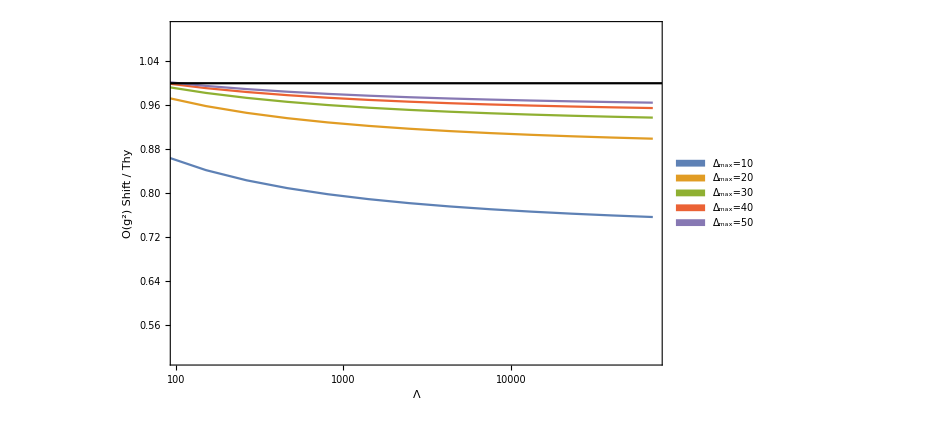

```mathematica
line=Plot[1,{x,0,100000},PlotStyle->{Black}];
plot=ListLogLinearPlot[{data10,data20,data30,data40,data50},ImageSize->700,PlotRange-> {{0,70000},{.5,1.1}},Frame->True,Joined->True,FrameLabel->{{Style["O(g^2) Shift / Thy",FontFamily->"Times",FontSize->16,FontColor->Black],None},{Style["Λ",FontFamily->"Times",FontSize->16,FontColor->Black],Style["O(g^2) Mass Shift (Λ_IR = 0.5)",FontFamily->"Times",FontSize->16,FontColor->Black]}},PlotLegends->Placed[SwatchLegend[{"Δ_max=10","Δ_max=20","Δ_max=30","Δ_max=40","Δ_max=50"},LabelStyle->{FontFamily->"Times",15},LegendLayout->{"Column",2}],{.8,.3}]];
fig=Show[plot,line]
```

```mathematica
dir="/Users/khandker/Dropbox/Higher D Basis/3DCode/"
```

/Users/khandker/Dropbox/Higher D Basis/3DCode/

```mathematica
(* Save *)
filename=dir<>"1pg2Shift";
DeleteFile[filename];
Save[filename,{data10,data20,data30,data40,data50}];
```

DeleteFile::fdnfnd: Directory or file /Users/khandker/Dropbox/Higher D Basis/3DCode/1pg2Shift not found.

Save::noopen: Cannot open /Users/khandker/Dropbox/Higher D Basis/3DCode/1pg2Shift.

```mathematica
data10
```

data10

### Extrapolate Δ_max

```mathematica
ratioWidth=8/10;
```

```mathematica
Clear[kmax,m,Λ,ΛIR];
kmax=100;
m=1.;
ΛIR=.5;
Monitor[
temp=Table[
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
kinetic3=kineticFunc[3,dmax,kmax,ratioWidth]//N;
mass3=massFunc[3,dmax,kmax]//N;
{val3,vec3}=eigensys[Λ^2*kinetic3+m^2*mass3];
intTemp=int13Func[dmax,kmax,ratioWidth];
int13=Table[(intTemp.vec3[[i3]])/(√(val3[[i3]]-1)),{i3,Length[vec3]}];
{dmax,(-Λ^2(int13.int13))/(-1/(96 π^2)Log[(Λ/m+1)^2/(8(Λ/m-1))])}
,{dmax,41,50,1}];
,{dmax}]
```

Part::take: Cannot take positions 1 through 37 in counts3.

Part::span: 1;;Total[counts3⟦1;;37⟧] is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Set::shape: Lists {val3,vec3} and … are not the same shape.

Part::take: Cannot take positions 1 through 37 in counts3.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::span: 1;;Total[counts3⟦1;;37⟧] is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::span: 1;;Total[counts3⟦1;;38⟧] is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

Set::shape: Lists {val3,vec3} and … are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
temp
```

{{41,0.},{42,0.},{43,0.},{44,0.},{45,0.},{46,0.},{47,0.},{48,0.},{49,0.},{50,0.}}

```mathematica
dataVaryD=Join[dataVaryD,temp]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Join[dataVaryD,{{41,0.},{42,0.},{43,0.},{44,0.},{45,0.},{46,0.},{47,0.},{48,0.},{49,0.},{50,0.}}].

Hold[Join[dataVaryD,{{41,0.},{42,0.},{43,0.},{44,0.},{45,0.},{46,0.},{47,0.},{48,0.},{49,0.},{50,0.}}]]

```mathematica
dir
```

/Users/khandker/Dropbox/Higher D Basis/3DCode/

```mathematica
Get[dir<>"1pg2Shift"];
```

Get::noopen: Cannot open /Users/khandker/Dropbox/Higher D Basis/3DCode/1pg2Shift.

```mathematica
(* Save *)
filename=dir<>"1pg2Shift";
DeleteFile[filename];
Save[filename,{data10,data20,data30,data40,data50,dataVaryD}];
```

DeleteFile::fdnfnd: Directory or file /Users/khandker/Dropbox/Higher D Basis/3DCode/1pg2Shift not found.

Save::noopen: Cannot open /Users/khandker/Dropbox/Higher D Basis/3DCode/1pg2Shift.

### Plot

```mathematica
dir="/Users/khandker/Dropbox/Higher D Basis/3DCode/";
```

```mathematica
Get[dir<>"1pg2Shift"];
```

Get::noopen: Cannot open /Users/khandker/Dropbox/Higher D Basis/3DCode/1pg2Shift.

ListLogLinearPlot::lpn: {{},{},{},{},{{1.05892,0.},{1.65567,0.},{2.22564,0.},{2.7874,0.},{3.34653,0.},{3.90481,0.},{4.4628,0.},{5.02071,0.},{5.57858,0.},{6.13645,0.},{6.69431,0.},{7.25217,0.},{7.81002,0.},{8.36788,0.},{8.92574,0.},{9.4836,0.},{10.0415,0.},{10.5993,0.},{11.1572,0.}}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogLinearPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

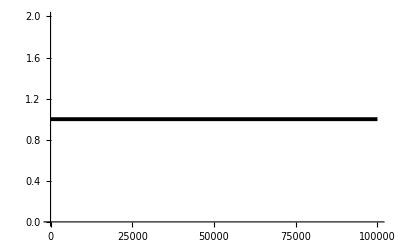
Show[ListLogLinearPlot[{data10,data20,data30,data40,{{2.88327,0.},{5.23657,0.},{9.25938,0.},{16.2388,0.},{28.4041,0.},{49.6406,0.},{86.7304,0.},{151.519,0.},{264.696,0.},{462.407,0.},{807.793,0.},{1411.16,0.},{2465.19,0.},{4306.51,0.},{7523.16,0.},{13142.4,0.},{22958.9,0.},{40107.5,0.},{70064.9,0.}}},ImageSize→700,PlotRange→{{0,70000},{0.6,1.03}},Frame→True,Joined→True,FrameLabel→{{None,None},{Λ_UV / m,None}},PlotLegends→Placed[SwatchLegend[{Δ_max=10,Δ_max=20,Δ_max=30,Δ_max=40,Δ_max=50,Δ_max=18},LabelStyle→{FontFamily→Times,28},LegendLayout→{Column,2}],{0.25,0.23}],PlotStyle→{Thickness[0.007]},FrameStyle→{GrayLevel[0],Thickness[0.003]},FrameTicksStyle→Directive[GrayLevel[0],26]],-Graphics-]

```mathematica
line=Plot[1,{x,0,100000},PlotStyle->{Black,Thickness[.007]}];
plot=ListLogLinearPlot[{data10,data20,data30,data40,data50},ImageSize->700,PlotRange-> {{0,70000},{.6,1.03}},Frame->True,Joined->True,FrameLabel->{{None,None},{Style["Λ_UV / m",FontFamily->"Times",FontSize->35,FontColor->Black],None}},PlotLegends->Placed[SwatchLegend[{"Δ_max=10","Δ_max=20","Δ_max=30","Δ_max=40","Δ_max=50","Δ_max=18"},LabelStyle->{FontFamily->"Times",28},LegendLayout->{"Column",2}],{0.25,0.23}],PlotStyle->{Thickness[.007]},FrameStyle->{Black,Thickness[0.003]},FrameTicksStyle->Directive[Black,26]];
fig1=Show[plot,line]
```

```mathematica
dataVaryD
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Join[dataVaryD,{{41,0.},{42,0.},{43,0.},{44,0.},{45,0.},{46,0.},{47,0.},{48,0.},{49,0.},{50,0.}}].

Hold[Join[dataVaryD,{{41,0.},{42,0.},{43,0.},{44,0.},{45,0.},{46,0.},{47,0.},{48,0.},{49,0.},{50,0.}}]]

```mathematica
data=Thread[{1/dataVaryD[[All,1]]^2,dataVaryD[[All,2]]}];
data//N
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Join[dataVaryD,{{41,0.},{42,0.},{43,0.},{44,0.},{45,0.},{46,0.},{47,0.},{48,0.},{49,0.},{50,0.}}].

data

```mathematica
data[[31;;All;;2]]
```

Part::take: Cannot take positions 31 through -1 in data.

data⟦31;;All;;2⟧

Part::take: Cannot take positions 31 through -1 in data.

FindFit::fitd: First argument data⟦31;;All⟧ in FindFit is not a list or a rectangular array.

FindFit[data⟦31;;All⟧,b+a x,{a,b},x]

General::ivar: 0.0000204286 is not a valid variable.

ReplaceAll::reps: {FindFit[data⟦31;;All⟧,0.0000204286 a+b,{a,b},0.0000204286]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0.0204286 is not a valid variable.

ReplaceAll::reps: {FindFit[data⟦31;;All⟧,0.0204286 a+b,{a,b},0.0204286]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[data⟦31;;All⟧,0.0408368 a+b,{a,b},0.0408368]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

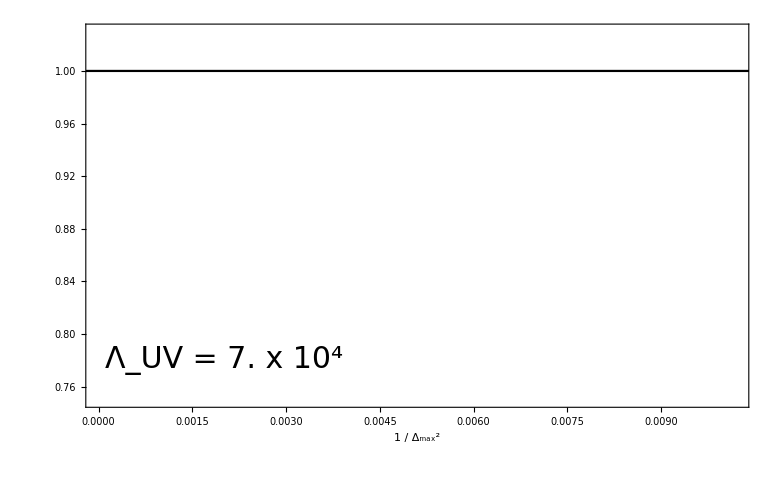

```mathematica
marker1=Graphics[{Blue,Disk[]}];
line=Plot[1,{x,-10,10},PlotStyle->Black,PlotRange->All];
plot=ListPlot[{data},ImageSize->780,PlotRange-> {{0,.0102},{.75,1.03}},Frame->True,Joined->False,FrameLabel->{{None,None},{Style["1 / Δ_max^2",FontFamily->"Times",FontSize->35,FontColor->Black],None}},PlotLegends->Placed[SwatchLegend[{},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Column",1}],{0.8,0.2}],PlotMarkers->{{marker1,12}},PlotStyle->Blue,FrameStyle->{Black,Thickness[0.003]},FrameTicksStyle->Directive[Black,26]];
fit=FindFit[data[[31;;All]],a*x+b,{a,b},x]
plotfit=Plot[(a*x+b)/.fit,{x,0,1},PlotStyle->{Thickness[.006]}];
fig2=Show[plot,line,plotfit,Epilog->Inset[Style["Λ_UV = 7. x 10^4",FontFamily->"Times",30],{.002,.78}]]
```

```mathematica
grid=Labeled[GraphicsGrid[{{fig1,fig2}},ImageSize->1500,Spacings->{-50,0}],{"Perturbation Theory at O(λ^2)","δm_gap^2  /  Theory"},{Top,Left},RotateLabel->True,LabelStyle->Directive[FontFamily->"Times",45],Spacings->{-.5,0}]
```

-Graphics-Perturbation Theory at O(λ^2)δm_gap^2  /  Theory

### Test

```mathematica
dir="/Users/khandker/Dropbox/Higher D Basis/3DCode/";
```

```mathematica
Get[dir<>"1pg2Shift"];
```

Get::noopen: Cannot open /Users/khandker/Dropbox/Higher D Basis/3DCode/1pg2Shift.

```mathematica
data40
```

data40

```mathematica
raw40=Thread[{data40[[All,1]],data40[[All,2]]*(1/(96 π^2)Log[(data40[[All,1]]+1)^2/(8(data40[[All,1]]-1))])}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

{Symbol[],(Log[(1+Symbol[])^2/(8 (-1+Symbol[]))] Symbol[])/(96 π^2)}

```mathematica
test=Interpolation[raw40]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

InterpolatingFunction[…]

```mathematica
LogLogPlot[test[x],{x,3,10000}]
```

InterpolatingFunction::dmval: Input value {3.0005} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.5407} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.17815} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[96 π^2*x*test'[x],{x,3,70000},ImageSize->500]
```

InterpolatingFunction::dmval: Input value {4.42994} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1432.94} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2861.45} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## 1p O(g^2) Spectral Shift

```mathematica
ratioWidth=8/10;
```

```mathematica
Clear[dmax,m,Λ,ΛIR];
dmax=40;
m=1.;
ΛIR=.5;
kmax=40;

Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
kinetic3=kineticFunc[3,dmax,kmax,ratioWidth]//N;
mass3=massFunc[3,dmax,kmax]//N;
{val3,vec3}=eigensys[Λ^2*kinetic3+m^2*mass3];
int13=int13Func[dmax,kmax,ratioWidth];

MElist=36 Λ^2*Table[(int13.vec3[[i]])^2,{i,Length[vec3]}];
MEsum=MElist//Accumulate;
```

```mathematica
dataK40=Thread[{val3/m^2,MEsum}]; 
(* ∑_(μi≤μ) |Subscript[ℳ^(n->n+2), min,i]|^2 = n^3/36 Subscript[I, ϕ^3](μ^2/n-(n-1)m^2) *)
(* Subscript[I, ϕ^3](μ) = 3/(16 π^2)(μ-3m)^2 *) 
thy=(3 m^2)/(16 π^2)(√(μ2/m^2)-3)^2 //Simplify;
```

```mathematica
Λ^2
```

7522.16

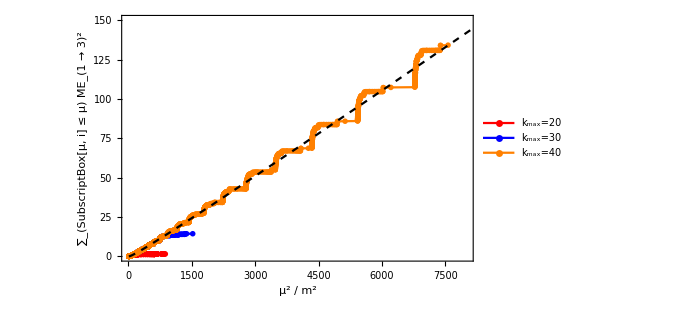

```mathematica
plot=ListPlot[{dataK20,dataK30,dataK40},Frame->True,FrameStyle->Thickness[0.002],PlotStyle->{{Red,PointSize[0.012]},{Blue,PointSize[0.012]},{Orange,PointSize[0.012]},{Darker[Magenta],PointSize[0.012]},{Darker[Green],PointSize[0.012]}},FrameLabel->{Style["μ^2 / m^2",FontFamily->"Times",FontSize->16,FontColor->Black],Style["∑_(SubscriptBox[μ, i] ≤  μ) ME_(1 → 3)^2",FontFamily->"Times",FontSize->16,FontColor->Black],Style["1p Perturbative ME^2 Sum  (Δ_max=16,  k_max=25,  Λ=25)",FontFamily->"Times",FontSize->16,FontColor->Black],None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->500,PlotRange->{{0,8000},{0,150}},(*PlotLegends->Placed[SwatchLegend[{"k_max = 100","k_max = 40","k_max = 60","k_max = 80","k_max = 100"},LabelStyle->{FontFamily->"Times",10},LegendLayout->{"Row",5}],{.1,0.35}],*)Joined->True,PlotMarkers->{Style["●"],4},PlotLegends->{"k_max=20","k_max=30","k_max=40"}];
thyplot=Plot[thy,{μ2,9,100000},PlotStyle->{Black,Dashed,Thick}];
Show[plot,thyplot]
```

## 1p O(g^3) Shift

### Scan over k_max

```mathematica
t1=AbsoluteTime[];

Int3to3=binaryGet["/Users/khandker/Dropbox/Higher D Basis/3DCode/All Minus Data/Int3to3_Dmax"<>ToString[DMAX]<>"_Kmax100_r8_AllMinus.WXF"];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 0.321605

```mathematica
ratioWidth=8/10;
```

```mathematica
Clear[dmax,kmax,m,Λ,ΛIR];
dmax=50;
m=1.;
ΛIR=.5;
Monitor[
temp=Table[
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
kinetic3=kineticFunc[3,dmax,kmax,ratioWidth]//N;
mass3=massFunc[3,dmax,kmax]//N;
{val3,vec3}=eigensys[Λ^2*kinetic3+m^2*mass3];

intTemp=int13Func[dmax,kmax,ratioWidth];
int13=(intTemp.Transpose[vec3])/(√(val3-1));

intTemp=Submatrix[Int3to3,3,3,DMAX,100,dmax,kmax,ratioWidth];
int33=(vec3.intTemp.Transpose[vec3])/Outer[√((#1-1)(#2-1))&,val3,val3];

coeff3=(4!)^3*Λ^3(int13.int33.int13); 
{Λ,coeff3}
,{kmax,10,100,5}];
,{kmax}]
```

```mathematica
thy=(4!)^3/(4(4π)^2(2π)^2)(7/16 π*Zeta[3]);
```

```mathematica
dataD50r8=Thread[{temp[[All,1]],temp[[All,2]]/thy}]
```

{{2.88327,0.0318904},{5.23657,0.102994},{9.25938,0.226526},{16.2388,0.380421},{28.4041,0.53334},{49.6406,0.664315},{86.7304,0.765624},{151.519,0.838584},{264.696,0.888703},{462.407,0.922088},{807.793,0.943861},{1411.16,0.957842},{2465.19,0.966713},{4306.51,0.972288},{7523.16,0.975762},{13142.4,0.977914},{22958.9,0.979239},{40107.5,0.980051},{70064.9,0.980546}}

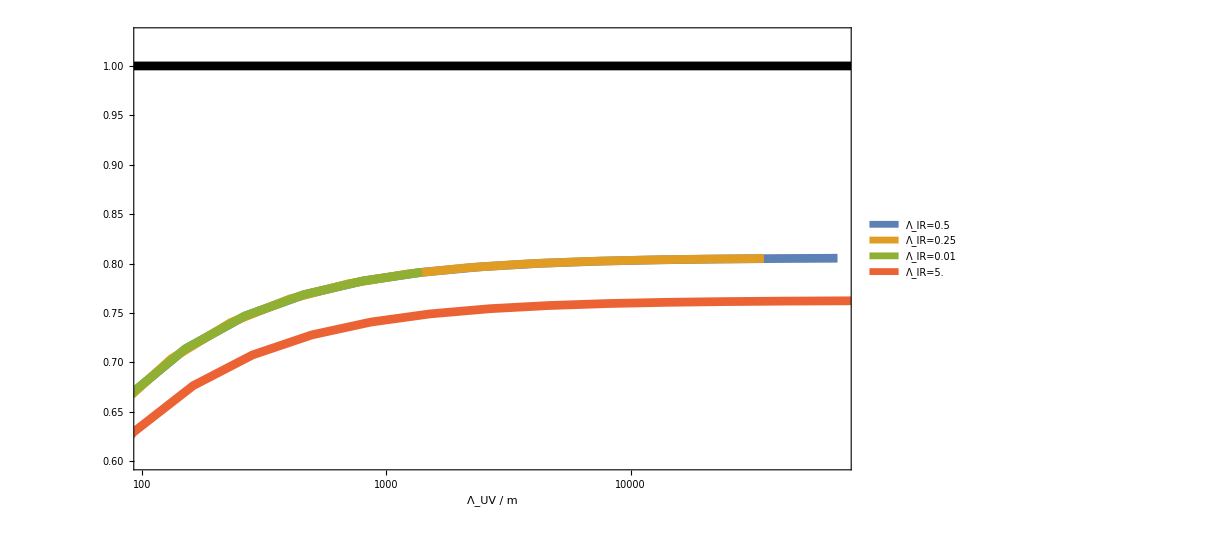

```mathematica
line=Plot[1,{x,0,100000},PlotStyle->{Black,Thickness[.007]}];
plot=ListLogLinearPlot[{dataD10IR05,dataD10IR025,dataD10IR001,dataD10IR5},ImageSize->900,PlotRange-> {{0,70000},{.6,1.03}},Frame->True,Joined->True,FrameLabel->{{None,None},{Style["Λ_UV / m",FontFamily->"Times",FontSize->35,FontColor->Black],None}},PlotLegends->Placed[SwatchLegend[{"Λ_IR=0.5","Λ_IR=0.25","Λ_IR=0.01","Λ_IR=5.","Δ_max=16","Δ_max=18"},LabelStyle->{FontFamily->"Times",28},LegendLayout->{"Column",1}],{0.8,0.23}],PlotStyle->{Thickness[.007]},FrameStyle->{Black,Thickness[0.003]},FrameTicksStyle->26];
fig1=Show[plot,line]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["1pg3Shift"];
```

```mathematica
(* Save *)
filename="1pg3Shift";
DeleteFile[filename];
Save[filename,{dataD10r8,dataD20r8,dataD30r8,dataD40r8,dataD50r8,datar8VaryD}];
```

### Extrapolate Δ_max

```mathematica
t1=AbsoluteTime[];

Int3to3=binaryGet["/Users/khandker/Dropbox/Higher D Basis/3DCode/All Minus Data/Int3to3_Dmax"<>ToString[DMAX]<>"_Kmax100_r8_AllMinus.WXF"];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 0.169788

```mathematica
ratioWidth=8/10;
```

```mathematica
Clear[dmax,kmax,m,Λ,ΛIR];
kmax=100;
m=1.;
ΛIR=.5;
Monitor[
temp=Table[
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
kinetic3=kineticFunc[3,dmax,kmax,ratioWidth]//N;
mass3=massFunc[3,dmax,kmax]//N;
{val3,vec3}=eigensys[Λ^2*kinetic3+m^2*mass3];

intTemp=int13Func[dmax,kmax,ratioWidth];
int13=(intTemp.Transpose[vec3])/(√(val3-1));

intTemp=Submatrix[Int3to3,3,3,DMAX,100,dmax,kmax,ratioWidth];
int33=(vec3.intTemp.Transpose[vec3])/Outer[√((#1-1)(#2-1))&,val3,val3];

coeff3=(4!)^3*Λ^3(int13.int33.int13); 
{dmax,coeff3}
,{dmax,41,50,1}];
,{dmax}]
```

```mathematica
temp
```

{{41,0.894358},{42,0.89444},{43,0.895447},{44,0.895519},{45,0.89641},{46,0.896474},{47,0.897265},{48,0.897322},{49,0.898029},{50,0.89808}}

```mathematica
datar8VaryD=Join[datar8VaryD,temp]
```

{{10,0.737725},{11,0.784016},{12,0.785301},{13,0.813694},{14,0.814694},{15,0.833486},{16,0.834268},{17,0.847418},{18,0.848035},{19,0.857636},{20,0.85813},{21,0.86538},{22,0.86578},{23,0.871403},{24,0.871732},{25,0.876192},{26,0.876464},{27,0.880068},{28,0.880296},{29,0.883256},{30,0.883449},{31,0.885912},{32,0.886076},{33,0.888151},{34,0.888292},{35,0.890059},{36,0.890181},{37,0.891698},{38,0.891804},{39,0.893118},{40,0.893211},{41,0.894358},{42,0.89444},{43,0.895447},{44,0.895519},{45,0.89641},{46,0.896474},{47,0.897265},{48,0.897322},{49,0.898029},{50,0.89808}}

```mathematica
dir
```

/Users/khandker/Dropbox/Higher D Basis/3DCode/

```mathematica
(* Save *)
filename="1pg3Shift";
DeleteFile[filename];
Save[filename,{dataD10r8,dataD20r8,dataD30r8,dataD40r8,dataD50r8,datar8VaryD}];
```

### Plot

```mathematica
dir="/Users/khandker/Dropbox/Higher D Basis/3DCode/";
```

```mathematica
Get[dir<>"1pg3Shift"];
```

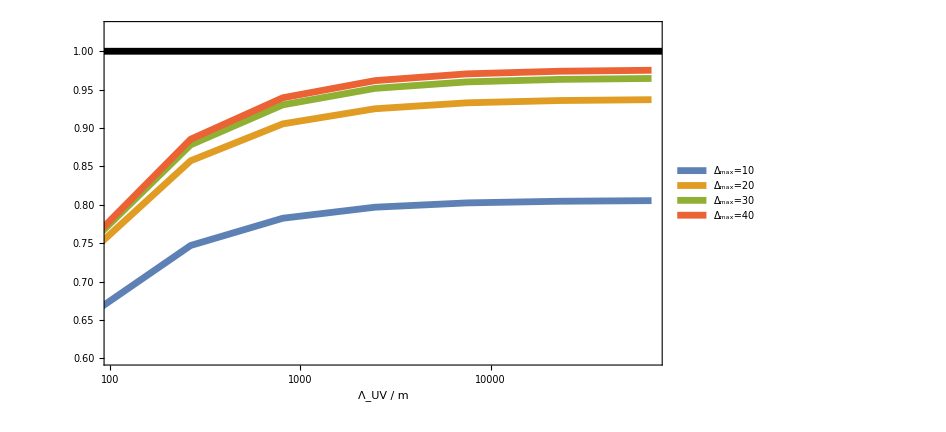

```mathematica
line=Plot[1,{x,0,100000},PlotStyle->{Black,Thickness[.007]}];
plot=ListLogLinearPlot[{dataD10r8,dataD20r8,dataD30r8,dataD40r8},ImageSize->700,PlotRange-> {{0,70000},{.6,1.03}},Frame->True,Joined->True,FrameLabel->{{None,None},{Style["Λ_UV / m",FontFamily->"Times",FontSize->35,FontColor->Black],None}},PlotLegends->Placed[SwatchLegend[{"Δ_max=10","Δ_max=20","Δ_max=30","Δ_max=40","Δ_max=16","Δ_max=18"},LabelStyle->{FontFamily->"Times",28},LegendLayout->{"Column",1}],{0.8,0.23}],PlotStyle->{Thickness[.007]},FrameStyle->{Black,Thickness[0.003]},FrameTicksStyle->Directive[Black,26]];
fig1=Show[plot,line]
```

```mathematica
thy=(4!)^3/(4(4π)^2(2π)^2)(7/16 π*Zeta[3]);
```

```mathematica
temp=datar8VaryD;
```

```mathematica
data=Thread[{1/temp[[All,1]]^2,temp[[All,2]]/thy}]//N
```

{{0.01,0.805467},{0.00826446,0.856008},{0.00694444,0.857411},{0.00591716,0.888411},{0.00510204,0.889503},{0.00444444,0.91002},{0.00390625,0.910874},{0.00346021,0.925231},{0.00308642,0.925905},{0.00277008,0.936388},{0.0025,0.936928},{0.00226757,0.944843},{0.00206612,0.94528},{0.00189036,0.951419},{0.00173611,0.951778},{0.0016,0.956647},{0.00147929,0.956945},{0.00137174,0.96088},{0.00127551,0.961129},{0.00118906,0.96436},{0.00111111,0.964571},{0.00104058,0.96726},{0.000976563,0.96744},{0.000918274,0.969705},{0.000865052,0.969859},{0.000816327,0.971788},{0.000771605,0.971921},{0.00073046,0.973577},{0.000692521,0.973693},{0.000657462,0.975128},{0.000625,0.97523}}

```mathematica
(* line=Plot[1,{x,-10,10},PlotStyle->Black,PlotRange->All];
plot=ListPlot[{data},ImageSize->780,PlotRange-> {{0,.0102},{.75,1.03}},Frame->True,Joined->False,FrameLabel->{{None,None},{Style["1 / Δ_max^2",FontFamily->"Times",FontSize->35,FontColor->Black],None}},PlotLegends->Placed[SwatchLegend[{},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Column",1}],{0.8,0.2}],PlotMarkers->{{●,Large}},PlotStyle->Blue,FrameStyle->{Black,Thickness[0.003]},FrameTicksStyle->26];
fit=FindFit[data[[21;;All]],a*x+b,{a,b},x]
plotfit=Plot[(a*x+b)/.fit,{x,0,1},PlotStyle->{Thickness[.006]}];
fig2=Show[plot,line,plotfit,Epilog->Inset[Style["Λ_UV = 7. x 10^4",FontFamily->"Times",30],{.002,.78}]]; *)
```

{a→-21.4946,b→0.988912}

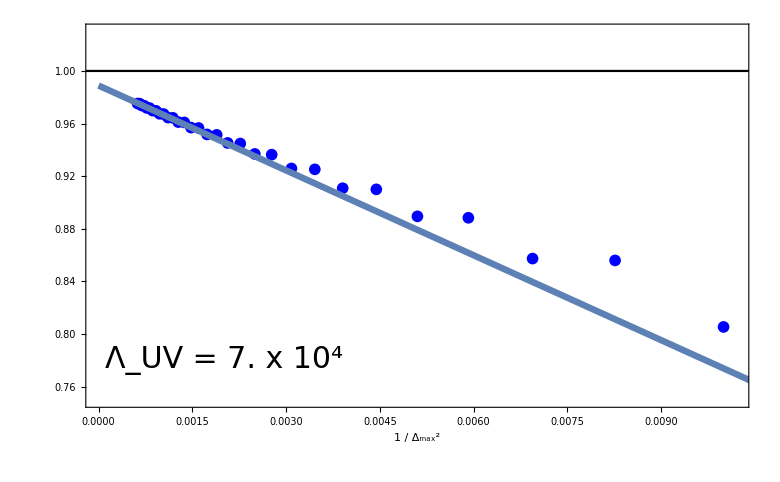

```mathematica
marker1=Graphics[{Blue,Disk[]}];
line=Plot[1,{x,-10,10},PlotStyle->Black,PlotRange->All];
plot=ListPlot[{data},ImageSize->780,PlotRange-> {{0,.0102},{.75,1.03}},Frame->True,Joined->False,FrameLabel->{{None,None},{Style["1 / Δ_max^2",FontFamily->"Times",FontSize->35,FontColor->Black],None}},PlotLegends->Placed[SwatchLegend[{},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Column",1}],{0.8,0.2}],PlotMarkers->{{marker1,12}},PlotStyle->Blue,FrameStyle->{Black,Thickness[0.003]},FrameTicksStyle->Directive[Black,26]];
fit=FindFit[data[[21;;All]],a*x+b,{a,b},x]
plotfit=Plot[(a*x+b)/.fit,{x,0,1},PlotStyle->{Thickness[.006]}];
fig2=Show[plot,line,plotfit,Epilog->Inset[Style["Λ_UV = 7. x 10^4",FontFamily->"Times",30],{.002,.78}]]
```

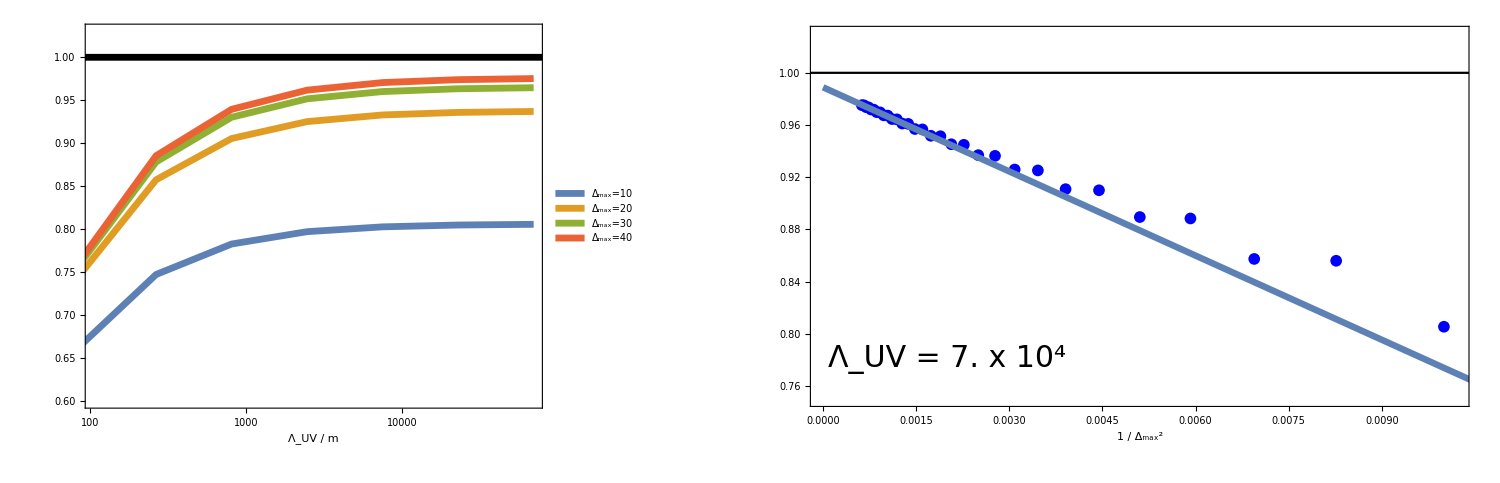
-Graphics-Perturbation Theory at O(λ^3)δm_gap^2  /  Theory

```mathematica
grid=Labeled[GraphicsGrid[{{fig1,fig2}},ImageSize->1500,Spacings->{-50,0}],{"Perturbation Theory at O(λ^3)","δm_gap^2  /  Theory"},{Top,Left},RotateLabel->True,LabelStyle->Directive[FontFamily->"Times",45],Spacings->{-.5,0}]
```

```mathematica
dataD40r8
```

{{2.88327,0.0318904},{9.25938,0.226526},{28.4041,0.53328},{86.7304,0.76426},{264.696,0.8854},{807.793,0.939415},{2465.19,0.961741},{7523.16,0.970569},{22958.9,0.973957},{70064.9,0.97523}}

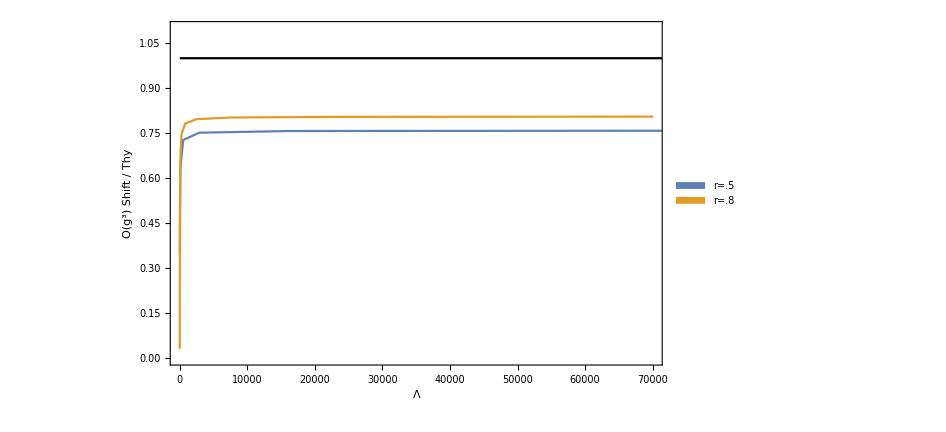

```mathematica
line=Plot[1,{x,0,100000},PlotStyle->Black];
plot=ListPlot[{dataD10r5,dataD10r8},ImageSize->700,PlotRange-> {{0,70000},{0,1.1}},Frame->True,Joined->True,FrameLabel->{{Style["O(g^3) Shift / Thy",FontFamily->"Times",FontSize->16,FontColor->Black],None},{Style["Λ",FontFamily->"Times",FontSize->16,FontColor->Black],Style["O(g^3) Mass Shift   (Λ_IR=0.5,  Δ_max=10)",FontFamily->"Times",FontSize->16,FontColor->Black]}},PlotLegends->Placed[SwatchLegend[{"r=.5","r=.8","Δ_max=30","Δ_max=40","Δ_max=16","Δ_max=18"},LabelStyle->{FontFamily->"Times",15},LegendLayout->{"Column",1}],{0.8,0.2}]];
fig=Show[plot,line]
```

```mathematica
dataD10r5
```

{{15.9922,0.346186},{90.5083,0.632841},{512.,0.727598},{2896.31,0.75192},{16384.,0.757555},{92681.9,0.758787}}

```mathematica
dataD10r8
```

{{2.88327,0.0318966},{9.25938,0.223317},{28.4041,0.492446},{86.7304,0.664483},{264.696,0.747067},{807.793,0.78255},{2465.19,0.796926},{7523.16,0.802537},{22958.9,0.804671},{70064.9,0.805467}}

### Scratch

```mathematica
Clear[Dmax,m,Λ,ΛIR,ΛIRlist];
Dmax=10;
m=1.;
ΛIR=.5;
Monitor[
temp=Table[
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
kinetic3=kineticFunc[3,Dmax,kmax]//N;
mass3=massFunc[3,Dmax,kmax]//N;
{val3,vec3}=eigensys[Λ^2*kinetic3+m^2*mass3];

intTemp=int13Func[Dmax,kmax];
int13=Table[(intTemp.vec3[[i3]])/(√(val3[[i3]]-1)),{i3,Length[vec3]}];

intTemp=int33Func[Dmax,kmax];
int33=Table[(vec3[[i3]].intTemp.vec3[[j3]])/(√((val3[[i3]]-1)(val3[[j3]]-1))),{i3,Length[vec3]},{j3,Length[vec3]}];

coeff3=(4!)^3*Λ^3(int13.int33.int13); 
{Λ,coeff3}
,{kmax,20,110,10}];
,{kmax}]
```

$Aborted

```mathematica
dataD5=Thread[{temp[[All,1]],temp[[All,2]]/0.8941876918}]
```

{{4.03198,0.0614381},{7.12931,0.141849},{12.2464,0.233273},{20.8404,0.315239},{35.3529,0.379878},{59.9056,0.427379},{101.471,0.460846},{171.855,0.483779},{291.045,0.499185},{492.891,0.509382}}

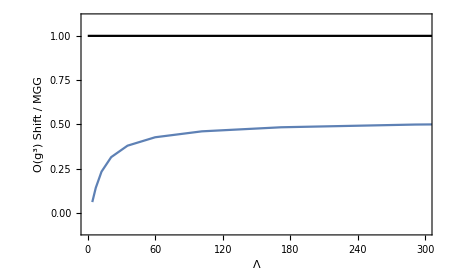

```mathematica
line=Plot[1,{x,0,500},PlotStyle->Black];
plot=ListPlot[{dataD5},ImageSize->450,PlotRange-> {{0,300},{-.1,1.1}},Frame->True,Joined->True,FrameLabel->{{Style["O(g^3) Shift / MGG",FontFamily->"Times",FontSize->16,FontColor->Black],None},{Style["Λ",FontFamily->"Times",FontSize->16,FontColor->Black],Style["O(g^3) Mass Shift",FontFamily->"Times",FontSize->16,FontColor->Black]}},PlotLegends->Placed[SwatchLegend["Λ_IR=0.5",LabelStyle->{FontFamily->"Times",15},LegendLayout->{"Column",1}],{0.8,0.7}]];
fig=Show[plot,line]
```

```mathematica
Dmax=5;
kmax=20;
m=1.;
ΛIR=.5;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
```

```mathematica
kinetic3=kineticFunc[3,Dmax,kmax]//N;
mass3=massFunc[3,Dmax,kmax]//N;
{val3,vec3}=eigensys[Λ^2*kinetic3+m^2*mass3];
```

```mathematica
Timing[
intTemp=int13Func[Dmax,kmax];
int13=Table[(intTemp.vec3[[i3]])/(√(val3[[i3]]-1)),{i3,Length[vec3]}];
]
```

{0.002987,Null}

```mathematica
Timing[
intTemp=int13Func[Dmax,kmax];
test13=(intTemp.Transpose[vec3])/(√(val3-1));
]
```

{0.002942,Null}

```mathematica
int13-test13
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Timing[
intTemp=int33Func[Dmax,kmax];
]
```

{0.290325,Null}

```mathematica
Timing[
int33=Table[(vec3[[i3]].intTemp.vec3[[j3]])/(√((val3[[i3]]-1)(val3[[j3]]-1))),{i3,Length[vec3]},{j3,Length[vec3]}];
]
```

{0.045792,Null}

```mathematica
Timing[
test33=(vec3.intTemp.Transpose[vec3])/Outer[√((#1-1)(#2-1))&,val3,val3];
]
```

{0.003073,Null}

```mathematica
int33-test33//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

## Regular Perturbation Theory

## Clear Everything

```mathematica
ClearAll["Global`*"];
```

## Load Data (DMAX=16 or 18, pre-μ-discretization)

```mathematica
DMAX=16;

dir="/Users/khandker/Dropbox/Higher D Basis/Dmax"<>ToString[DMAX]<>" Data/";
Get[dir<>"Basis2_Dmax"<>ToString[DMAX]];
Get[dir<>"Basis3_Dmax"<>ToString[DMAX]];
Get[dir<>"Basis4_Dmax"<>ToString[DMAX]];
Get[dir<>"Basis5_Dmax"<>ToString[DMAX]];
Get[dir<>"Bas2Mass"];
Get[dir<>"Bas3Mass"];
Get[dir<>"Bas4Mass"];
Get[dir<>"Bas5Mass"];
Get[dir<>"Bas1to3"];
Get[dir<>"Bas3to3E"];
Get[dir<>"Bas3to5"];
```

```mathematica
(* DMAX=18;

dir="/Users/khandker/Dropbox/Higher D Basis/Zuhair/Dmax"<>ToString[DMAX]<>" Data/";
Get[dir<>"Basis3_Dmax"<>ToString[DMAX]];
Get[dir<>"Bas3Mass_Dmax"<>ToString[DMAX]];
Get[dir<>"Bas1to3_Dmax"<>ToString[DMAX]];
Get[dir<>"Bas3to3E_Dmax"<>ToString[DMAX]]; *)
```

## Define Functions (and set ratioWidth)

```mathematica
(* Number of basis states *)
numStates[npart_,Δmax_]:=Which[Δmax<(3/2)*npart,0,npart==1,1,npart≠ 1,ToExpression["counts"<>ToString[npart]][[1;;Floor[Δmax-(3/2)npart+1]]]//Total];
```

```mathematica
(* Set ratioWidth for μ-discretization *)
ratioWidth=8/10;
```

```mathematica
(* Kinetic function *)
kineticFunc[npart_,Δmax_,kmax_]:=Module[{size=numStates[npart,Δmax],μsq},
If[npart==1,{0.},
μsq=Accumulate[Prepend[Table[ratioWidth^(kmax-k),{k,kmax}]/Sum[ratioWidth^(kmax-k),{k,kmax}],0]];
KroneckerProduct[IdentityMatrix[size],DiagonalMatrix[Table[(μsq[[k]]+μsq[[k+1]])/2,{k,kmax}]]]//N]];
```

```mathematica
(* Mass function *)
massFunc[npart_,Δmax_,kmax_]:=Module[{size=numStates[npart,Δmax]},
If[npart==1,{1.},
KroneckerProduct[Chop[ToExpression["BasisMass"<>ToString[npart]][[1;;size,1;;size]],10^-35],IdentityMatrix[kmax]]]];
```

```mathematica
(* Interaction 1->3 function *) 
int13Func[Δmax_,kmax_]:=Module[{size3=numStates[3,Δmax],μsq},
μsq=Accumulate[Prepend[Table[ratioWidth^(kmax-k),{k,kmax}]/Sum[ratioWidth^(kmax-k),{k,kmax}],0]];
KroneckerProduct[Chop[Basis1to3[[1;;size3]]],Table[√((μsq[[k+1]]-μsq[[k]])/(2π)),{k,kmax}]]//Flatten
];
```

```mathematica
(* Interaction 3->3 function *) 
int33Func[Δmax_,kmax_]:=Module[{size=numStates[3,Δmax],μsq,BasisNtoN,minpower,maxpower,zpowers,KMatrices,EMatrices,rule1,Temp1,rule2,Temp2},
μsq=Accumulate[Prepend[Table[ratioWidth^(kmax-k),{k,kmax}]/Sum[ratioWidth^(kmax-k),{k,kmax}],0]];
BasisNtoN=Basis3to3[[1;;size,1;;size]];
{minpower,maxpower}=getmaxminpower[BasisNtoN];
zpowers=Table[i,{i,minpower,maxpower}];
KMatrices=Table[KMatrix[L,kmax,μsq],{L,minpower,maxpower}];
EMatrices=Table[EMatrix[L,kmax,μsq],{L,minpower,maxpower}];
KMatrices=SparseArray[KMatrices];
EMatrices=SparseArray[EMatrices];
rule1={z^L_ EllipticE[z]->ℳE[L],z^L_ EllipticK[z]->ℳK[L],z*EllipticE[z]->ℳE[1],z*EllipticK[z]->ℳK[1],EllipticE[z]->ℳE[0],EllipticK[z]->ℳK[0]};
Temp1=BasisNtoN/.rule1;
rule2=Flatten[{Table[ℳE[zpowers[[i]]]->EMatrices[[i]],{i,Length[zpowers]}],Table[ℳK[zpowers[[i]]]->KMatrices[[i]],{i,Length[zpowers]}]}];
Temp2=(Temp1/.rule2)//ArrayFlatten;
Temp2+Transpose[Temp2]
];
```

```mathematica
(* Interaction 3->5 function *)
int35Func[Δmax_,kmax_]:=Module[{sizeN=numStates[3,Δmax],sizeN2=numStates[5,Δmax],temp,BasisNtoN2,μsq,ℳ,DiscNtoN2,replaceRule},
temp=Chop[Basis3to5,10^-40]//Expand;
BasisNtoN2=temp[[1;;sizeN,1;;sizeN2]];
μsq=N[Accumulate[Prepend[Table[ratioWidth^(kmax-k),{k,kmax}]/Sum[ratioWidth^(kmax-k),{k,kmax}],0]]];
Clear[ℳ];
DiscNtoN2=Table[
replaceRule={μ^a_ μp^b_->ℳ[a,b,k,kp],μ*μp^b_->ℳ[1,b,k,kp],μ^a_ μp->ℳ[a,1,k,kp],μ*μp->ℳ[1,1,k,kp],μ^a_->ℳ[a,0,k,kp],μp^b_->ℳ[0,b,k,kp]};
BasisNtoN2[[row,col]]/.replaceRule,
{row,Dimensions[BasisNtoN2][[1]]},{col,Dimensions[BasisNtoN2][[2]]},{k,kmax},{kp,k,kmax}]//PadLeft//ArrayFlatten;

ℳ[ a_,b_,k_,kp_]:=ℳ[ a,b,k,kp]=1/(2π)*Which[k<kp,((μsq[[k+1]]^(a/2+1)-μsq[[k]]^(a/2+1))(μsq[[kp+1]]^(b/2+1)-μsq[[kp]]^(b/2+1)))/((a/2+1)(b/2+1)√((μsq[[k+1]]-μsq[[k]])(μsq[[kp+1]]-μsq[[kp]]))),k==kp,
(μsq[[k+1]]^(a/2+b/2+2)-μsq[[k]]^(a/2+b/2+2))/((a/2+1)(a/2+b/2+2)(μsq[[k+1]]-μsq[[k]]))-(μsq[[k+1]]^(b/2+1)μsq[[k]]^(a/2+1)-μsq[[k]]^(a/2+b/2+2))/((a/2+1)(b/2+1)(μsq[[k+1]]-μsq[[k]])),k>kp,0];

DiscNtoN2
];
```

```mathematica
(* Nonlocal counterterm function for npart=1 *) 
nonlocalFunc1[Δmax_,kmax_,Λ_]:=Module[{m=1.,μsq,kinetic3,mass3,int13,full3,vals3,vecs3},
μsq=N[Accumulate[Prepend[Table[ratioWidth^(kmax-k),{k,kmax}]/Sum[ratioWidth^(kmax-k),{k,kmax}],0]]];
kinetic3=kineticFunc[3,Δmax,kmax];
mass3=massFunc[3,Δmax,kmax];
int13=int13Func[Δmax,kmax];
full3=Λ^2*kinetic3+m^2*mass3//N;
{vals3,vecs3}=eigensys[full3];
-Λ^2*Sum[(int13.vecs3[[i]])^2/(1-vals3[[i]]),{i,Length[vals3]}]
];
```

```mathematica
(* Nonlocal counterterm function for npart=3 *) 
nonlocalFunc3[Δmax_,kmax_,Λ_]:=Module[{m=1.,μsq,kineticN,kineticN2,massN,massN2,IntNtoN2,fullN,fullN2,valsN,vecsN,valsN2,vecsN2,MassShifts,MassShiftsNonPositive,V},
μsq=N[Accumulate[Prepend[Table[ratioWidth^(kmax-k),{k,kmax}]/Sum[ratioWidth^(kmax-k),{k,kmax}],0]]];
kineticN=kineticFunc[3,Δmax,kmax];
kineticN2=kineticFunc[5,Δmax,kmax];
massN=massFunc[3,Δmax,kmax];
massN2=massFunc[5,Δmax,kmax];
IntNtoN2=int35Func[Δmax,kmax];
fullN=Λ^2*kineticN+m^2*massN//N;
fullN2=Λ^2*kineticN2+m^2*massN2//N;
{valsN,vecsN}=eigensys[fullN];
{valsN2,vecsN2}=eigensys[fullN2];
MassShifts=Total[Λ^2*(vecsN.IntNtoN2.Transpose[vecsN2])^2/Outer[Subtract,valsN,valsN2],{2}];
MassShiftsNonPositive=MassShifts/.{x_?Positive->0.};
(* V=vecsN;
-Transpose[V].DiagonalMatrix[MassShiftsNonPositive].V *)
-DiagonalMatrix[MassShiftsNonPositive]
];
```

```mathematica
(* Compute eigenvalues and eigenvecs *)
eigensys[mat_]:=Eigensystem[mat]//Transpose//Sort//Transpose;
eigenvals[mat_]:=Eigenvalues[mat]//Sort;
minVal[mat_]:=Eigenvalues[mat]//Min;
minvals[nVals_,mat_]:=eigenvals[mat][[1;;nVals]];
```

```mathematica
(* Extract (dmax,kmax) submatrix from (DMAX,KMAX) matrix. 
   n1,n2 = particle number for row/col, and I'm assuming n1,n2 > 1.   *)
Submatrix[matrix_,n1_,n2_,DMAX_,KMAX_,dmax_,kmax_]:=Module[{size1=numStates[n1,dmax],size2=numStates[n2,dmax],temp1,temp2,temp3,temp4,μsq},
μsq=Accumulate[Prepend[Table[ratioWidth^(KMAX-k),{k,KMAX}]/Sum[ratioWidth^(KMAX-k),{k,KMAX}],0]]//N;
temp1=matrix[[1;;size1*KMAX,1;;size2*KMAX]];
temp2=Partition[temp1,{KMAX,KMAX}];
temp3=Map[#[[1;;kmax,1;;kmax]]&,temp2,{2}]//ArrayFlatten;
temp3*√(1/μsq[[kmax+1]])
];
```

```mathematica
(* These functions help save and load WXF formats *)
binarySave[name_,expr_]:=Export[name<>".WXF",BinarySerialize[expr]];
binaryGet[name_]:=Import[name]//BinaryDeserialize;
```

### Functions to discretize n→n

```mathematica
Gplus[L_,x_]:=Gplus[L,x]=(π*If[L==0,1,x^L])/(3(L+1))(HypergeometricPFQ[{1/2,1/2,L+1},{1,L+2},N[x]]-(L+1)/(L-1/2)HypergeometricPFQ[{1/2,1/2,L-1/2},{1,L+1/2},N[x]])
Gminus[L_,x_]:=Gminus[L,x]=(π*If[L==0,1,x^L])/(3(L+1))(HypergeometricPFQ[{-1/2,1/2,L+1},{1,L+2},N[x]]-(L+1)/(L-1/2)HypergeometricPFQ[{-1/2,1/2,L-1/2},{1,L+1/2},N[x]])
Hplus[L_,x_]:=
Hplus[L,x]=Gamma[L+1/2]^2/(3 Gamma[L+1]^2) (2HypergeometricPFQ[{-1/2,1,L+1/2,L+1/2},{1/2,L+1,L+1},N[x]]+HypergeometricPFQ[{1,1,L+1/2,L+1/2},{2,L+1,L+1},N[x]])
Hminus[L_,x_]:=
Hminus[L,x]=Gamma[L-1/2]^2/(3 Gamma[L+1]^2)(2HypergeometricPFQ[{-1/2,1,L-1/2,L+1/2},{1/2,L+1,L+1},N[x]]+HypergeometricPFQ[{1,1,L-1/2,L+1/2},{2,L+1,L+1},N[x]])
Jplus[L_,x_]:=
Jplus[L,x]=-(Gamma[L+2]^2 x)/(15 Gamma[L+5/2]^2)(5HypergeometricPFQ[{1,1,L+2,L+2},{2,L+5/2,L+5/2},N[x]]-2HypergeometricPFQ[{1,5/2,L+2,L+2},{7/2,L+5/2,L+5/2},N[x]])
Jminus[L_,x_]:=
Jminus[L,x]=
-(Gamma[L+2]Gamma[L+1]x)/(15 Gamma[L+5/2]^2)(5HypergeometricPFQ[{1,1,L+1,L+2},{2,L+5/2,L+5/2},N[x]]-2HypergeometricPFQ[{1,5/2,L+1,L+2},{7/2,L+5/2,L+5/2},N[x]])
```

```mathematica
KMatrix[L_,kmax_,μsq_]:=
Which[
L≥0&&L≠1/2,ArrayPad[PadLeft[Table[1/(2π)1/(√((μsq[[kp+1]]-μsq[[kp]])(μsq[[k+1]]-μsq[[k]])))(μsq[[k+1]] μsq[[kp+1]]^(1/2)Gplus[L,μsq[[k+1]]/μsq[[kp+1]]]-μsq[[k+1]] μsq[[kp]]^(1/2)Gplus[L,μsq[[k+1]]/μsq[[kp]]]-μsq[[k]] μsq[[kp+1]]^(1/2)Gplus[L,μsq[[k]]/μsq[[kp+1]]]+μsq[[k]] μsq[[kp]]^(1/2)Gplus[L,μsq[[k]]/μsq[[kp]]]),{k,kmax},{kp,k+1,kmax}]],{{0,0},{1,0}}]+DiagonalMatrix[Table[1/(2π)1/(μsq[[k+1]]-μsq[[k]])((π*HypergeometricPFQ[{1/2,1/2,L+1},{1,L+2},1.])/(3(L+1))(μsq[[k+1]]^(3/2)-μsq[[k]]^(3/2))-μsq[[k]] μsq[[k+1]]^(1/2)Gplus[L,μsq[[k]]/μsq[[k+1]]]+μsq[[k]]^(3/2)Gplus[L,1.]),{k,kmax}]],

L<0&&IntegerQ[L],ArrayPad[PadLeft[Table[1/(2π)1/(√((μsq[[kp+1]]-μsq[[kp]])(μsq[[k+1]]-μsq[[k]])))(μsq[[k+1]] μsq[[kp+1]]^(1/2)Hplus[-L,μsq[[k+1]]/μsq[[kp+1]]]-μsq[[k+1]] μsq[[kp]]^(1/2)Hplus[-L,μsq[[k+1]]/μsq[[kp]]]-μsq[[k]] μsq[[kp+1]]^(1/2)Hplus[-L,μsq[[k]]/μsq[[kp+1]]]+μsq[[k]] μsq[[kp]]^(1/2)Hplus[-L,μsq[[k]]/μsq[[kp]]]),{k,kmax},{kp,k+1,kmax}]],{{0,0},{1,0}}]+DiagonalMatrix[Table[1/(2π)1/(μsq[[k+1]]-μsq[[k]])(Gamma[-L+1/2]^2/(3 Gamma[-L+1]^2)(μsq[[k+1]]^(3/2)-μsq[[k]]^(3/2))HypergeometricPFQ[{1,1,-L+1/2,-L+1/2},{2,-L+1,-L+1},1.]-μsq[[k]] μsq[[k+1]]^(1/2)Hplus[-L,μsq[[k]]/μsq[[k+1]]]+μsq[[k]]^(3/2)Hplus[-L,1.]),{k,kmax}]],

L≤ 1/2&&IntegerQ[L+1/2],ArrayPad[PadLeft[Table[1/(2π)1/(√((μsq[[kp+1]]-μsq[[kp]])(μsq[[k+1]]-μsq[[k]])))(Gamma[-L+1]^2/(3 Gamma[-L+3/2]^2)(μsq[[k+1]]^(3/2)-μsq[[k]]^(3/2))Log[μsq[[kp+1]]/μsq[[kp]]]+μsq[[k+1]]^(3/2)Jplus[-L,μsq[[k+1]]/μsq[[kp+1]]]-μsq[[k+1]]^(3/2)Jplus[-L,μsq[[k+1]]/μsq[[kp]]]-μsq[[k]]^(3/2)Jplus[-L,μsq[[k]]/μsq[[kp+1]]]+μsq[[k]]^(3/2)Jplus[-L,μsq[[k]]/μsq[[kp]]]),{k,kmax},{kp,k+1,kmax}]],{{0,0},{1,0}}]+DiagonalMatrix[Table[1/(2π)1/(μsq[[k+1]]-μsq[[k]])((2 Gamma[-L+1]^2)/(9 Gamma[-L+3/2]^2)(μsq[[k+1]]^(3/2)-μsq[[k]]^(3/2)-If[k==1,0.,3/2 μsq[[k]]^(3/2)Log[μsq[[k+1]]/μsq[[k]]]])+(2 Gamma[-L+2]^2)/(15 Gamma[-L+5/2]^2)(μsq[[k+1]]^(3/2)-μsq[[k]]^(3/2))HypergeometricPFQ[{1,5/2,-L+2,-L+2},{7/2,-L+5/2,-L+5/2},1.]-μsq[[k]]^(3/2)Jplus[-L,μsq[[k]]/μsq[[k+1]]]+μsq[[k]]^(3/2)Jplus[-L,1.]),{k,kmax}]]];
```

```mathematica
EMatrix[L_,kmax_,μsq_]:=
Which[
L≥0&&L≠1/2,
ArrayPad[PadLeft[Table[1/(2π)1/(√((μsq[[kp+1]]-μsq[[kp]])(μsq[[k+1]]-μsq[[k]])))(μsq[[k+1]] μsq[[kp+1]]^(1/2)Gminus[L,μsq[[k+1]]/μsq[[kp+1]]]-μsq[[k+1]] μsq[[kp]]^(1/2)Gminus[L,μsq[[k+1]]/μsq[[kp]]]-μsq[[k]] μsq[[kp+1]]^(1/2)Gminus[L,μsq[[k]]/μsq[[kp+1]]]+μsq[[k]] μsq[[kp]]^(1/2)Gminus[L,μsq[[k]]/μsq[[kp]]]),{k,kmax},{kp,k+1,kmax}]],{{0,0},{1,0}}]+DiagonalMatrix[Table[1/(2π)1/(μsq[[k+1]]-μsq[[k]])((π*HypergeometricPFQ[{-1/2,1/2,L+1},{1,L+2},1.])/(3(L+1))(μsq[[k+1]]^(3/2)-μsq[[k]]^(3/2))-μsq[[k]] μsq[[k+1]]^(1/2)Gminus[L,μsq[[k]]/μsq[[k+1]]]+μsq[[k]]^(3/2)Gminus[L,1.]),{k,kmax}]],

L<0&&IntegerQ[L],ArrayPad[PadLeft[Table[1/(2π)1/(√((μsq[[kp+1]]-μsq[[kp]])(μsq[[k+1]]-μsq[[k]])))(1-2(-L))/4(μsq[[k+1]] μsq[[kp+1]]^(1/2)Hminus[-L,μsq[[k+1]]/μsq[[kp+1]]]-μsq[[k+1]] μsq[[kp]]^(1/2)Hminus[-L,μsq[[k+1]]/μsq[[kp]]]-μsq[[k]] μsq[[kp+1]]^(1/2)Hminus[-L,μsq[[k]]/μsq[[kp+1]]]+μsq[[k]] μsq[[kp]]^(1/2)Hminus[-L,μsq[[k]]/μsq[[kp]]]),{k,kmax},{kp,k+1,kmax}]],{{0,0},{1,0}}]+DiagonalMatrix[Table[1/(2π)1/(μsq[[k+1]]-μsq[[k]])(1-2(-L))/4(Gamma[-L-1/2]^2/(3 Gamma[-L+1]^2)(μsq[[k+1]]^(3/2)-μsq[[k]]^(3/2))HypergeometricPFQ[{1,1,-L-1/2,-L+1/2},{2,-L+1,-L+1},1.]-μsq[[k]] μsq[[k+1]]^(1/2)Hminus[-L,μsq[[k]]/μsq[[k+1]]]+μsq[[k]]^(3/2)Hminus[-L,1.]),{k,kmax}]],

L≤ 1/2&&IntegerQ[L+1/2],ArrayPad[PadLeft[Table[1/(2π)1/(√((μsq[[kp+1]]-μsq[[kp]])(μsq[[k+1]]-μsq[[k]])))(-((-L)*Gamma[-L]^2)/(6 Gamma[-L+3/2]^2)(μsq[[k+1]]^(3/2)-μsq[[k]]^(3/2))Log[μsq[[kp+1]]/μsq[[kp]]]-1/2 μsq[[k+1]]^(3/2)Jminus[-L,μsq[[k+1]]/μsq[[kp+1]]]+1/2 μsq[[k+1]]^(3/2)Jminus[-L,μsq[[k+1]]/μsq[[kp]]]+1/2 μsq[[k]]^(3/2)Jminus[-L,μsq[[k]]/μsq[[kp+1]]]-1/2 μsq[[k]]^(3/2)Jminus[-L,μsq[[k]]/μsq[[kp]]]),{k,kmax},{kp,k+1,kmax}]],{{0,0},{1,0}}]+DiagonalMatrix[Table[1/(2π)1/(μsq[[k+1]]-μsq[[k]])(-((-L)*Gamma[-L]^2)/(9 Gamma[-L+3/2]^2)(μsq[[k+1]]^(3/2)-μsq[[k]]^(3/2)-If[k==1,0.,3/2 μsq[[k]]^(3/2)Log[μsq[[k+1]]/μsq[[k]]]])+(-((-L+1)Gamma[-L+1]^2)/(15 Gamma[-L+5/2]^2))(μsq[[k+1]]^(3/2)-μsq[[k]]^(3/2))HypergeometricPFQ[{1,5/2,-L+1,-L+2},{7/2,-L+5/2,-L+5/2},1.]+1/2 μsq[[k]]^(3/2)Jminus[-L,μsq[[k]]/μsq[[k+1]]]-1/2 μsq[[k]]^(3/2)Jminus[-L,1.]),{k,kmax}]]];
```

```mathematica
getmaxminpower[matrix_]:=Module[{minpower,maxpower},
minpower=0;
maxpower=0;
For[row=1,row≤Length[matrix],row++,
For[col=1,col≤Length[matrix],col++,
tempmin=Min[Exponent[#,z]&/@(List@@matrix[[row,col]])];
tempmax=Max[Exponent[#,z]&/@(List@@matrix[[row,col]])];
If[tempmin<minpower,minpower=tempmin];
If[tempmax>maxpower,maxpower=tempmax];
]];
{minpower,maxpower}];
```

## 1p O(g^4) Shift

### Scan over k_max

```mathematica
KMAX=65;
```

```mathematica
dir="/Users/khandker/Dropbox/Higher D Basis/Dmax16 Data/";
Int3to3=Get[dir<>"Int3to3_Dmax16_Kmax65_r8"];
Int3to5=Get[dir<>"Int3to5_Dmax16_Kmax65_r8"];
```

```mathematica
Clear[Dmax,m,Λ,ΛIR];
Dmax=16;
m=1.;
ΛIR=.5;
Monitor[
temp=Table[
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));

kinetic3=kineticFunc[3,Dmax,kmax]//N;
mass3=massFunc[3,Dmax,kmax]//N;
{val3,vec3}=eigensys[Λ^2*kinetic3+m^2*mass3];

kinetic5=kineticFunc[5,Dmax,kmax]//N;
mass5=massFunc[5,Dmax,kmax]//N;
{val5,vec5}=eigensys[Λ^2*kinetic5+m^2*mass5];


intTemp=int13Func[Dmax,kmax];
int13=(intTemp.Transpose[vec3])/(√(val3-1));

intTemp=Submatrix[Int3to3,3,3,16,KMAX,Dmax,kmax];
int33=(vec3.intTemp.Transpose[vec3])/Outer[√((#1-1)(#2-1))&,val3,val3];

intTemp=Submatrix[Int3to5,3,5,16,KMAX,Dmax,kmax];
int35=(vec3.intTemp.Transpose[vec5])/Outer[√((#1-1)(#2-1))&,val3,val5];

ct3=nonlocalFunc3[Dmax,kmax,Λ];

(* coeff2= -Λ^2(int13.int13)+ct1; *)
(* coeff4=-(int13.int33.int33.int13+int13.int35.Transpose[int35].int13)-coeff2*int13.(int13/(val3-1)); *)
term1=(-Λ^4*int13.int33.int33.int13);
term2=(-Λ^4*int13.int35.Transpose[int35].int13);
term3=Λ^2*(int13/(√(val3-1))).ct3.(int13/(√(val3-1)));
(* coeff4=(4!)^4(-Λ^4(int13.int33.int33.int13+int13.int35.Transpose[int35].int13)-Λ^2*coeff2*int13.(int13/(val3-1))+Λ^2*int13.ct3.int13); *)
(* coeff4=(4!)^4(-Λ^4(int13.int35.Transpose[int35].int13)+Λ^2*int13.ct3.int13); *)
{Λ,term1,term2,term3}
,{kmax,10,65,5}];
,{kmax}]
```

```mathematica
temp
```

{{2.88327,-3.43694×10^-8,-8.27524×10^-9,9.68294×10^-10},{5.23657,-1.51171×10^-7,-4.66755×10^-8,3.90152×10^-9},{9.25938,-3.89938×10^-7,-1.55837×10^-7,1.03249×10^-8},{16.2388,-6.97417×10^-7,-3.39082×10^-7,1.88891×10^-8},{28.4041,-9.83331×10^-7,-5.35824×10^-7,2.63417×10^-8},{49.6406,-1.19802×10^-6,-6.87354×10^-7,3.12817×10^-8},{86.7304,-1.33998×10^-6,-7.81417×10^-7,3.43253×10^-8},{151.519,-1.4273×10^-6,-8.32348×10^-7,3.63606×10^-8},{264.696,-1.47887×10^-6,-8.5751×10^-7,3.79363×10^-8},{462.407,-1.50866×10^-6,-8.69156×10^-7,3.93183×10^-8},{807.793,-1.52566×10^-6,-8.74291×10^-7,4.06226×10^-8},{1411.16,-1.53533×10^-6,-8.76474×10^-7,4.18967×10^-8}}

```mathematica
data16=Thread[{temp[[All,1]],Abs[temp[[All,2]]+temp[[All,3]]+temp[[All,4]]]}]
```

{{2.88327,4.16763×10^-8},{5.23657,1.93945×10^-7},{9.25938,5.3545×10^-7},{16.2388,1.01761×10^-6},{28.4041,1.49281×10^-6},{49.6406,1.8541×10^-6},{86.7304,2.08707×10^-6},{151.519,2.22329×10^-6},{264.696,2.29845×10^-6},{462.407,2.33849×10^-6},{807.793,2.35933×10^-6},{1411.16,2.3699×10^-6}}

```mathematica
(* Data8a=Thread[{temp[[All,1]],temp[[All,2]]/MGG4}];
Data8b=Thread[{temp[[All,1]],temp[[All,3]]/MGG4}];
Data8c=Thread[{temp[[All,1]],temp[[All,4]]/MGG4}]; *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["g4PerturbativeData"];
```

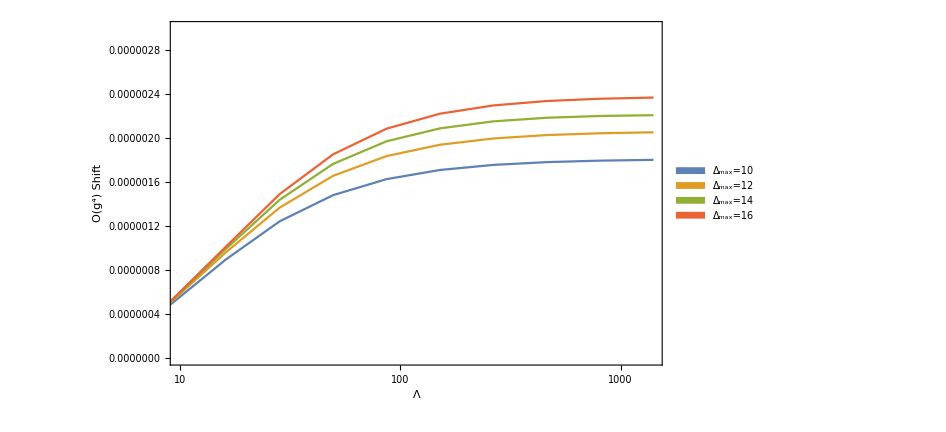

```mathematica
line=Plot[1,{x,0,500},PlotStyle->Black];
plot=ListLogLinearPlot[{Data10,Data12,Data14,Data16},ImageSize->700,PlotRange-> {{10,1400},{0,3*10^-6}},Frame->True,Joined->True,FrameLabel->{{Style["O(g^4) Shift",FontFamily->"Times",FontSize->16,FontColor->Black],None},{Style["Λ",FontFamily->"Times",FontSize->16,FontColor->Black],Style["O(g^4) Mass Shift (ΛIR=0.5)",FontFamily->"Times",FontSize->16,FontColor->Black]}},PlotLegends->Placed[SwatchLegend[{"Δ_max=10","Δ_max=12","Δ_max=14","Δ_max=16"},LabelStyle->{FontFamily->"Times",15},LegendLayout->{"Column",1}],{0.8,0.2}]];
fig=Show[plot]
```

```mathematica
Data16=data16;
```

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="1pg4Shift";
DeleteFile[filename];
Save[filename,{Data10,Data12,Data14,Data16}];
```

DeleteFile::fdnfnd: Directory or file 1pg4Shift not found.

### Extrapolate in Δ_max

```mathematica
KMAX=65;
```

```mathematica
dir="/Users/khandker/Dropbox/Higher D Basis/Dmax16 Data/";
Int3to3=Get[dir<>"Int3to3_Dmax16_Kmax65_r8"];
Int3to5=Get[dir<>"Int3to5_Dmax16_Kmax65_r8"];
```

```mathematica
Clear[Dmax,kmax,m,Λ,ΛIR];
kmax=65;
m=1.;
ΛIR=.5;
Monitor[
temp=Table[
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));

kinetic3=kineticFunc[3,Dmax,kmax]//N;
mass3=massFunc[3,Dmax,kmax]//N;
{val3,vec3}=eigensys[Λ^2*kinetic3+m^2*mass3];

kinetic5=kineticFunc[5,Dmax,kmax]//N;
mass5=massFunc[5,Dmax,kmax]//N;
{val5,vec5}=eigensys[Λ^2*kinetic5+m^2*mass5];


intTemp=int13Func[Dmax,kmax];
int13=(intTemp.Transpose[vec3])/(√(val3-1));

intTemp=Submatrix[Int3to3,3,3,16,KMAX,Dmax,kmax];
int33=(vec3.intTemp.Transpose[vec3])/Outer[√((#1-1)(#2-1))&,val3,val3];

intTemp=Submatrix[Int3to5,3,5,16,KMAX,Dmax,kmax];
int35=(vec3.intTemp.Transpose[vec5])/Outer[√((#1-1)(#2-1))&,val3,val5];

ct3=nonlocalFunc3[Dmax,kmax,Λ];

(* coeff2= -Λ^2(int13.int13)+ct1; *)
(* coeff4=-(int13.int33.int33.int13+int13.int35.Transpose[int35].int13)-coeff2*int13.(int13/(val3-1)); *)
term1=(-Λ^4*int13.int33.int33.int13);
term2=(-Λ^4*int13.int35.Transpose[int35].int13);
term3=Λ^2*(int13/(√(val3-1))).ct3.(int13/(√(val3-1)));
(* coeff4=(4!)^4(-Λ^4(int13.int33.int33.int13+int13.int35.Transpose[int35].int13)-Λ^2*coeff2*int13.(int13/(val3-1))+Λ^2*int13.ct3.int13); *)
(* coeff4=(4!)^4(-Λ^4(int13.int35.Transpose[int35].int13)+Λ^2*int13.ct3.int13); *)
{Dmax,Abs[term1+term2+term3]}
,{Dmax,10,16,1}];
,{Dmax}]
```

```mathematica
DataVaryD=temp
```

{{10,1.80399×10^-6},{11,1.86207×10^-6},{12,2.05432×10^-6},{13,1.89976×10^-6},{14,2.2097×10^-6},{15,2.26084×10^-6},{16,2.3699×10^-6}}

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="1pg4Shift";
DeleteFile[filename];
Save[filename,{Data10,Data12,Data14,Data16,DataVaryD}];
```

### Scratch

```mathematica
(* Nonlocal counterterm function for npart=3 *) 
testFunc3[Δmax_,kmax_,Λ_]:=Module[{m=1.,μsq,kineticN,kineticN2,massN,massN2,IntNtoN2,fullN,fullN2,valsN,vecsN,valsN2,vecsN2,MassShifts,MassShiftsNonPositive,V,first, last},
μsq=N[Accumulate[Prepend[Table[ratioWidth^(kmax-k),{k,kmax}]/Sum[ratioWidth^(kmax-k),{k,kmax}],0]]];
kineticN=kineticFunc[3,Δmax,kmax];
kineticN2=kineticFunc[5,Δmax,kmax];
massN=massFunc[3,Δmax,kmax];
massN2=massFunc[5,Δmax,kmax];
IntNtoN2=int35Func[Δmax,kmax];
fullN=Λ^2*kineticN+m^2*massN//N;
fullN2=Λ^2*kineticN2+m^2*massN2//N;
{valsN,vecsN}=eigensys[fullN];
{valsN2,vecsN2}=eigensys[fullN2];
first=1;
last=FirstPosition[valsN,x_/;x>40 m^2][[1]];
MassShifts=Total[Λ^2*(vecsN.IntNtoN2.Transpose[vecsN2])^2/Outer[Subtract,valsN,valsN2],{2}][[1;;-kmax+1]];
MassShiftsNonPositive=MassShifts/.{x_?Positive->0.};
(* V=vecsN;
-Transpose[V].DiagonalMatrix[MassShiftsNonPositive].V *)
-DiagonalMatrix[MassShiftsNonPositive]
];
```

```mathematica
Clear[Dmax,m,Λ,ΛIR,ΛIRlist];
Dmax=8;
m=1.;
ΛIR=.5;
Monitor[
temp=Table[
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
ct3=testFunc3[Dmax,kmax,Λ];

{Λ,Tr[ct3]/Length[ct3]}
,{kmax,20,80,10}];
,{kmax}]
```

```mathematica
temp
```

{{4.03198,0.000049138},{7.12931,0.0000793771},{12.2464,0.000115071},{20.8404,0.000149606},{35.3529,0.000189049},{59.9056,0.000232231},{101.471,0.000285396}}

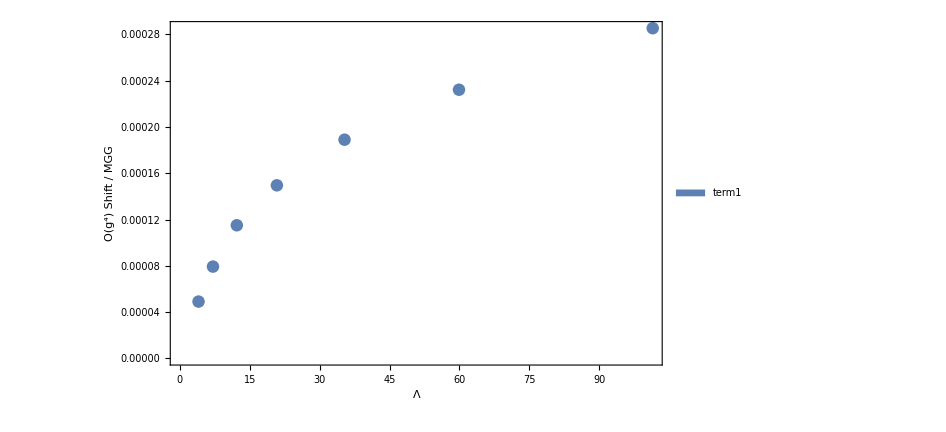

```mathematica
ListPlot[{temp},ImageSize->700,PlotRange->Automatic,Frame->True,Joined->False,FrameLabel->{{Style["O(g^4) Shift / MGG",FontFamily->"Times",FontSize->16,FontColor->Black],None},{Style["Λ",FontFamily->"Times",FontSize->16,FontColor->Black],Style["O(g^4) Mass Shift",FontFamily->"Times",FontSize->16,FontColor->Black]}},PlotLegends->Placed[SwatchLegend[{"term1","term2","term3"},LabelStyle->{FontFamily->"Times",15},LegendLayout->{"Column",1}],{0.8,0.2}]]
```

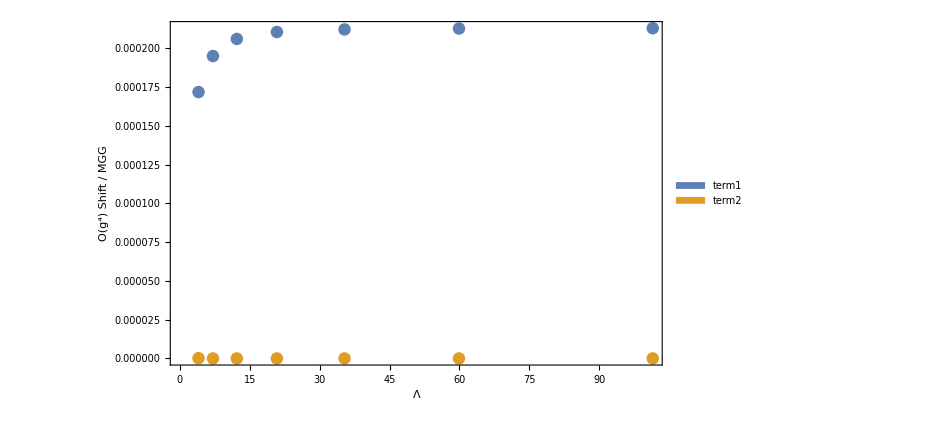

```mathematica
ListPlot[{Thread[{temp[[All,1]],temp[[All,2,1]]}],Thread[{temp[[All,1]],temp[[All,2,100]]}]},ImageSize->700,PlotRange-> Automatic,Frame->True,Joined->False,FrameLabel->{{Style["O(g^4) Shift / MGG",FontFamily->"Times",FontSize->16,FontColor->Black],None},{Style["Λ",FontFamily->"Times",FontSize->16,FontColor->Black],Style["O(g^4) Mass Shift",FontFamily->"Times",FontSize->16,FontColor->Black]}},PlotLegends->Placed[SwatchLegend[{"term1","term2","term3"},LabelStyle->{FontFamily->"Times",15},LegendLayout->{"Column",1}],{0.8,0.2}]]
```

```mathematica
temp//Chop
```

{{4.03198,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{7.12931,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{12.2464,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{20.8404,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{35.3529,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{59.9056,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{101.471,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

### Scratch

```mathematica
Clear[Dmax,m,Λ,ΛIR,ΛIRlist];
Dmax=10;
m=1.;
ΛIR=.5;
Monitor[
temp=Table[
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
kinetic3=kineticFunc[3,Dmax,kmax]//N;
mass3=massFunc[3,Dmax,kmax]//N;
{val3,vec3}=eigensys[Λ^2*kinetic3+m^2*mass3];

intTemp=int13Func[Dmax,kmax];
int13=Table[(intTemp.vec3[[i3]])/(√(val3[[i3]]-1)),{i3,Length[vec3]}];

intTemp=int33Func[Dmax,kmax];
int33=Table[(vec3[[i3]].intTemp.vec3[[j3]])/(√((val3[[i3]]-1)(val3[[j3]]-1))),{i3,Length[vec3]},{j3,Length[vec3]}];

coeff3=(4!)^3*Λ^3(int13.int33.int13); 
{Λ,coeff3}
,{kmax,20,110,10}];
,{kmax}]
```

$Aborted

```mathematica
dataD5=Thread[{temp[[All,1]],temp[[All,2]]/0.8941876918}]
```

{{4.03198,0.0614381},{7.12931,0.141849},{12.2464,0.233273},{20.8404,0.315239},{35.3529,0.379878},{59.9056,0.427379},{101.471,0.460846},{171.855,0.483779},{291.045,0.499185},{492.891,0.509382}}

```mathematica
line=Plot[1,{x,0,500},PlotStyle->Black];
plot=ListPlot[{dataD5},ImageSize->450,PlotRange-> {{0,300},{-.1,1.1}},Frame->True,Joined->True,FrameLabel->{{Style["O(g^3) Shift / MGG",FontFamily->"Times",FontSize->16,FontColor->Black],None},{Style["Λ",FontFamily->"Times",FontSize->16,FontColor->Black],Style["O(g^3) Mass Shift",FontFamily->"Times",FontSize->16,FontColor->Black]}},PlotLegends->Placed[SwatchLegend["Λ_IR=0.5",LabelStyle->{FontFamily->"Times",15},LegendLayout->{"Column",1}],{0.8,0.7}]];
fig=Show[plot,line]
```

-Graphics-

```mathematica
Dmax=5;
kmax=20;
m=1.;
ΛIR=.5;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
```

```mathematica
kinetic3=kineticFunc[3,Dmax,kmax]//N;
mass3=massFunc[3,Dmax,kmax]//N;
{val3,vec3}=eigensys[Λ^2*kinetic3+m^2*mass3];
```

```mathematica
Timing[
intTemp=int13Func[Dmax,kmax];
int13=Table[(intTemp.vec3[[i3]])/(√(val3[[i3]]-1)),{i3,Length[vec3]}];
]
```

{0.002987,Null}

```mathematica
Timing[
intTemp=int13Func[Dmax,kmax];
test13=(intTemp.Transpose[vec3])/(√(val3-1));
]
```

{0.002942,Null}

```mathematica
int13-test13
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Timing[
intTemp=int33Func[Dmax,kmax];
]
```

{0.290325,Null}

```mathematica
Timing[
int33=Table[(vec3[[i3]].intTemp.vec3[[j3]])/(√((val3[[i3]]-1)(val3[[j3]]-1))),{i3,Length[vec3]},{j3,Length[vec3]}];
]
```

{0.045792,Null}

```mathematica
Timing[
test33=(vec3.intTemp.Transpose[vec3])/Outer[√((#1-1)(#2-1))&,val3,val3];
]
```

{0.003073,Null}

```mathematica
int33-test33//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

## 2p O(g^2) Shift

```mathematica
KMAX=65;
```

```mathematica
dir="/Users/khandker/Dropbox/Higher D Basis/Dmax16 Data/";
Get[dir<>"Int2to4_Dmax16_Kmax65_r8"];
```

```mathematica
ratioWidth=8/10;
```

```mathematica
Clear[dmax,m,Λ,ΛIR];
dmax=10;
m=1.;
ΛIR=.5;
s=1;

Monitor[
data10=Table[
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
kinetic2=kineticFunc[2,dmax,kmax]//N;
mass2=massFunc[2,dmax,kmax]//N;
{val2,vec2}=eigensys[Λ^2*kinetic2+m^2*mass2];
kinetic4=kineticFunc[4,dmax,kmax]//N;
mass4=massFunc[4,dmax,kmax]//N;
{val4,vec4}=eigensys[Λ^2*kinetic4+m^2*mass4];

intTemp=vec2.Submatrix[Int2to4,2,4,16,KMAX,dmax,kmax].Transpose[vec4];
int24=intTemp[[s]]/Outer[√(#-val2[[s]])&,val4];

{Λ,(-Λ^2(int24.int24))/(-4*1/(96 π^2)Log[(Λ/m+1)^2/(8(Λ/m-1))])}
,{kmax,20,65,5}];
,{kmax}]
```

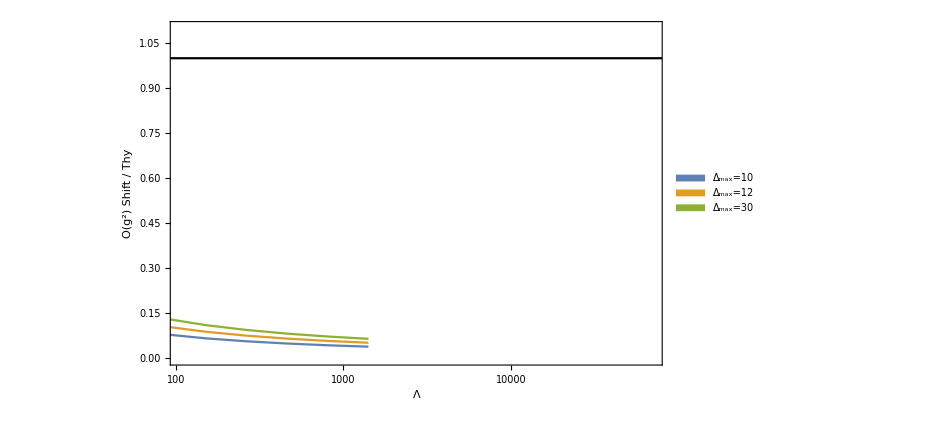

```mathematica
line=Plot[1,{x,0,100000},PlotStyle->{Black}];
plot=ListLogLinearPlot[{data10,data12,data14},ImageSize->700,PlotRange-> {{0,70000},{0,1.1}},Frame->True,Joined->True,FrameLabel->{{Style["O(g^2) Shift / Thy",FontFamily->"Times",FontSize->16,FontColor->Black],None},{Style["Λ",FontFamily->"Times",FontSize->16,FontColor->Black],Style["O(g^2) Mass Shift (Λ_IR = 0.5)",FontFamily->"Times",FontSize->16,FontColor->Black]}},PlotLegends->Placed[SwatchLegend[{"Δ_max=10","Δ_max=12","Δ_max=30","Δ_max=40","Δ_max=18"},LabelStyle->{FontFamily->"Times",15},LegendLayout->{"Column",2}],{.8,.3}]];
fig=Show[plot,line]
```

```mathematica
dir
```

/Users/khandker/Dropbox/Higher D Basis/Zuhair/All Minus Data/

```mathematica
(* Save *)
filename=dir<>"1pg2Shift";
DeleteFile[filename];
Save[filename,{data10,data20,data30,data40}];
```

DeleteFile::fdnfnd: Directory or file /Users/khandker/Dropbox/Higher D Basis/Zuhair/All Minus Data/1pg2Shift not found.

```mathematica
data10
```

{{2.88327,143.636},{5.23657,2.2517},{9.25938,1.25938},{16.2388,1.04498},{28.4041,0.954249},{49.6406,0.901876},{86.7304,0.867009},{151.519,0.842133},{264.696,0.823638},{462.407,0.809471},{807.793,0.798353},{1411.16,0.789443},{2465.19,0.782172},{4306.51,0.776141},{7523.16,0.771066},{13142.4,0.766743},{22958.9,0.763019},{40107.5,0.759778},{70064.9,0.756934}}

## 2p O(g^2) Spectral Shift

```mathematica
KMAX=65;
```

```mathematica
dir="/Users/khandker/Dropbox/Higher D Basis/Dmax16 Data/";
Get[dir<>"Int2to4_Dmax16_Kmax65_r8"];
```

```mathematica
ratioWidth=8/10;
```

```mathematica
Clear[dmax,m,Λ,ΛIR];
dmax=10;
m=1.;
ΛIR=5;
kmax=40;

Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)));
kinetic2=kineticFunc[2,dmax,kmax]//N;
mass2=massFunc[2,dmax,kmax]//N;
{val2,vec2}=eigensys[Λ^2*kinetic2+m^2*mass2];
kinetic4=kineticFunc[4,dmax,kmax]//N;
mass4=massFunc[4,dmax,kmax]//N;
{val4,vec4}=eigensys[Λ^2*kinetic4+m^2*mass4];
int24=Submatrix[Int2to4,2,4,16,KMAX,dmax,kmax];

MElist=36/2^3 Λ^2*Table[(vec2[[1]].int24.vec4[[i]])^2,{i,Length[vec4]}];
MEsum=MElist//Accumulate;
```

```mathematica
npart=2;
dataK40IR5=Thread[{1/m^2(val4/npart-(npart-1)),MEsum}]; 
(* ∑_(μi≤μ) |Subscript[ℳ^(n->n+2), min,i]|^2 = n^3/36 Subscript[I, ϕ^3](μ^2/n-(n-1)m^2) *)
(* Subscript[I, ϕ^3](μ) = 3/(16 π^2)(μ-3m)^2 *) 
(* Iϕ3[μsq_]:=(3 m^2)/(16 π^2)((√μsq)/m-3)^2;
(* thy=(n^3/36 Iϕ3[μ2/n-(n-1)])/.{n->2.}//Expand *)
thy=(Iϕ3[μ2/n-(n-1)])/.{n->2.}//Expand *)
thy=(3 m^2)/(16 π^2)(√(μ2/m^2)-3)^2 //Simplify;
```

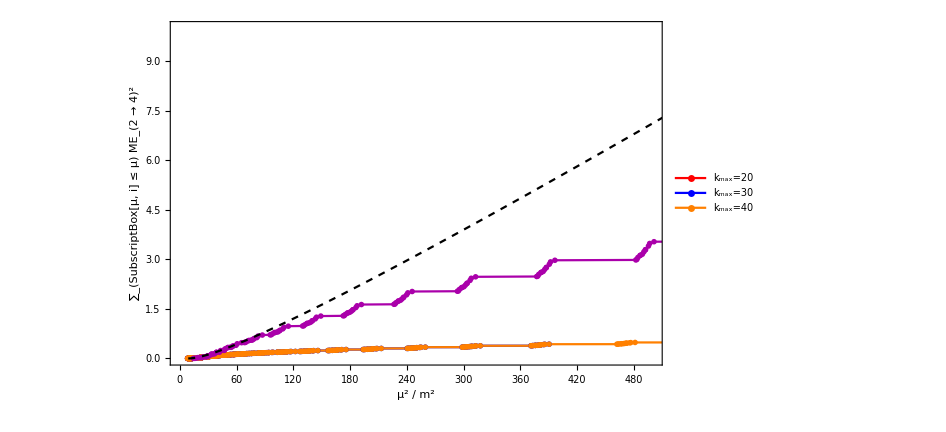

```mathematica
plot=ListPlot[{dataK20,dataK30,dataK40,dataK40IR5},Frame->True,FrameStyle->Thickness[0.002],PlotStyle->{{Red,PointSize[0.012]},{Blue,PointSize[0.012]},{Orange,PointSize[0.012]},{Darker[Magenta],PointSize[0.012]},{Darker[Green],PointSize[0.012]}},FrameLabel->{Style["μ^2 / m^2",FontFamily->"Times",FontSize->16,FontColor->Black],Style["∑_(SubscriptBox[μ, i] ≤  μ) ME_(2 → 4)^2",FontFamily->"Times",FontSize->16,FontColor->Black],Style["2p Perturbative ME^2 Sum  (Δ_max=16,  k_max=60,  Λ=35)",FontFamily->"Times",FontSize->16,FontColor->Black],None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->700,PlotRange->{{0,500},{0,10}},(*PlotLegends->Placed[SwatchLegend[{"k_max = 100","k_max = 40","k_max = 60","k_max = 80","k_max = 100"},LabelStyle->{FontFamily->"Times",10},LegendLayout->{"Row",5}],{.1,0.35}],*)Joined->True,PlotMarkers->{Style["●"],4},PlotLegends->{"k_max=20","k_max=30","k_max=40"}];
thyplot=Plot[thy,{μ2,9,1000},PlotStyle->{Black,Dashed,Thick}];
Show[plot,thyplot]
```

## Scratch

```mathematica
KMAX=65;
```

```mathematica
dir="/Users/khandker/Dropbox/Higher D Basis/Dmax16 Data/";
Get[dir<>"Int2to4_Dmax16_Kmax65_r8"];
```

```mathematica
Clear[dmax,m,Λ,ΛIR];
dmax=16;
m=1.;
Λ=25.;
ΛIR=√(25^2/40);
s=1;

Monitor[
test=Table[
(* Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth))); *)
kinetic2=kineticFunc[2,dmax,kmax]//N;
mass2=massFunc[2,dmax,kmax]//N;
{val2,vec2}=eigensys[Λ^2*kinetic2+m^2*mass2];
kinetic4=kineticFunc[4,dmax,kmax]//N;
mass4=massFunc[4,dmax,kmax]//N;
{val4,vec4}=eigensys[Λ^2*kinetic4+m^2*mass4];

intTemp=vec2.Submatrix[Int2to4,2,4,16,KMAX,dmax,kmax].Transpose[vec4];
int24=intTemp[[s]]/Outer[√(#-val2[[s]])&,val4];

{kmax,(-Λ^2(int24.int24))/(-4*1/(96 π^2)Log[(Λ/m+1)^2/(8(Λ/m-1))])}
,{kmax,10,40,10}];
,{kmax}]
```

```mathematica
test
```

{{10,0.702455},{20,0.468753},{30,0.23465},{40,0.093327}}

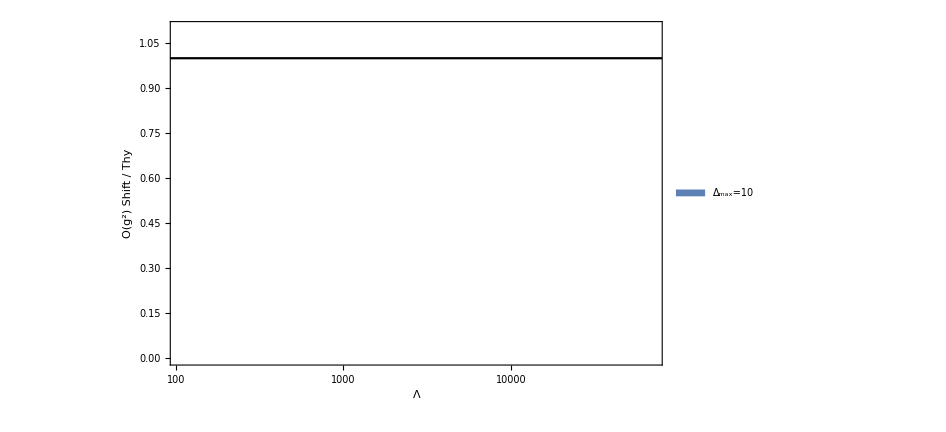

```mathematica
line=Plot[1,{x,0,100000},PlotStyle->{Black}];
plot=ListLogLinearPlot[{test},ImageSize->700,PlotRange-> {{0,70000},{0,1.1}},Frame->True,Joined->True,FrameLabel->{{Style["O(g^2) Shift / Thy",FontFamily->"Times",FontSize->16,FontColor->Black],None},{Style["Λ",FontFamily->"Times",FontSize->16,FontColor->Black],Style["O(g^2) Mass Shift (Λ_IR = 0.5)",FontFamily->"Times",FontSize->16,FontColor->Black]}},PlotLegends->Placed[SwatchLegend[{"Δ_max=10","Δ_max=12","Δ_max=30","Δ_max=40","Δ_max=18"},LabelStyle->{FontFamily->"Times",15},LegendLayout->{"Column",2}],{.8,.3}]];
fig=Show[plot,line]
```

```mathematica
dir
```

/Users/khandker/Dropbox/Higher D Basis/Zuhair/All Minus Data/

```mathematica
(* Save *)
filename=dir<>"1pg2Shift";
DeleteFile[filename];
Save[filename,{data10,data20,data30,data40}];
```

DeleteFile::fdnfnd: Directory or file /Users/khandker/Dropbox/Higher D Basis/Zuhair/All Minus Data/1pg2Shift not found.

```mathematica
data10
```

{{2.88327,143.636},{5.23657,2.2517},{9.25938,1.25938},{16.2388,1.04498},{28.4041,0.954249},{49.6406,0.901876},{86.7304,0.867009},{151.519,0.842133},{264.696,0.823638},{462.407,0.809471},{807.793,0.798353},{1411.16,0.789443},{2465.19,0.782172},{4306.51,0.776141},{7523.16,0.771066},{13142.4,0.766743},{22958.9,0.763019},{40107.5,0.759778},{70064.9,0.756934}}

## Plot

```mathematica
dir="/Users/matt/Dropbox/Higher D Basis/3DCode/";
(*dir="/Users/khandker/Dropbox/Higher D Basis/3DCode/";*)
```

```mathematica
Get[dir<>"1pg2Shift"];
```

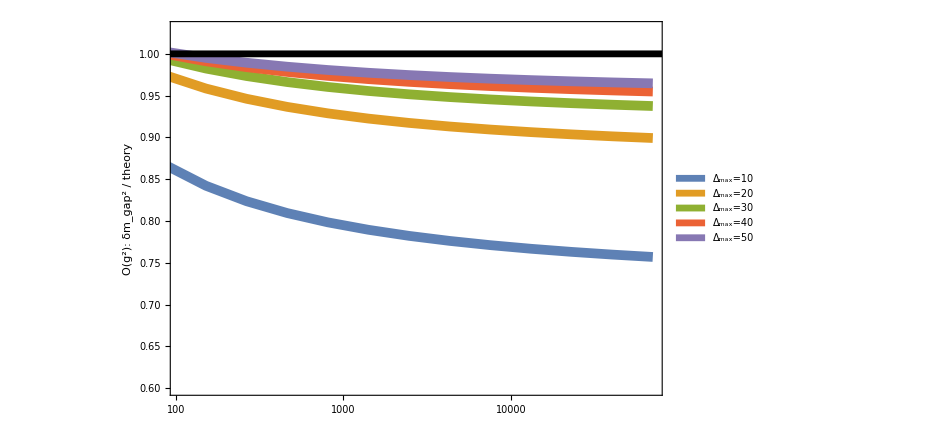

```mathematica
line=Plot[1,{x,0,100000},PlotStyle->{Black,Thickness[.007]}];
plot=ListLogLinearPlot[{data10,data20,data30,data40,data50},ImageSize->700,PlotRange-> {{0,70000},{.6,1.03}},Frame->True,Joined->True,FrameLabel->{{Style["O(g^2):  δm_gap^2 / theory",FontFamily->"Times",FontSize->40,FontColor->Black],None},{Style["",FontFamily->"Times",FontSize->35,FontColor->Black],None}},PlotLegends->Placed[SwatchLegend[{"Δ_max=10","Δ_max=20","Δ_max=30","Δ_max=40","Δ_max=50","Δ_max=18"},LabelStyle->{FontFamily->"Times",28},LegendLayout->{"Column",2}],{0.25,0.23}],PlotStyle->{Thickness[.01]},FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->Directive[Black,22],FrameTicks->Automatic];
fig1=Show[plot,line]
```

{a→-43.0276,b→0.982043}

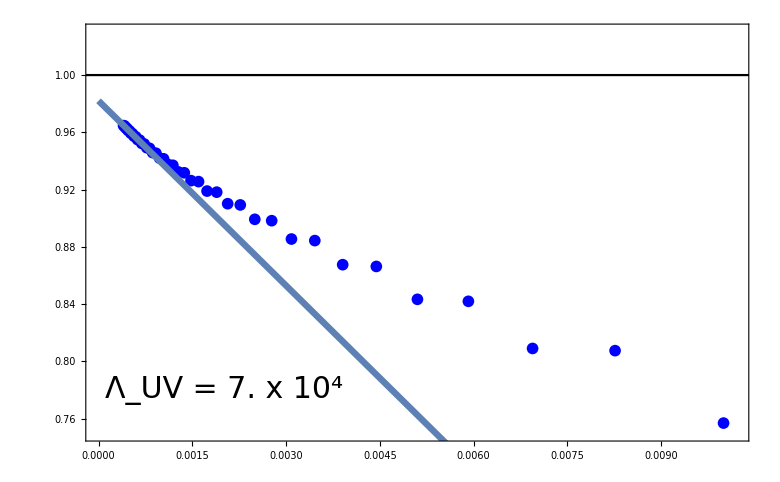

```mathematica
data=Thread[{1/dataVaryD[[All,1]]^2,dataVaryD[[All,2]]}];

marker1=Graphics[{Blue,Disk[]}];
line=Plot[1,{x,-10,10},PlotStyle->Black,PlotRange->All];
plot=ListPlot[{data},ImageSize->780,PlotRange-> {{0,.0102},{.75,1.03}},Frame->True,Joined->False,FrameLabel->{{None,None},{Style["",FontFamily->"Times",FontSize->35,FontColor->Black],None}},PlotLegends->Placed[SwatchLegend[{},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Column",1}],{0.8,0.2}],PlotMarkers->{{marker1,12}},PlotStyle->Blue,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->Directive[Black,22]];
fit=FindFit[data[[31;;All]],a*x+b,{a,b},x]
plotfit=Plot[(a*x+b)/.fit,{x,0,1},PlotStyle->{Thickness[.006]}];
fig2=Show[plot,line,plotfit,Epilog->Inset[Style["Λ_UV = 7. x 10^4",FontFamily->"Times",30],{.002,.78}]]
```

```mathematica
Get[dir<>"1pg3Shift"];
```

```mathematica
dataD40r8
```

{{2.88327,0.0318904},{9.25938,0.226526},{28.4041,0.53328},{86.7304,0.76426},{264.696,0.8854},{807.793,0.939415},{2465.19,0.961741},{7523.16,0.970569},{22958.9,0.973957},{70064.9,0.97523}}

```mathematica
dataD50r8[[;;;;2]]
```

{{2.88327,0.0318904},{9.25938,0.226526},{28.4041,0.53334},{86.7304,0.765624},{264.696,0.888703},{807.793,0.943861},{2465.19,0.966713},{7523.16,0.975762},{22958.9,0.979239},{70064.9,0.980546}}

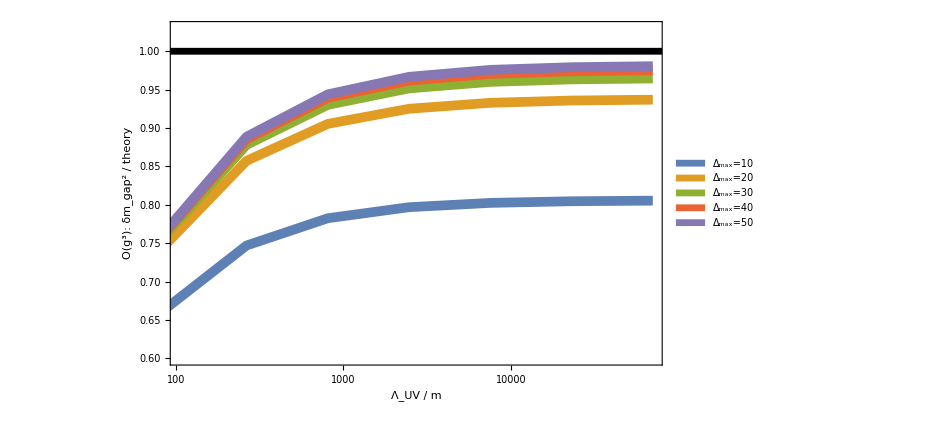

```mathematica
line=Plot[1,{x,0,100000},PlotStyle->{Black,Thickness[.007]}];
plot=ListLogLinearPlot[{dataD10r8,dataD20r8,dataD30r8,dataD40r8,dataD50r8[[;;;;2]]},ImageSize->700,PlotRange-> {{0,70000},{.6,1.03}},Frame->True,Joined->True,FrameLabel->{{Style["O(g^3):  δm_gap^2 / theory",FontFamily->"Times",FontSize->40,FontColor->Black],None},{Style["Λ_UV / m",FontFamily->"Times",FontSize->40,FontColor->Black],None}},PlotLegends->Placed[SwatchLegend[{"Δ_max=10","Δ_max=20","Δ_max=30","Δ_max=40","Δ_max=50","Δ_max=18"},LabelStyle->{FontFamily->"Times",28},LegendLayout->{"Column",2}],{0.75,0.23}],PlotStyle->{Thickness[.01]},FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->Directive[Black,22]];
fig3=Show[plot,line]
```

{a→-23.2646,b→0.989991}

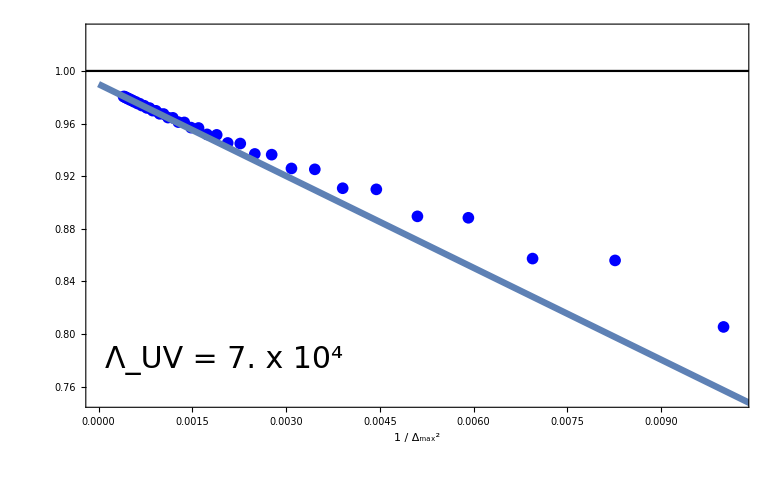

```mathematica
thy=(4!)^3/(4(4π)^2(2π)^2)(7/16 π*Zeta[3]);
data=Thread[{1/datar8VaryD[[All,1]]^2,datar8VaryD[[All,2]]/thy}]//N;

marker1=Graphics[{Blue,Disk[]}];
line=Plot[1,{x,-10,10},PlotStyle->Black,PlotRange->All];
plot=ListPlot[{data},ImageSize->780,PlotRange-> {{0,.0102},{.75,1.03}},Frame->True,Joined->False,FrameLabel->{{None,None},{Style["1 / Δ_max^2",FontFamily->"Times",FontSize->40,FontColor->Black],None}},PlotLegends->Placed[SwatchLegend[{},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Column",1}],{0.8,0.2}],PlotMarkers->{{marker1,12}},PlotStyle->Blue,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->Directive[Black,22]];
fit=FindFit[data[[31;;All]],a*x+b,{a,b},x]
plotfit=Plot[(a*x+b)/.fit,{x,0,1},PlotStyle->{Thickness[.006]}];
fig4=Show[plot,line,plotfit,Epilog->Inset[Style["Λ_UV = 7. x 10^4",FontFamily->"Times",30],{.002,.78}]]
```

```mathematica
Get[dir<>"1pg4Shift"];
```

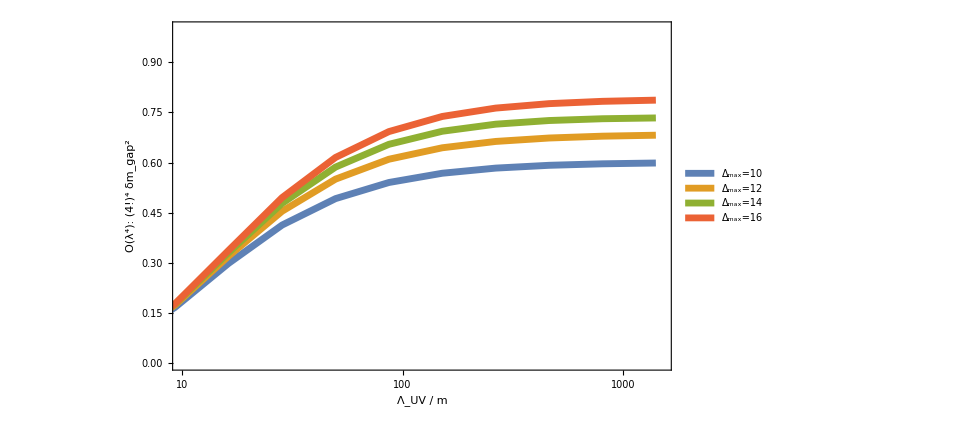

```mathematica
line=Plot[1,{x,0,100000},PlotStyle->{Black,Thickness[.007]}];
plot=ListLogLinearPlot[{Thread[{Data10[[All,1]],(4!)^4 Data10[[All,2]]}],Thread[{Data12[[All,1]],(4!)^4 Data12[[All,2]]}],Thread[{Data14[[All,1]],(4!)^4 Data14[[All,2]]}],Thread[{Data16[[All,1]],(4!)^4 Data16[[All,2]]}]},ImageSize->710,PlotRange-> {{10,1500},{0,1}},Frame->True,Joined->True,FrameLabel->{{Style["O(λ^4):  (4!)^4 δm_gap^2",FontFamily->"Times",FontSize->35,FontColor->Black],None},{Style["Λ_UV / m",FontFamily->"Times",FontSize->35,FontColor->Black],None}},PlotLegends->Placed[SwatchLegend[{"Δ_max=10","Δ_max=12","Δ_max=14","Δ_max=16","Δ_max=16","Δ_max=18"},LabelStyle->{FontFamily->"Times",28},LegendLayout->{"Column",1}],{0.8,0.23}],PlotStyle->{Thickness[.007]},FrameStyle->{Black,Thickness[0.003]},FrameTicksStyle->Directive[Black,26]];
fig5=Show[plot]
```

{a→-29.7812,b→0.87504}

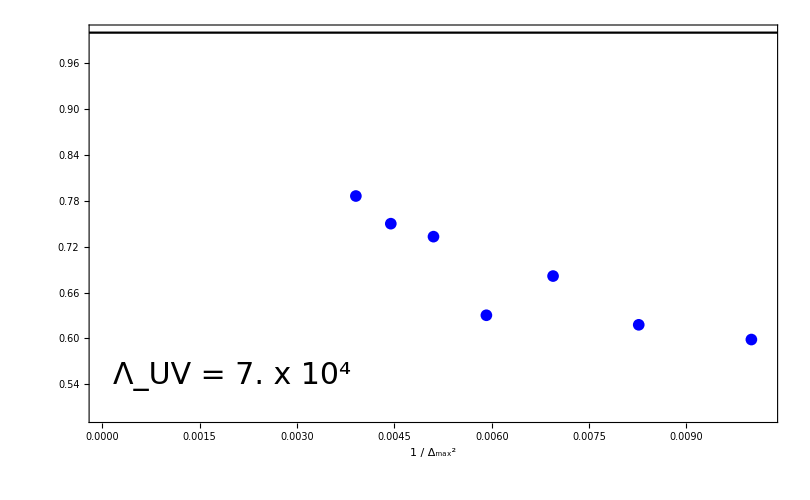

```mathematica
data=Thread[{1/DataVaryD[[All,1]]^2,(4!)^4 DataVaryD[[All,2]]}]//N;

marker1=Graphics[{Blue,Disk[]}];
line=Plot[1,{x,-10,10},PlotStyle->Black,PlotRange->All];
plot=ListPlot[{data},ImageSize->810,PlotRange-> {{0,.0102},{.5,1}},Frame->True,Joined->False,FrameLabel->{{None,None},{Style["1 / Δ_max^2",FontFamily->"Times",FontSize->35,FontColor->Black],None}},PlotLegends->Placed[SwatchLegend[{},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Column",1}],{0.8,0.2}],PlotMarkers->{{marker1,12}},PlotStyle->Blue,FrameStyle->{Black,Thickness[0.003]},FrameTicksStyle->Directive[Black,26]];
fit=FindFit[data[[1;;All]],a*x+b,{a,b},x]
plotfit=Plot[(a*x+b)/.fit,{x,0,1},PlotStyle->{Thickness[.006]}];
fig6=Show[plot,line,Epilog->Inset[Style["Λ_UV = 7. x 10^4",FontFamily->"Times",30],{0.002,.55}]]
```

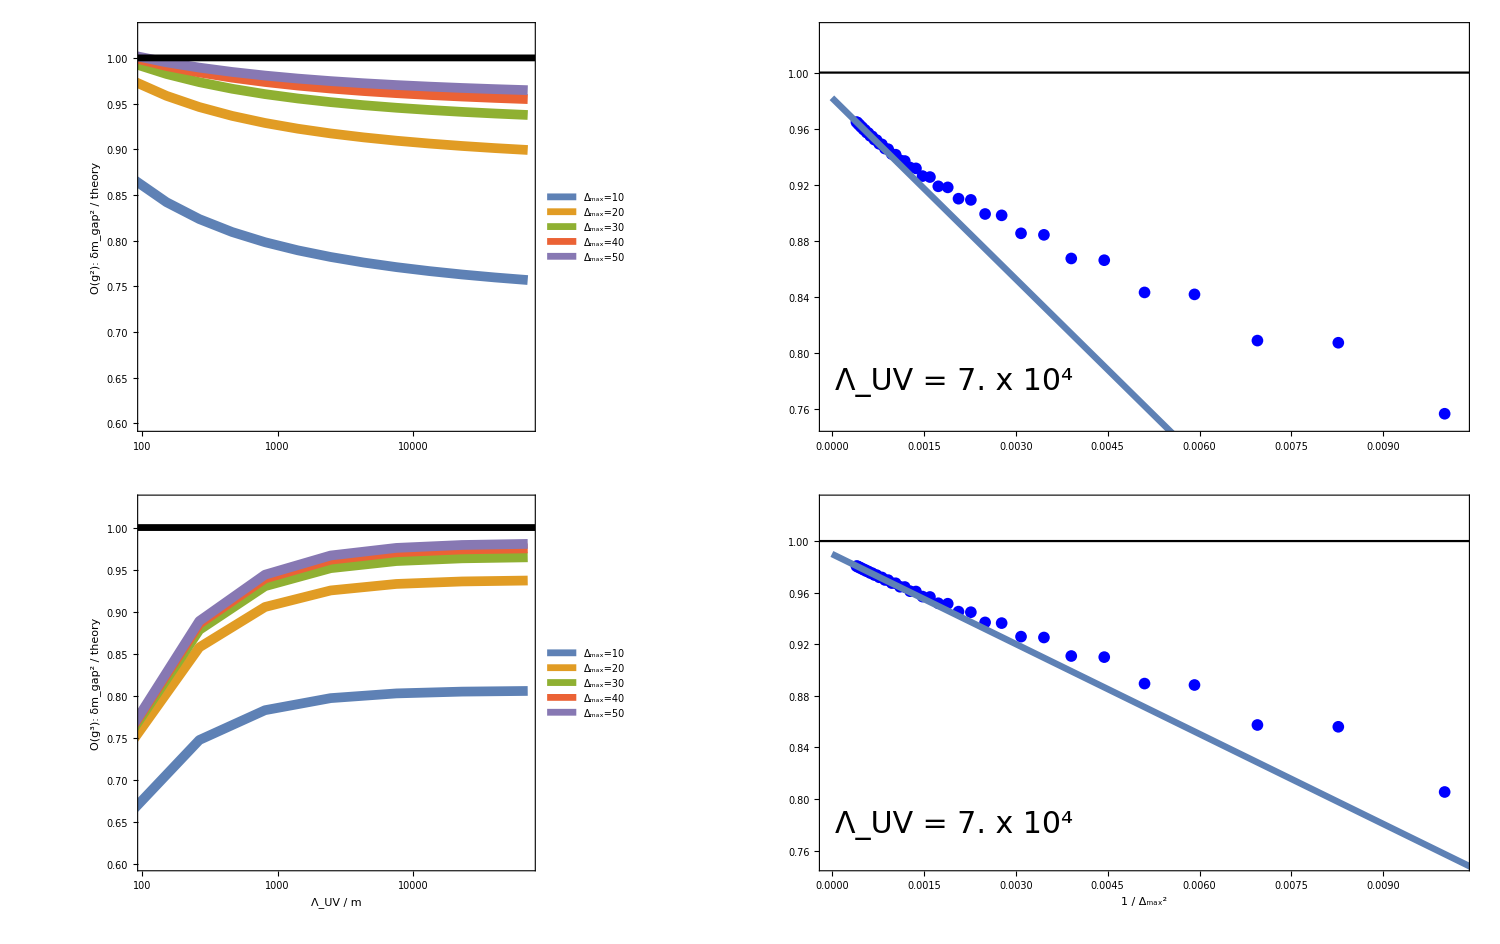
-Graphics-Matching Perturbation Theory

```mathematica
grid=Labeled[GraphicsGrid[{{fig1,fig2},{fig3,fig4}},ImageSize->1500,Spacings->{-30,0}],{"Matching Perturbation Theory"},{Top,Left},RotateLabel->True,LabelStyle->Directive[FontFamily->"Times",45],Spacings->{-.5,0}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["./PerturbationTheory.pdf",grid];
```